```mathematica
ToBaseWord[w_]:=Block[{wn},wn=WordData[w];If[Length[wn]≤0,w,wn[[1,1]]]];
WordHasMeaningQ[w_]:=Block[{wn},wn=WordData[w,"PartsOfSpeech"];
NumberQ[w]
||(Not[MemberQ[wn,"Preposition"]]
&&Not[MemberQ[wn,"Conjunction"]]
&&Not[MemberQ[wn,"Determiner"]]
)
];
YearExpenseData[year_]:=Block[{expensesXml,accountInfo,dict,wordToAccountIds,sum,maxCount,maxAmount,json},
expensesXml=Import["http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year="<>ToString[year],"XML"];
accountInfo=SortBy[
ReleaseHold[{"account",Hold[ToExpression["amounti"]],"function","subfunction"}/.Cases[expensesXml,XMLElement["item",__,__],Infinity][[All,2]]],
(-#[[2]])&];
dict=Union[accountInfo[[All,3]],accountInfo[[All,4]]];
wordToAccountIds=Select[{#[[1,1]],#[[All,2]]}&/@GatherBy[
Flatten[Function[{accountIndex},{ToBaseWord[ToLowerCase[#]],accountIndex}&/@StringSplit[accountInfo[[accountIndex,1]],RegularExpression["[^a-zA-Z0-9]+"]]]/@
Range[1,Length[accountInfo]],1],
#[[1]]&],
WordHasMeaningQ[#[[1]]]&];
Print[wordToAccountIds[[All,1]]];
sum=SortBy[
Block[{w,ids},{w,ids}={#[[1]],Union[#[[2]]]};{w,Length[ids],Total[accountInfo[[ids,2]]],ids}]&/@wordToAccountIds,
{-#[[2]],#[[1]]}&];
maxCount=Max[Abs[sum[[All,2]]]];
maxAmount=Max[Abs[sum[[All,3]]]];
json="{\"summary\":["<>ToString[maxCount]<>","<>ToString[maxAmount]<>"],\n"<>
(* Sorted in descending order by count *)
"\"yed\":"<>
StringReplace[
ToString[sum,InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>

"\"dict\":"<>
StringReplace[
ToString[dict,InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>

"\"functions\":"<>
StringReplace[ToString[
accountInfo[[All,3;;4]]/.((#[[1]]->#[[2]])&/@Partition[Riffle[dict,Range[1,Length[dict]]],2]),
InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>
(* Sorted in descending order by amount *)
"\"accounts\":"<>
StringReplace[ToString[accountInfo[[All,1;;2]],InputForm],
{"{"->"[","}"->"]"}]<>"}";
Export["/home/xcolwell/yed_"<>ToString[year]<>".json",json,"Text"];
PrintTemporary[year];
sum
];
```

```mathematica
sums=YearExpenseData/@Range[1984,2010];
```

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,hospital,unemployment,operation,maintenance,navy,civil,service,retirement,disability,aircraft,procurement,air,force,grant,state,medicaid,supplementary,medical,payment,health,care,funds,army,retired,pay,defense,impute,accrual,military,costs,personnel,aid,highway,supplemental,nutrition,assistance,program,research,development,test,evaluation,shipbuilding,conversion,foreign,sales,compensation,pension,annual,contribution,assisted,housing,agricultural,credit,liquidate,account,social,child,support,enforcement,family,services,missile,income,rural,atomic,energy,activity,training,employment,wide,advance,rail,industry,united,quota,international,monetary,financing,weapon,tracked,combat,vehicle,local,government,fiscal,assist,national,institute,student,financial,benefit,space,flight,control,data,communications,community,marine,corps,accelerate,achievement,ensure,equity,economic,block,operations,railroad,tribal,telephone,bank,formula,education,loan,uranium,supply,enrichment,low,home,ammunition,conservation,guard,operating,expense,public,annuitant,employee,construction,readjustment,law,480,agriculture,reserve,special,woman,infant,wic,refund,internal,revenue,collection,stock,rent,discretionary,mass,transit,life,customs,border,protection,related,earned,exceed,liability,tax,resource,diplomatic,consular,passenger,corporation,disabled,coal,miner,salary,rehabilitation,taxpayer,investigation,facility,management,airport,airway,association,forest,system,postal,water,black,lung,career,technical,adult,export,import,indian,equipment,mineral,lease,associate,general,acquisition,improvement,fslic,foster,adoption,spr,petroleum,science,strategic,park,impact,elderly,or,handicapped,refugee,entrant,organization,tennessee,valley,authority,district,columbia,information,substance,abuse,mental,hazardous,superfund,environmental,urban,action,higher,dual,panama,canal,revolve,land,alternative,fuel,production,electrification,telecommunication,attorney,central,liquidity,miscellaneous,survey,sba,ffb,small,business,investment,company,debenture,agency,puerto,rico,departmental,administration,differential,subsidy,strengthening,market,section,32,major,project,migration,extension,nuclear,waste,disposal,older,americans,disease,mississippi,river,tributary,bonneville,power,interstate,transfer,legal,abandoned,reclamation,job,opportunity,basic,skill,fossil,engineering,naval,oil,shale,reserves,capital,washington,metropolitan,area,claim,judgment,relief,act,post,vietnam,era,veteran,prosthetic,embassy,commodity,permanent,appropriation,administrative,reimbursement,elec,tel,revolv,int,justice,administer,watershed,flood,prevention,western,minor,english,learner,royalty,offshore,officer,endowment,arts,appalachian,regional,commission,crop,howard,university,department,restoration,industrial,traffic,safety,library,congress,humanities,broadcasting,domestic,volunteer,vocational,burial,wildlife,inter,american,peace,scientific,territory,pacific,island,technology,asian,emergency,food,shelter,rangeland,bankruptcy,court,office,museum,lieu,taxis,africa,educational,cultural,exchange,northeast,corridor,function,inspector,copyright,owner,cooperative,work,interagency,crime,drug,advancement,regulatory,building,grounds,congressional,printing,binding,intelligence,official,mail,reconstruction,periodic,census,human,commissioned,timber,purchaser,road,credits,regulation,fha,mutual,mortgage,conrail,labor,private,forestry,rental,peacekeeping,gallaudet,statistics,harbor,contribute,policy,minority,prisoner,detention,disaster,african,north,atlantic,treaty,summer,olympics,developmental,multifamily,revitalization,oregon,california,worker,inquiry,carrier,bureau,roads,trail,right,antitrust,division,receipts,owned,real,property,settlement,litigation,fee,juror,commissioner,universal,defender,narcotic,mint,enterprise,budget,witness,southwestern,armed,member,book,blind,physically,presidential,election,campaign,gallery,art,sergeant,arms,doorkeeper,senate,marketing,relations,guarantee,product,school,abroad,purchase,deaf,aviation,weather,future,trading,historic,preservation,superintendent,document,solar,planning,capitol,plant,president,white,house,great,plain,dod,migratory,bird,southeastern,college,academic,recreation,colorado,dam,boulder,canyon,disarmament,east,west,center,extended,democracy,synthetic,uninvested,trade,neighborhood,reinvestment,counsel,sector,coastal,zone,barrow,gas,exploration,foundation,refuge,judicial,annuity,boat,incentive,repair,alteration,allowance,homestead,representative,pennsylvania,avenue,ibwc,currency,mission,cuba,range,promote,develop,fishery,pertain,asia,item,ship,fishing,vessel,taiwan,conference,contingency,surety,bond,secret,geothermal,motor,gift,indemnity,papago,us,unclaimed,good,limitation,inspection,weighing,self,help,manufactured,monitoring,observer,visitor,donation,secretary,cooperation,structural,appeal,transportation,buying,pollution,use,fair,john,f,kennedy,performing,charge,harry,s,truman,memorial,scholarship,representation,betterment,deposit,forfeiture,working,counseling,joint,committee,taxation,alaska,fire,reorganization,expansion,cemetery,distribution,material,perishable,overseas,surplus,personal,woodrow,wilson,scholar,anti,terrorism,d,c,fisherman,guaranty,botanic,garden,holocaust,dairy,u,bilateral,agreement,japan,friendship,residence,furniture,furnishings,executive,council,quality,archives,citizen,legislative,communication,staff,former,prog,participation,insufficiency,deepwater,port,close,possession,savings,liquidation,unanticipated,needs,board,promotion,rifle,practice,eastern,grading,farm,inaugural,ceremony,1993,attending,physician,europe,pershing,hall,chrysler,homeowner,bequest,contingent,coo,bay,wagon,widow,heir,deceased,delaware,basin,judge,sale,susquehanna,tribunal,mileage,martha,study,interior,biological,stationery,undistributed,intragovernmental,receivables,cancelled,potomac,senator,tempore,majority,leaders,whip,grazing,etc,race,affairs,statement,olive,wendell,holmes,devise,16,4601,6a,jefferson,nps,assessment,st,elizabeth,hhs,trustee,townsites,blm,gertrude,m,hubbard,aeronautics,adminstration,commerce,advisory,earnings,maritime,patient,phs,george,edgeter,fdi,academy,leased,federally,acquired,independence,historical,birthplace,abraham,lincoln,unconditional,recovery,fighting,pursuant,liabilities,coast,dot,elizabeths,esther,cattel,schmitt,transmission,electric,record,history,usgli,va,fm,reduction,civ,mil,retiree,offbud,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,falcon,pribilof,fhi,proprietary,grand,teton,yellowstone,25,i,h,conditional,money,due,oklahoma,south,red,3,4,23,amended,battle,monument,employ,engineer,fsmi,hydraulic,mining,storage,debris,reservoir,cooperate,misc,smithsonian,usia,profits,foasi,relie,hunting,permit,reservation,feed,agen,result,ret,tres,premium,character,merchandising,publication,reproduction,not,classified,forein,licensee,intergovernmental,conscience,proceeds,fish,closure,complete,donate,gap,route,209,commercial,doi,include,soil,gear,damage,grassland,minnesota,cook,lake,louis,county,share,late,collected,nevada,nsli,attendant,animal,quarantine,aphis,lost,damaged,inland,waterway,interim,paid,resident,soldier,airman,coinage,profit,padc,reforestation,invest,comp,nat,tf,75,fema,landsat,noaa,dollar,advanced,navigation,allied,purpose,dhs,taylor,faa,domain,gain,denominate,received,outer,continental,shelf,escrow,civilian,salvage,store,repayment,utility,award,employed,offset,uninsured,individual,eligible,olympic,coin,clearing,suspense,manufacturing,bonus,extraction,interfund,transactions,tongass,nation,recoverable,user,natural,brush,municipality,body,reserved,ams,normalize,scrap,sec,trans,rr,psr,corp,fra,repayable,bpa,hist,fnd,rcpts,cont,wapa,employer,fica,deduction,return,principal,1974,toll,borrowing,g,nprs,non,aged,retire}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,aircraft,procurement,air,force,operation,maintenance,navy,civil,service,retirement,disability,grant,state,medicaid,supplementary,medical,military,personnel,army,unemployment,payment,health,care,funds,commodity,credit,corporation,aid,highway,low,rent,public,housing,loan,expense,research,development,test,evaluation,supplemental,nutrition,assistance,program,foreign,sales,shipbuilding,conversion,annual,contribution,assisted,social,compensation,pension,agricultural,liquidate,account,child,support,enforcement,family,services,income,atomic,energy,defense,activity,wide,missile,financing,rural,economic,railroad,equivalent,benefit,student,financial,national,institute,marine,corps,local,government,fiscal,assist,weapon,tracked,combat,vehicle,education,training,employment,accelerate,achievement,ensure,equity,space,flight,control,data,communications,community,guard,block,ammunition,formula,tribal,stock,electrification,telecommunication,rail,industry,home,spr,petroleum,reserve,supply,conservation,law,480,agriculture,operating,refund,internal,revenue,collection,uranium,enrichment,construction,operations,industrial,special,woman,infant,wic,diplomatic,consular,postal,related,alternative,fuel,production,customs,border,protection,facility,equipment,airport,airway,annuitant,employee,life,resource,salary,taxpayer,forest,system,share,faa,readjustment,discretionary,mass,transit,rehabilitation,earned,exceed,liability,tax,management,investigation,disabled,coal,miner,black,lung,water,career,technical,adult,international,association,tennessee,valley,authority,indian,foster,adoption,improvement,general,science,impact,passenger,park,hazardous,substance,superfund,major,project,district,columbia,information,mineral,lease,associate,business,elderly,or,handicapped,abuse,mental,higher,organization,strengthening,market,section,32,environmental,land,united,attorney,refugee,entrant,urban,action,panama,canal,revolve,miscellaneous,survey,acquisition,embassy,dual,agency,telephone,bank,departmental,administration,disease,extension,differential,subsidy,migration,retired,pay,nuclear,waste,disposal,puerto,rico,older,americans,mississippi,river,tributary,department,restoration,claim,judgment,relief,act,legal,hud,abandoned,reclamation,post,vietnam,era,veteran,fossil,bonneville,power,crop,job,opportunity,basic,skill,engineering,sba,ffb,small,investment,company,debenture,sec,503,guarantee,direct,interstate,transfer,washington,metropolitan,area,inter,american,permanent,appropriation,western,reimbursement,elec,tel,revolv,int,asian,administrative,fslic,minor,administer,prosthetic,watershed,flood,prevention,traffic,safety,receipts,surplus,real,personal,property,english,learner,officer,endowment,arts,royalty,offshore,disaster,howard,university,naval,oil,shale,reserves,appalachian,regional,commission,broadcasting,domestic,volunteer,office,museum,library,justice,educational,cultural,exchange,reconstruction,humanities,advance,cooperative,work,technology,congress,burial,ship,peace,wildlife,scientific,bankruptcy,court,advancement,rangeland,capital,copyright,owner,universal,north,atlantic,treaty,lieu,taxis,fha,mutual,mortgage,central,intelligence,territory,pacific,island,africa,regulatory,proprietary,not,classified,building,human,periodic,census,congressional,printing,binding,regulation,allowance,earnings,commissioned,bureau,defender,inspector,rental,crime,victim,worker,oregon,developmental,policy,gallaudet,dod,private,forestry,statistics,prisoner,detention,california,multifamily,revitalization,inquiry,narcotic,african,coastal,emergency,harbor,contribute,minority,sergeant,arms,doorkeeper,senate,peacekeeping,right,fee,juror,commissioner,antitrust,division,armed,witness,carrier,synthetic,budget,guaranty,member,gallery,art,book,blind,physically,migratory,bird,southeastern,enhanced,countermeasure,capability,presidential,election,campaign,extended,marketing,relations,deaf,southwestern,product,school,abroad,purchase,superintendent,document,boat,northeast,corridor,future,trading,aviation,weather,humanitarian,nicaragua,democratic,resistance,historic,preservation,president,white,house,fishery,planning,disarmament,colorado,dam,boulder,canyon,capitol,plant,great,plain,mission,currency,trade,uninvested,food,shelter,sale,timber,revested,east,west,center,repair,alteration,mint,enterprise,sector,counsel,neighborhood,reinvestment,solar,conrail,labor,judicial,annuity,college,academic,motor,representative,refuge,incentive,homestead,foundation,official,mail,costs,ibwc,item,recreation,secret,indemnity,clearing,suspense,range,taiwan,conference,contingency,asia,promote,develop,pertain,lien,surety,bond,fishing,vessel,cuba,gift,self,help,inland,waterway,quarters,reorganization,pollution,fair,pennsylvania,avenue,us,unclaimed,good,geothermal,preparedness,working,visitor,grounds,secretary,papago,transportation,manufactured,inspection,monitoring,charge,deposit,forfeiture,cooperation,anti,terrorism,cemetery,russian,eurasian,european,john,f,kennedy,performing,observer,representation,congregate,fisherman,s,betterment,harry,truman,memorial,scholarship,donation,joint,committee,taxation,counseling,perishable,distribution,material,fire,alaska,appeal,overseas,woodrow,wilson,scholar,utah,paiute,gov,fu,interagency,drug,botanic,garden,holocaust,implementation,contadora,agreement,use,residence,furniture,furnishings,executive,japan,friendship,legislative,buying,homeowner,staff,former,citizen,d,c,attending,physician,deepwater,port,protective,accounting,principle,board,unanticipated,needs,possession,settlement,promotion,rifle,practice,communication,inaugural,ceremony,1993,council,quality,grading,farm,europe,coo,bay,wagon,road,pershing,hall,litigation,bequest,study,ukraine,famine,judge,delaware,basin,participation,insufficiency,illinois,michigan,heritage,contingent,susquehanna,tribunal,mileage,martha,archives,zone,biological,dairy,widow,heir,deceased,jefferson,expansion,potomac,senator,tempore,majority,leaders,whip,transmission,electric,olive,wendell,holmes,devise,fsmi,stationery,principal,trustee,townsites,blm,interior,statement,dot,conditional,grazing,etc,engineer,barrow,gas,exploration,liquidity,chrysler,structural,nps,eastern,close,prog,export,import,fdi,impute,accrual,employer,retire,g,m,function,1974,trans,nat,rr,psr,corp,fra,licensee,limitation,weighing,monetary,democracy,roads,trail,st,elizabeth,hhs,fm,tf,savings,liquidation,recovery,reduction,civ,mil,retiree,offbud,feed,agen,result,ret,tres,16,u,4601,6a,pursuant,liabilities,repayable,repayment,strategic,summer,olympics,purchaser,credits,undistributed,intragovernmental,receivables,cancelled,quota,bilateral,vocational,fhi,gertrude,hubbard,advisory,aeronautics,adminstration,assessment,leased,federally,acquired,independence,historical,commerce,maritime,publication,reproduction,patient,phs,george,edgeter,academy,race,map,chart,noaa,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,elizabeths,landsat,unconditional,birthplace,abraham,lincoln,grassland,esther,cattel,schmitt,record,history,fighting,workman,usgli,va,coast,money,due,oklahoma,south,red,3,4,23,amended,battle,monument,grand,teton,yellowstone,25,pribilof,falcon,i,h,geological,relie,character,merchandising,employ,renewal,foasi,hydraulic,mining,storage,debris,reservoir,usia,hunting,permit,reservation,intergovernmental,premium,donate,affairs,smithsonian,profits,gear,damage,proceeds,fish,nevada,conscience,longshoreman,civilian,gap,route,209,commercial,doi,soil,forein,include,cooperate,misc,minnesota,cook,lake,louis,county,complete,collected,recl,padc,late,nsli,closure,received,outer,continental,shelf,escrow,v,aphis,lost,damaged,attendant,animal,quarantine,coinage,profit,1984,owned,paid,resident,soldier,airman,75,interim,dhs,dollar,advanced,domain,invest,comp,fema,reforestation,taylor,navigation,allied,purpose,normalize,salvage,olympic,coin,aquatic,store,bonus,extraction,gain,denominate,award,utility,employed,offset,uninsured,individual,eligible,manufacturing,interfund,transactions,nation,boating,user,tongass,brush,reserved,recoverable,scrap,ams,natural,municipality,body,hist,fnd,rcpts,cont,bpa,deduction,fica,return,wapa,borrowing,toll,nprs,non,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,supplementary,medical,civil,service,retirement,disability,grant,state,medicaid,operation,maintenance,navy,commodity,credit,corporation,aircraft,procurement,air,force,military,personnel,army,payment,health,care,funds,unemployment,aid,highway,research,development,test,evaluation,supplemental,nutrition,assistance,program,compensation,pension,shipbuilding,conversion,child,support,enforcement,family,annual,contribution,assisted,housing,income,services,missile,foreign,sales,atomic,energy,defense,activity,wide,railroad,social,equivalent,benefit,account,national,institute,weapon,financing,marine,corps,student,financial,agricultural,liquidate,tracked,combat,vehicle,local,government,fiscal,assist,economic,space,flight,control,data,communications,accelerate,achievement,ensure,equity,training,employment,education,loan,guard,rural,community,fslic,block,ammunition,operations,reserve,stock,formula,low,home,refund,internal,revenue,collection,postal,electrification,telecommunication,tribal,supply,conservation,diplomatic,consular,operating,expense,construction,special,woman,infant,wic,uranium,enrichment,annuitant,employee,united,quota,international,monetary,equipment,customs,border,protection,rail,industry,earned,exceed,liability,tax,related,life,taxpayer,ship,public,law,480,agriculture,resource,forest,system,salary,rehabilitation,facility,investigation,management,discretionary,mass,transit,disabled,coal,miner,tennessee,valley,authority,black,lung,airport,airway,career,technical,adult,rent,readjustment,indian,foster,adoption,embassy,general,permanent,appropriation,impact,improvement,association,water,science,park,restitution,forgo,industrial,passenger,environmental,information,district,columbia,business,nuclear,waste,disposal,elderly,or,handicapped,substance,abuse,mental,major,project,panama,canal,revolve,organization,higher,share,faa,mineral,lease,associate,survey,bonneville,power,administration,refugee,entrant,departmental,disease,land,strengthening,market,section,32,dual,agency,disaster,relief,retired,pay,extension,migration,post,vietnam,era,veteran,budget,clearing,suspense,attorney,urban,action,older,americans,miscellaneous,fossil,mississippi,river,tributary,legal,advance,claim,judgment,act,differential,subsidy,hazardous,superfund,watershed,flood,prevention,acquisition,engineering,compact,free,washington,metropolitan,area,capital,administrative,puerto,rico,job,opportunity,basic,skill,coastal,augmentation,abandoned,reclamation,western,justice,interstate,transfer,administer,prosthetic,universal,english,learner,officer,technology,royalty,offshore,broadcasting,endowment,arts,howard,university,marshal,cooperative,work,domestic,volunteer,office,museum,library,mint,enterprise,fha,mutual,mortgage,educational,cultural,exchange,crop,bank,reconstruction,humanities,burial,congress,traffic,safety,peace,sport,fish,restoration,wildlife,appalachian,regional,commission,scientific,developmental,rangeland,advancement,strategic,petroleum,asian,central,intelligence,periodic,census,lieu,taxis,reimbursement,elec,tel,revolv,int,copyright,owner,settlement,litigation,official,mail,costs,minor,regulatory,inter,american,regulation,commissioned,territory,surplus,real,personal,property,receipts,africa,pacific,island,adp,sub,saharan,emergency,food,shelter,annuity,worker,congressional,printing,binding,building,rental,african,gallaudet,crime,victim,defender,prisoner,detention,statistics,private,forestry,narcotic,oregon,california,human,sergeant,arms,doorkeeper,senate,telephone,harbor,contribute,inquiry,grassland,boat,policy,armed,fee,juror,commissioner,witness,inspector,minority,right,member,bureau,presidential,election,campaign,vocational,school,abroad,product,marketing,peacekeeping,book,blind,physically,gallery,art,court,deaf,production,purchase,southwestern,migratory,bird,relations,future,trading,aviation,weather,carrier,guarantee,disarmament,capitol,plant,president,white,house,historic,preservation,planning,department,superintendent,document,uninvested,extended,great,plain,east,west,center,stockpile,transaction,colorado,dam,boulder,canyon,trade,college,academic,neighborhood,reinvestment,democracy,motor,sector,repair,alteration,counsel,nato,judicial,donation,naval,oil,shale,reserves,representative,northeast,corridor,incentive,asia,foundation,homestead,secret,refuge,fishery,ibwc,recreation,cuba,counterterrorism,allowance,anti,terrorism,indemnity,range,promote,develop,pertain,north,atlantic,treaty,investment,tenth,pan,game,item,taiwan,dairy,mission,gift,self,help,transportation,audit,contract,alaska,native,escrow,surety,bond,quarters,fair,d,c,working,secretary,preparedness,conference,contingency,reorganization,grounds,pennsylvania,avenue,manufactured,inspection,monitoring,cooperation,charge,deposit,forfeiture,russian,eurasian,european,john,f,kennedy,performing,representation,joint,committee,taxation,bequest,continuing,southeastern,pollution,sale,material,fishing,observer,betterment,use,currency,counseling,perishable,woodrow,wilson,scholar,renovation,fire,appeal,us,unclaimed,good,cemetery,alternative,fuel,small,japan,friendship,congregate,fisherman,s,guaranty,nevada,blm,botanic,garden,holocaust,memorial,affairs,homeowner,u,bilateral,agreement,residence,executive,legislative,study,communication,citizen,staff,former,attending,physician,deepwater,port,interagency,drug,overseas,unanticipated,needs,possession,grading,farm,board,promotion,rifle,practice,furniture,furnishings,visitor,distribution,accounting,principle,council,quality,harry,truman,scholarship,europe,pershing,hall,proprietary,not,classified,ukraine,famine,judge,papago,caucus,artifact,delaware,basin,illinois,michigan,heritage,susquehanna,undistributed,intragovernmental,receivables,cancelled,afro,history,unrealized,discount,vessel,gear,damage,comp,martha,zone,biological,tribunal,biomedical,ethics,mileage,doc,dod,contingent,potomac,jefferson,expansion,geothermal,senator,tempore,majority,leaders,whip,stationery,irrigation,olive,wendell,holmes,devise,statement,trustee,townsites,interior,usgli,va,ops,maint,implementation,contadora,solar,bankruptcy,buying,conrail,labor,geological,coast,dot,transmission,electric,earnings,archives,enhanced,countermeasure,capability,lien,collected,protective,gain,denominate,hud,humanitarian,nicaragua,democratic,resistance,commerce,inland,waterway,export,import,h,renewal,dhs,v,direct,normalize,fhi,repayable,inaugural,ceremony,1993,multifamily,revitalization,non,ffb,participation,insufficiency,widow,heir,deceased,utah,paiute,gov,fu,pribilof,proceeds,olympic,coin,coinage,profit,recovery,fighting,antitrust,division,timber,revested,sba,sec,503,company,debenture,spr,synthetic,purchaser,road,credits,principal,boating,gertrude,m,hubbard,assessment,race,advisory,profits,platte,gering,fort,laramie,goshen,pathfinder,distric,maritime,st,elizabeth,hhs,birthplace,abraham,lincoln,nps,fsmi,grazing,etc,patient,elizabeths,phs,george,edgeter,unconditional,leased,federally,acquired,independence,historical,publication,reproduction,money,due,oklahoma,gas,south,red,3,4,23,amended,academy,record,i,conditional,bicentennial,constitution,grand,teton,yellowstone,25,falcon,fdi,esther,cattel,schmitt,donate,youth,relie,employ,usia,battle,monument,character,merchandising,intergovernmental,hydraulic,mining,storage,debris,reservoir,hunting,permit,reservation,aeronautics,adminstration,feed,result,reduction,civilian,mil,retiree,tres,premium,smithsonian,workman,foasi,reforestation,conscience,gap,route,209,commercial,doi,forein,coo,bay,wagon,soil,nat,tf,padc,late,longshoreman,closure,recl,lost,damaged,county,include,complete,nsli,interim,dollar,advanced,minnesota,cook,lake,louis,attendant,animal,quarantine,aphis,cooperate,misc,domain,75,paid,resident,soldier,airman,net,map,chart,noaa,owned,invest,taylor,navigation,allied,purpose,award,fema,pipeline,landsat,engineer,aquatic,bonus,exploration,extraction,salvage,store,roads,utility,employed,offset,repayment,uninsured,individual,eligible,manufacturing,received,nation,user,tongass,brush,recoverable,scrap,reserved,natural,ams,municipality,body,1984,statue,liberty,ellis,commemorative,hist,fnd,rcpts,outer,cont,shelf,bpa,borrowing,interfund,transactions,deduction,return,employer,fica,wapa,toll,nprs,continental,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,supplementary,medical,grant,state,medicaid,civil,service,retirement,disability,operation,maintenance,navy,military,personnel,army,payment,health,care,funds,commodity,credit,corporation,air,force,unemployment,aircraft,procurement,research,development,test,evaluation,aid,highway,supplemental,nutrition,assistance,program,compensation,pension,child,support,enforcement,family,income,services,foreign,sales,shipbuilding,conversion,defense,wide,atomic,energy,activity,annual,contribution,assisted,housing,missile,railroad,social,equivalent,benefit,account,national,institute,space,flight,control,data,communications,student,financial,marine,corps,weapon,financing,accelerate,achievement,ensure,equity,training,employment,tracked,combat,vehicle,economic,guard,community,agricultural,liquidate,education,loan,block,rural,tribal,operations,postal,rail,industry,reserve,ammunition,formula,refund,internal,revenue,collection,customs,border,protection,operating,expense,low,home,special,stock,woman,infant,wic,diplomatic,consular,fslic,taxpayer,related,government,annuitant,employee,hazardous,substance,superfund,earned,exceed,liability,tax,life,supply,conservation,construction,public,resource,rent,salary,rehabilitation,tennessee,valley,authority,investigation,uranium,enrichment,united,quota,international,monetary,management,forest,system,deposit,facility,discretionary,mass,transit,law,480,agriculture,foster,adoption,career,technical,adult,disabled,coal,miner,improvement,indian,airport,airway,association,equipment,water,general,readjustment,impact,abuse,mental,park,science,share,faa,environmental,passenger,information,district,columbia,elderly,or,handicapped,disease,nuclear,waste,disposal,higher,fha,mutual,mortgage,cooperative,land,embassy,panama,canal,revolve,strengthening,market,section,32,bonneville,power,administration,survey,ship,justice,departmental,compact,free,organization,major,project,dual,business,mineral,lease,associate,claim,judgment,relief,act,attorney,retired,pay,agency,migration,refugee,entrant,extension,older,americans,acquisition,mississippi,river,tributary,miscellaneous,legal,fossil,capital,universal,electrification,telecommunication,western,area,black,lung,post,vietnam,era,veteran,north,atlantic,treaty,investment,urban,action,building,abandoned,reclamation,permanent,appropriation,prosthetic,administrative,washington,metropolitan,coastal,augmentation,broadcasting,interstate,transfer,administer,officer,english,learner,puerto,rico,watershed,flood,prevention,periodic,census,howard,university,endowment,arts,marshal,royalty,offshore,domestic,volunteer,office,museum,library,advance,work,strategic,petroleum,educational,cultural,exchange,technology,engineering,sport,fish,restoration,humanities,peace,immigration,crop,congress,annuity,rangeland,job,opportunity,basic,skill,central,intelligence,emergency,food,shelter,burial,naval,oil,shale,reserves,scientific,traffic,safety,disaster,assets,forfeiture,developmental,chemical,agent,munition,destruction,narcotic,allowance,harbor,contribute,advancement,wildlife,appalachian,regional,commission,lieu,taxis,asian,bank,regulation,regulatory,human,official,mail,costs,african,defender,supportive,commissioned,chicago,litigation,settlement,minor,telephone,territory,export,import,crime,victim,industrial,worker,copyright,owner,africa,prisoner,detention,fiscal,pacific,island,private,forestry,currency,fluctuation,sub,saharan,sergeant,arms,doorkeeper,senate,reconstruction,congressional,printing,binding,gallaudet,rental,college,academic,statistics,oregon,california,inquiry,fee,juror,commissioner,witness,policy,motor,carrier,armed,leak,underground,storage,tank,boat,inspector,restitution,forgo,antitrust,division,member,right,extended,barry,goldwater,scholarship,excellence,foundation,product,exc,educ,minority,budget,colorado,dam,boulder,canyon,bureau,book,blind,physically,court,gallery,art,american,school,abroad,mint,enterprise,marketing,inter,presidential,election,campaign,surplus,real,personal,property,receipts,deaf,peacekeeping,vocational,relations,future,trading,department,disarmament,aviation,weather,purchase,house,inland,waterway,southwestern,president,white,capitol,plant,ocean,freight,differential,historic,preservation,trustee,superintendent,document,migratory,bird,uninvested,planning,great,plain,east,west,center,guaranty,guarantee,reimbursement,elec,tel,revolv,int,trade,southeastern,neighborhood,reinvestment,counsel,northeast,corridor,secret,us,unclaimed,good,donation,secretary,sector,repair,alteration,reorganization,democracy,assist,homeless,tenth,pan,game,pollution,representative,judicial,item,production,cuba,homestead,incentive,d,c,operational,refuge,recreation,fishery,ibwc,transportation,audit,contract,stockpile,transaction,henry,m,jackson,mount,st,helens,monument,anti,terrorism,surety,bond,taiwan,range,mission,asia,self,help,overseas,humanitarian,civic,gift,quarters,earth,working,fair,pennsylvania,avenue,grounds,preparedness,homeowner,manufactured,inspection,monitoring,conference,contingency,cooperation,furniture,furnishings,conrail,commuter,transition,charge,promote,develop,pertain,john,f,kennedy,performing,indemnity,russian,eurasian,european,representation,board,promotion,rifle,practice,joint,committee,taxation,affairs,rebate,saint,lawrence,seaway,toll,perishable,betterment,basin,salinity,continuing,use,counseling,congregate,woodrow,wilson,scholar,appeal,fire,alaska,harry,s,truman,memorial,renovation,dod,botanic,garden,holocaust,fishing,observer,u,bilateral,agreement,residence,council,works,solar,executive,communication,legislative,papago,japan,friendship,attending,physician,citizen,staff,former,participation,insufficiency,visitor,bicentennial,deepwater,port,unanticipated,needs,possession,grading,farm,repayment,local,epa,quality,expen,promotional,fisherman,prevent,mortality,expansion,dairy,accounting,principle,europe,pershing,hall,alternative,fuel,bequest,earnings,judge,distribution,material,caucus,widow,heir,deceased,sale,transmission,electric,illinois,michigan,heritage,susquehanna,mileage,delaware,martha,unrealized,discount,vessel,gear,damage,comp,minnesota,cook,lake,louis,county,zone,biological,study,afro,history,culture,tribunal,finance,potomac,premium,usgli,va,jefferson,tempore,majority,leaders,whip,geothermal,senator,contingent,dwight,david,eisenhower,centennial,money,due,oklahoma,gas,south,red,3,4,23,amended,usia,archives,statement,stationery,doc,constitution,elizabeth,hhs,animal,adp,artifact,biomedical,ethics,coast,ukraine,famine,battle,race,counterterrorism,dot,fdi,borrowing,fhi,forein,fsmi,cemetery,interagency,drug,conditional,interim,nato,record,olive,wendell,holmes,devise,subsidy,native,escrow,undistributed,intragovernmental,receivables,cancelled,small,gertrude,hubbard,commerce,patient,phs,recl,interior,craft,bia,george,edgeter,advisory,maritime,assessment,townsites,blm,academy,elizabeths,unconditional,rotation,birthplace,abraham,lincoln,nps,timber,purchaser,road,credits,proprietary,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,profits,grazing,etc,leased,federally,acquired,independence,historical,proceeds,olympic,coin,coinage,profit,unnegotiated,check,rrb,aeronautics,adminstration,dhs,grand,teton,yellowstone,25,youth,esther,cattel,schmitt,falcon,not,classified,relie,i,h,padc,revolution,character,merchandising,publication,reproduction,hydraulic,mining,debris,reservoir,intergovernmental,hunting,permit,reservation,employ,ops,maint,domain,smithsonian,donate,landsat,noaa,recovery,workman,labor,geological,soil,nat,tf,complete,gap,route,209,commercial,doi,collected,include,coo,bay,wagon,asbestos,thrift,conscience,feed,result,reduction,civilian,mil,retiree,tres,longshoreman,grassland,late,closure,nsli,cooperate,misc,attendant,quarantine,aphis,nevada,75,dollar,advanced,navigation,allied,purpose,lost,damaged,taylor,paid,resident,soldier,airman,owned,clean,net,invest,fema,pipeline,map,chart,bonus,exploration,extraction,engineer,reforestation,roads,aquatic,salvage,gain,denominate,store,utility,foasi,award,employed,offset,statue,liberty,ellis,commemorative,manufacturing,uninsured,individual,eligible,received,nation,tongass,clearing,suspense,normalize,reserved,scrap,brush,natural,repayable,recoverable,ams,user,deduction,hist,fnd,rcpts,outer,cont,shelf,municipality,body,bpa,return,principal,1984,employer,fica,wapa,interfund,transactions,continental,nprs,ffb,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,supplementary,medical,grant,state,medicaid,civil,service,retirement,disability,payment,health,care,funds,operation,maintenance,navy,military,personnel,army,air,force,shipbuilding,conversion,unemployment,research,development,test,evaluation,aid,highway,supplemental,nutrition,assistance,program,aircraft,procurement,income,child,support,enforcement,family,commodity,credit,corporation,compensation,pension,services,fslic,foreign,sales,atomic,energy,defense,activity,wide,missile,annual,contribution,assisted,housing,national,institute,rural,liquidate,account,railroad,social,equivalent,benefit,marine,corps,student,financial,weapon,agricultural,accelerate,achievement,ensure,equity,financing,training,employment,space,flight,control,data,communications,economic,guard,tracked,combat,vehicle,community,block,earned,exceed,liability,tax,education,loan,rail,industry,operations,tribal,ammunition,reserve,customs,border,protection,supply,conservation,special,operating,expense,woman,infant,wic,taxpayer,government,annuitant,employee,formula,diplomatic,consular,airport,airway,refund,internal,revenue,collection,related,low,home,investigation,management,public,claim,judgment,relief,act,life,salary,construction,rehabilitation,resource,forest,system,discretionary,mass,transit,equipment,facility,hazardous,substance,superfund,law,480,agriculture,rent,improvement,tennessee,valley,authority,deposit,career,technical,adult,fha,mutual,mortgage,cooperative,uranium,enrichment,indian,postal,legalization,impact,disabled,coal,miner,international,association,electrification,telecommunication,water,abuse,mental,share,faa,foster,adoption,science,united,quota,monetary,general,park,disease,black,lung,readjustment,information,environmental,passenger,elderly,or,handicapped,africa,district,columbia,higher,organization,land,stock,survey,spr,petroleum,agency,major,project,mineral,lease,associate,departmental,administration,retired,pay,attorney,north,atlantic,treaty,investment,miscellaneous,strengthening,market,section,32,nuclear,waste,disposal,extension,dual,universal,refugee,entrant,periodic,census,migration,older,americans,reimbursement,elec,tel,revolv,int,fossil,mississippi,river,tributary,embassy,legal,permanent,appropriation,building,panama,canal,revolve,copyright,owner,immigration,post,vietnam,era,veteran,acquisition,puerto,rico,currency,fluctuation,western,area,power,justice,crop,traffic,safety,urban,action,administer,capital,broadcasting,function,abandoned,reclamation,administrative,chemical,agent,munition,destruction,clean,technology,prosthetic,english,learner,marshal,developmental,washington,metropolitan,watershed,flood,prevention,howard,university,royalty,offshore,business,endowment,arts,strategic,domestic,volunteer,sport,fish,restoration,compact,free,assets,forfeiture,naval,oil,shale,reserves,office,museum,library,harbor,contribute,engineering,educational,cultural,exchange,peace,burial,allowance,scientific,humanities,human,congress,central,intelligence,bonneville,rangeland,advance,work,interstate,transfer,disaster,wildlife,minor,advancement,annuity,emergency,food,shelter,appalachian,regional,commission,senator,official,lieu,taxis,regulation,regulatory,narcotic,officer,prisoner,detention,ship,job,opportunity,basic,skill,commissioned,defender,mail,costs,private,forestry,territory,crime,victim,african,bank,fiscal,inland,waterway,worker,congressional,printing,binding,sergeant,arms,doorkeeper,senate,operational,supportive,rental,college,academic,gallaudet,statistics,reconstruction,budget,clearing,suspense,inter,american,mint,enterprise,oregon,california,inquiry,policy,armed,member,geothermal,motor,carrier,inspector,trustee,fee,witness,antitrust,division,multilateral,guarantee,juror,commissioner,asian,undistributed,intragovernmental,receivables,cancelled,pacific,island,boat,product,court,ocean,freight,differential,right,extended,school,abroad,minority,gallery,art,surplus,real,personal,property,receipts,book,blind,physically,marketing,relations,presidential,election,campaign,colorado,dam,boulder,canyon,future,trading,bureau,peacekeeping,deaf,migratory,bird,house,disarmament,purchase,telephone,aviation,weather,historic,preservation,reconciliation,department,repair,alteration,southeastern,northeast,corridor,president,white,guaranty,trade,capitol,plant,planning,donation,great,plain,uninvested,coastal,augmentation,east,west,center,superintendent,document,stockpile,transaction,neighborhood,reinvestment,counsel,secret,democracy,southwestern,representative,leak,underground,storage,tank,homestead,indemnity,asia,foundation,pollution,judicial,settlement,indians,james,madison,memorial,fellowship,transportation,audit,contract,production,cuba,refuge,incentive,recreation,independent,taiwan,fishery,ibwc,overseas,humanitarian,civic,anti,terrorism,surety,bond,promote,develop,pertain,gift,rebate,saint,lawrence,seaway,toll,mission,sale,domain,homeowner,pipeline,sector,range,self,help,grazing,etc,charge,export,import,earnings,nicarauguan,democratic,grounds,quarters,us,unclaimed,good,preparedness,secretary,reorganization,conference,contingency,furniture,furnishings,working,perishable,item,pennsylvania,avenue,cooperation,manufactured,inspection,monitoring,relocation,basin,salinity,john,f,kennedy,performing,fair,russian,eurasian,european,harry,s,truman,scholarship,affairs,representation,congregate,joint,committee,taxation,board,promotion,rifle,practice,proceeds,statue,liberty,ellis,commemorative,coin,coinage,profit,woodrow,wilson,scholar,betterment,counseling,appeal,fire,alaska,barry,goldwater,excellence,litigation,promotional,nevada,blm,botanic,garden,holocaust,residence,use,material,fishing,observer,u,bilateral,agreement,legislative,solar,executive,bequest,japan,friendship,attending,physician,papago,d,c,communication,citizen,staff,former,visitor,grading,farm,unanticipated,needs,fisherman,protective,possession,council,quality,interagency,homelessness,europe,repayment,local,epa,pershing,hall,judge,losses,shipment,dod,potomac,archives,caucus,delaware,biomedical,ethics,illinois,michigan,heritage,susquehanna,mileage,martha,award,zone,biological,unrealized,discount,ops,maint,irrigation,tribunal,dairy,widow,heir,deceased,tempore,majority,leaders,whip,earth,study,maritime,contingent,statement,afro,history,culture,stationery,rotation,olive,wendell,holmes,devise,alternative,fuel,bicentennial,chicago,distribution,expen,conrail,commuter,transition,continuing,sub,saharan,deepwater,port,coo,bay,wagon,road,75,yellowstone,include,leased,acquired,animal,patient,st,elizabeths,advisory,dwight,david,eisenhower,centennial,expansion,fdi,revolution,constitution,mount,helens,monument,commerce,elizabeth,hhs,jefferson,employ,finance,prevent,mortality,works,industrial,participation,insufficiency,geological,county,exc,educ,henry,m,jackson,accounting,principle,platte,gering,fort,laramie,goshen,pathfinder,distric,renovation,restitution,forgo,assist,homeless,tenth,pan,game,timber,purchaser,credits,vocational,fsmi,grassland,craft,bia,interior,fhi,proprietary,gertrude,hubbard,assessment,dhs,townsites,race,intergovernmental,landsat,noaa,money,due,oklahoma,gas,south,red,3,4,23,amended,phs,unconditional,birthplace,abraham,lincoln,nps,george,edgeter,federally,independence,historical,usgli,va,academy,record,conditional,dot,youth,profits,withholding,christopher,columbus,quincetennary,jubilee,relie,grand,teton,25,unnegotiated,check,rrb,forein,esther,cattel,schmitt,hydraulic,mining,debris,reservoir,transmission,electric,falcon,cooperate,misc,doc,recovery,usia,publication,reproduction,not,classified,character,merchandising,i,h,asbestos,entrance,foasi,vessel,gear,damage,comp,smithsonian,aeronautics,adminstration,battle,premium,conscience,ukraine,famine,donate,license,pesticide,dumping,soil,gap,route,209,commercial,doi,complete,hunting,permit,reservation,workman,labor,user,small,recl,feed,result,reduction,civilian,mil,retiree,tres,vaccine,injury,nat,tf,reforestation,minnesota,cook,lake,louis,collected,unit,longshoreman,late,received,outer,continental,shelf,escrow,closure,attendant,quarantine,aphis,dollar,advanced,nsli,navigation,allied,purpose,lost,damaged,paid,resident,soldier,airman,owned,fema,bonus,exploration,extraction,thrift,taylor,map,chart,invest,g,engineer,roads,store,1956,aquatic,salvage,utility,employed,offset,padc,manufacturing,repayable,uninsured,individual,eligible,nation,tongass,brush,olympic,recoverable,scrap,net,natural,gain,denominate,normalize,ams,deduction,reserved,municipality,body,hist,fnd,rcpts,cont,bpa,1984,interfund,transactions,return,principal,wapa,employer,fica,nprs,ffb,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,supplementary,medical,grant,state,medicaid,payment,health,care,funds,fslic,civil,service,retirement,disability,operation,maintenance,navy,military,personnel,army,air,force,resolution,corporation,revolve,unemployment,aircraft,procurement,research,development,test,evaluation,aid,highway,supplemental,nutrition,assistance,program,commodity,credit,income,compensation,pension,child,support,enforcement,family,services,shipbuilding,conversion,foreign,sales,defense,wide,atomic,energy,activity,missile,national,institute,annual,contribution,assisted,housing,railroad,social,equivalent,benefit,account,agricultural,liquidate,weapon,student,financial,marine,corps,accelerate,achievement,ensure,equity,rural,space,flight,control,data,communications,education,loan,financing,earned,exceed,liability,tax,training,employment,economic,guard,operations,tracked,combat,vehicle,block,community,rail,industry,deposit,government,annuitant,employee,reserve,supply,conservation,customs,border,protection,ammunition,operating,expense,special,tribal,woman,infant,wic,diplomatic,consular,refund,internal,revenue,collection,taxpayer,related,public,airport,airway,postal,formula,forest,system,construction,foster,adoption,management,rehabilitation,salary,life,resource,hazardous,substance,superfund,facility,equipment,low,home,fha,mutual,mortgage,cooperative,discretionary,mass,transit,improvement,disaster,relief,uranium,enrichment,law,480,agriculture,career,technical,adult,abuse,mental,indian,international,association,water,science,legalization,impact,disabled,coal,miner,disease,general,park,environmental,export,import,bank,united,black,lung,readjustment,information,passenger,building,higher,periodic,census,rent,district,columbia,africa,land,claim,judgment,act,universal,organization,share,faa,acquisition,miscellaneous,migration,refugee,attorney,north,atlantic,treaty,investment,survey,investigation,mineral,lease,associate,agency,retired,pay,strengthening,market,section,32,departmental,administration,elderly,or,handicapped,entrant,fossil,permanent,appropriation,nuclear,waste,disposal,extension,major,project,dual,tennessee,valley,authority,older,americans,reimbursement,elec,tel,revolv,int,mississippi,river,tributary,justice,immigration,currency,fluctuation,legal,stock,puerto,rico,western,area,power,spr,petroleum,embassy,copyright,owner,broadcasting,capital,administer,prosthetic,marshal,administrative,assets,forfeiture,interstate,transfer,english,learner,abandoned,reclamation,allowance,clean,technology,sport,fish,restoration,naval,oil,shale,reserves,post,vietnam,era,veteran,electrification,telecommunication,chemical,agent,munition,destruction,howard,university,farm,strategic,watershed,flood,prevention,human,royalty,offshore,domestic,volunteer,endowment,arts,washington,metropolitan,business,engineering,bonneville,office,museum,library,harbor,scientific,peace,humanities,asian,burial,senator,official,educational,cultural,exchange,rental,developmental,congress,bonus,outer,continental,shelf,central,intelligence,peacekeeping,rangeland,contribute,proprietary,receipts,not,classified,wildlife,traffic,safety,judiciary,advancement,annuity,emergency,food,shelter,crop,ready,appalachian,regional,commission,defender,prisoner,detention,regulatory,african,lieu,taxis,commissioned,officer,compact,free,regulation,catastro,narcotic,minor,crime,victim,job,opportunity,basic,skill,private,forestry,worker,supportive,territory,fiscal,telephone,advance,congressional,printing,binding,drug,funding,operational,inland,waterway,sergeant,arms,doorkeeper,senate,gallaudet,surplus,real,personal,property,vaccine,injury,statistics,inquiry,motor,carrier,oregon,california,boat,reconstruction,mail,costs,colorado,dam,boulder,canyon,promote,develop,fishery,product,pertain,american,fee,witness,armed,inspector,member,leak,underground,storage,tank,policy,juror,commissioner,trustee,antitrust,division,ocean,freight,differential,extended,budget,right,court,minority,gallery,art,book,blind,physically,reconciliation,southeastern,marketing,school,abroad,future,trading,production,purchase,stockpile,transaction,deaf,presidential,election,campaign,disarmament,pollution,historic,preservation,department,college,academic,house,aviation,weather,migratory,bird,work,pacific,island,president,white,relations,us,unclaimed,good,repair,alteration,bureau,trade,capitol,plant,function,panama,canal,guarantee,counsel,planning,great,plain,east,west,center,prison,incorporated,coastal,uninvested,northeast,corridor,neighborhood,reinvestment,secret,inter,foundation,democracy,judicial,donation,southwestern,representative,transportation,audit,contract,settlement,indians,recreation,superintendent,document,asia,indemnity,urban,homestead,guaranty,dod,incentive,u,s,cuba,rebate,saint,lawrence,seaway,toll,taiwan,james,madison,memorial,fellowship,ibwc,fair,overseas,humanitarian,civic,anti,terrorism,surety,bond,pipeline,gift,mission,cemetery,homeowner,range,independent,self,help,john,c,stennis,grounds,charge,refuge,manufactured,inspection,monitoring,sector,secretary,quarters,item,preparedness,freightline,conference,contingency,mint,enterprise,perishable,pennsylvania,avenue,basin,salinity,congregate,cooperation,f,kennedy,performing,goodwill,game,material,affairs,revolution,bicentennial,working,russian,eurasian,european,representation,conrail,commuter,transition,joint,committee,taxation,board,promotion,rifle,practice,woodrow,wilson,scholar,harry,truman,scholarship,relocation,betterment,barry,goldwater,excellence,counseling,appeal,furniture,furnishings,alaska,fire,continuing,promotional,botanic,garden,holocaust,residence,bequest,legislative,bilateral,agreement,executive,fisherman,fishing,observer,communication,staff,former,japan,friendship,attending,physician,citizen,registry,visitor,grading,interagency,council,homelessness,bipartisan,comprehensive,papago,spill,unanticipated,needs,reform,losses,shipment,possession,recovery,lost,damaged,quality,d,responsibility,postsecondary,inaugural,ceremony,1993,renovation,europe,prevent,mortality,judge,use,pershing,hall,widow,heir,deceased,potomac,caucus,delaware,susquehanna,unrealized,discount,illinois,michigan,heritage,film,biomedical,ethics,archives,litigation,mileage,martha,challenge,profits,tribunal,contingent,catastrophic,accident,zone,biological,geothermal,tempore,majority,leaders,whip,doc,statement,vessel,gear,damage,comp,stationery,earnings,battle,monument,restitution,forgo,dairy,landsat,noaa,study,olive,wendell,holmes,devise,dot,cooperate,misc,solar,nicarauguan,democratic,george,edgeter,augmentation,multilateral,credits,withholding,sale,transmission,electric,fdi,ship,advisory,intergovernmental,leased,federally,acquired,independence,historical,fhi,protective,gain,denominate,ukraine,famine,fsmi,patient,phs,conditional,g,m,reorganization,afro,history,culture,grassland,award,thrift,repayment,local,epa,rotation,tongass,timber,quota,monetary,unnegotiated,check,rrb,irrigation,ops,maint,action,earth,commerce,craft,bia,interior,geo,gertrude,hubbard,maritime,st,elizabeth,hhs,feed,agen,result,reduction,civ,mil,ret,tres,birthplace,abraham,lincoln,nps,money,due,oklahoma,gas,south,red,3,4,23,amended,academy,aeronautics,adminstration,unconditional,race,assessment,usgli,va,townsites,blm,complete,record,esther,cattel,schmitt,youth,grazing,etc,grand,teton,yellowstone,25,geological,undistributed,intragovernmental,receivables,cancelled,relie,usia,character,merchandising,prision,tcj,christopher,columbus,quincetennary,jubilee,proceeds,statue,liberty,ellis,commemorative,coin,coinage,profit,smithsonian,publication,reproduction,i,h,falcon,premium,hydraulic,mining,debris,reservoir,investm,chall,w,comm,labor,dhs,employ,user,small,hunting,permit,reservation,donate,foasi,entrance,soil,closure,nevada,workman,gap,route,209,commercial,doi,nat,tf,recl,asbestos,received,j,include,late,forein,deepwater,port,collected,unit,reforestation,minnesota,cook,lake,louis,county,longshoreman,escrow,padc,taylor,conscience,attendant,animal,quarantine,aphis,nsli,olympic,civilian,retiree,gao,dollar,advanced,himd,license,pesticide,dumping,paid,resident,soldier,airman,owned,navigation,allied,purpose,road,fema,roads,purchaser,surcharge,exploration,extraction,net,map,chart,invest,coo,bay,wagon,engineer,domain,store,utility,1956,employed,offset,aquatic,rocky,mountain,arsenal,nation,uninsured,individual,eligible,manufacturing,deduction,brush,repayable,recoverable,natural,scrap,salvage,ams,normalize,reserved,municipality,body,clearing,suspense,conveyance,hist,fnd,rcpts,cont,interfund,transactions,bpa,wapa,prepayment,ffb,1984,return,principal,employer,fica,nprs,merchandise,processing,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,supplementary,medical,resolution,corporation,revolve,grant,state,medicaid,payment,health,care,funds,civil,service,retirement,disability,operation,maintenance,navy,military,personnel,army,air,force,unemployment,supplemental,nutrition,assistance,program,aircraft,procurement,aid,highway,research,development,test,evaluation,child,support,enforcement,family,compensation,pension,services,income,shipbuilding,conversion,foreign,sales,atomic,energy,defense,activity,annual,contribution,assisted,housing,wide,national,institute,rural,liquidate,account,railroad,social,equivalent,benefit,missile,commodity,credit,student,financial,marine,corps,agricultural,accelerate,achievement,ensure,equity,weapon,space,flight,control,data,communications,financing,earned,exceed,liability,tax,education,loan,economic,training,employment,government,annuitant,employee,bank,guard,postal,operations,community,block,fha,mutual,mortgage,cooperative,tracked,combat,vehicle,rail,industry,refund,internal,revenue,collection,customs,border,protection,supply,conservation,reserve,special,woman,infant,wic,operating,expense,tribal,taxpayer,building,public,ammunition,related,diplomatic,consular,facility,equipment,airport,airway,management,salary,substance,abuse,mental,formula,resource,hazardous,superfund,rehabilitation,low,home,life,periodic,census,improvement,foster,adoption,discretionary,mass,transit,disaster,relief,forest,system,indian,construction,career,technical,adult,science,disease,international,association,water,disabled,coal,miner,stock,general,law,480,title,ii,share,faa,electrification,telecommunication,impact,wildland,fire,funding,environmental,park,pennsylvania,avenue,fslic,universal,black,lung,information,higher,currency,fluctuation,organization,justice,export,import,united,passenger,strengthening,market,section,32,africa,clean,technology,district,columbia,attorney,survey,investigation,job,opportunity,basic,skill,claim,judgment,act,department,base,closure,1990,miscellaneous,acquisition,major,project,mineral,lease,associate,readjustment,land,agency,migration,refugee,retired,pay,fossil,north,atlantic,treaty,investment,elderly,or,handicapped,entrant,spr,petroleum,departmental,administration,extension,older,americans,permanent,appropriation,rent,dual,mississippi,river,tributary,administrative,legal,wildlife,restoration,legalization,immigration,nuclear,waste,disposal,western,area,power,embassy,puerto,rico,broadcasting,capital,watershed,flood,prevention,chemical,agent,munition,destruction,marshal,reimbursement,elec,tel,revolv,int,assets,forfeiture,advancement,interagency,crime,drug,prosthetic,copyright,owner,human,allowance,post,vietnam,era,veteran,administer,abandoned,reclamation,strategic,settlement,indians,sport,fish,naval,oil,shale,reserves,english,learner,howard,university,developmental,vaccine,injury,royalty,offshore,domestic,volunteer,asian,tennessee,valley,authority,endowment,arts,engineering,agriculture,peace,scientific,senator,official,office,interstate,transfer,business,museum,library,eastern,europe,baltic,prepayment,premium,ffb,harbor,prisoner,detention,humanities,congress,central,intelligence,educational,cultural,exchange,rangeland,appalachian,regional,commission,burial,enhanced,structural,adjustment,monetary,contribute,emergency,food,shelter,narcotic,rental,supportive,affordable,victim,reconstruction,traffic,safety,inland,waterway,compact,free,guarantee,defender,regulatory,commissioned,officer,private,forestry,annuity,budget,clearing,suspense,lieu,taxis,worker,african,regulation,response,mail,costs,inspector,inter,american,oregon,california,minor,farm,ready,washington,metropolitan,peacekeeping,crop,sergeant,arms,doorkeeper,senate,congressional,printing,binding,leak,underground,storage,tank,territory,fiscal,8,moderate,single,room,occupancy,judiciary,inquiry,gallaudet,statistics,colorado,dam,boulder,canyon,telephone,promote,develop,fishery,product,pertain,trustee,boat,motor,carrier,fee,witness,juror,commissioner,court,spill,recovery,catastro,member,healthcare,quality,pollution,armed,policy,right,production,purchase,guaranty,extended,gallery,art,minority,future,trading,book,blind,physically,nonfunded,liabilities,deaf,undistributed,intragovernmental,receivables,cancelled,marketing,school,abroad,antitrust,division,migratory,bird,bureau,disarmament,advance,pacific,island,historic,preservation,repair,alteration,presidential,election,campaign,trade,president,white,house,college,academic,aviation,weather,relations,abatement,compliance,direct,neighborhood,reinvestment,reconciliation,surplus,real,personal,property,receipts,work,capitol,plant,visitor,homeowner,southwestern,northeast,corridor,nehemiah,ocean,freight,differential,counsel,planning,great,plain,east,west,center,coastal,material,infrastructure,southeastern,representative,secret,judicial,foundation,democracy,uninvested,donation,superintendent,document,deposit,coo,bay,wagon,road,75,recreation,isotope,distribution,goodwill,game,indemnity,asia,urban,homestead,gift,operational,panama,canal,cuba,incentive,fair,ibwc,taiwan,surety,bond,assist,homeless,basin,salinity,sewer,pipeline,mildred,claude,pepper,overseas,humanitarian,civic,anti,terrorism,reorganization,transportation,audit,contract,range,rebate,saint,lawrence,seaway,toll,john,f,kennedy,performing,mission,refuge,self,help,working,relocation,charge,independent,sale,secretary,grounds,earth,grassland,item,local,us,unclaimed,good,preparedness,manufactured,inspection,monitoring,executive,conference,contingency,ship,fishing,vessel,cooperation,congregate,quarters,perishable,affairs,registry,u,s,conrail,commuter,transition,betterment,woodrow,wilson,scholar,board,promotion,rifle,practice,representation,russian,eurasian,european,joint,committee,taxation,cemetery,bilateral,agreement,appeal,harry,truman,memorial,scholarship,deepwater,port,usia,amtrak,counseling,use,alaska,prison,incorporated,barry,goldwater,excellence,botanic,garden,furniture,furnishings,mint,enterprise,residence,holocaust,legislative,promotional,observer,papago,bequest,staff,former,renovation,fisherman,council,james,madison,fellowship,attending,physician,grading,japan,friendship,citizen,communication,possession,d,c,homelessness,protective,acquired,immune,deficiency,syndrome,unanticipated,needs,archives,navajo,stationery,competitiveness,stennis,proceeds,olympic,coin,coinage,profit,repatriation,biomedical,ethics,judge,pershing,hall,bipartisan,comprehensive,statue,liberty,ellis,commemorative,prevent,mortality,unrealized,discount,catastrophic,accident,delaware,caucus,potomac,susquehanna,widow,heir,deceased,proprietary,not,classified,illinois,michigan,heritage,accessibility,litigation,martha,mileage,earnings,comm,labor,zone,biological,dod,tribunal,ukraine,famine,contingent,gear,damage,comp,geothermal,tempore,majority,leaders,whip,doj,interior,record,study,statement,dairy,olive,wendell,holmes,devise,registration,grazing,etc,fighting,stabilization,backed,yard,revolution,bicentennial,geo,edgeter,reform,continuing,race,advisory,challenge,landsat,noaa,freightline,esther,cattel,schmitt,dhs,interfund,transactions,investm,chall,w,inaugural,ceremony,1993,license,pesticide,dumping,epa,function,responsibility,postsecondary,stockpile,transaction,film,losses,shipment,sector,credits,feed,agen,result,reduction,civ,mil,ret,tres,repayment,restitution,forgo,enrichment,uranium,craft,bia,gertrude,m,hubbard,commerce,maritime,residue,quasi,governmental,leased,federally,independence,historical,assessment,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,action,townsites,blm,academy,conditional,relie,fhi,history,usgli,va,fsmi,phs,unconditional,birthplace,abraham,lincoln,nps,profits,civilian,retiree,st,elizabeth,hhs,youth,money,due,oklahoma,gas,south,red,3,4,23,amended,grand,teton,yellowstone,25,transmission,electric,falcon,foasi,doc,patient,geological,intergovernmental,i,h,fdi,aeronautics,adminstration,hydraulic,mining,debris,reservoir,complete,donate,entrance,character,merchandising,publication,reproduction,repayable,smithsonian,prision,tcj,nat,tf,employ,homeownership,hunting,permit,reservation,bonus,outer,continental,shelf,gap,route,209,commercial,doi,recl,forein,collected,padc,battle,monument,dot,workman,include,christopher,columbus,quincetennary,jubilee,received,j,asbestos,late,soil,unit,cooperate,minnesota,cook,lake,louis,county,reforestation,attendant,animal,quarantine,aphis,lost,damaged,dollar,advanced,longshoreman,nsli,user,small,escrow,savings,corp,owned,surcharge,industrial,timber,roads,purchaser,paid,resident,soldier,airman,disc,restor,navigation,allied,purpose,taylor,gao,fema,exploration,extraction,invest,nevada,map,chart,net,engineer,thrift,domain,himd,rocky,mountain,arsenal,conscience,filing,sec,utility,store,municipality,body,deduction,gain,denominate,employed,offset,aquatic,nation,brush,1956,manufacturing,tongass,bonneville,recoverable,natural,ams,scrap,salvage,normalize,award,uninsured,individual,eligible,reserved,examination,bpa,hist,fnd,rcpts,cont,wapa,return,principal,1984,employer,fica,conveyance,merchandise,processing,quota,nprs,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,resolution,corporation,revolve,supplementary,medical,operation,maintenance,army,payment,health,care,funds,civil,service,retirement,disability,navy,military,personnel,air,force,unemployment,supplemental,nutrition,assistance,program,annual,contribution,assisted,housing,income,foreign,sales,aid,highway,child,support,enforcement,family,fslic,compensation,pension,research,development,test,evaluation,services,shipbuilding,conversion,aircraft,procurement,defense,wide,commodity,credit,bank,national,institute,allied,cooperation,account,railroad,social,equivalent,benefit,weapon,student,financial,marine,corps,accelerate,achievement,ensure,equity,missile,space,flight,control,data,communications,earned,exceed,liability,tax,activity,education,loan,liquidate,financing,fha,mutual,mortgage,cooperative,training,employment,agricultural,economic,government,annuitant,employee,guard,postal,rural,community,environmental,restoration,waste,management,refund,internal,revenue,collection,block,rail,industry,foster,adoption,energy,supply,conservation,reserve,equipment,special,woman,infant,wic,customs,border,protection,tracked,combat,vehicle,public,operating,tribal,facility,airport,airway,expense,operations,share,faa,ammunition,diplomatic,consular,related,substance,abuse,mental,resource,building,taxpayer,salary,rehabilitation,hazardous,superfund,low,home,formula,improvement,life,funding,indian,discretionary,mass,transit,forest,system,electrification,telecommunication,career,technical,adult,disease,science,construction,law,480,title,ii,international,association,department,base,closure,1990,job,opportunity,basic,skill,readjustment,stock,black,lung,general,park,disabled,coal,miner,guarantee,africa,organization,impact,higher,universal,export,import,united,justice,attorney,district,columbia,information,major,project,prosthetic,survey,investigation,water,migration,refugee,eastern,europe,baltic,liberty,land,passenger,mineral,lease,associate,claim,judgment,relief,act,quota,monetary,fossil,retired,pay,miscellaneous,appropriation,agency,spr,petroleum,acquisition,entrant,extension,administrative,older,americans,clean,technology,strengthening,market,section,32,new,production,reactor,departmental,administration,immigration,interagency,crime,drug,legal,mississippi,river,tributary,dual,crop,permanent,harbor,human,assets,forfeiture,advancement,broadcasting,wildland,fire,western,area,power,chemical,agent,munition,destruction,marshal,capital,legalization,advance,puerto,rico,periodic,census,reimbursement,elec,tel,revolv,int,kuwait,reconstruction,ready,nuclear,disposal,industrial,developmental,embassy,naval,oil,shale,reserves,engineering,strategic,copyright,owner,abandoned,reclamation,allowance,english,learner,royalty,offshore,howard,university,sport,fish,prisoner,detention,north,atlantic,treaty,investment,domestic,volunteer,peace,watershed,flood,prevention,lower,colorado,basin,private,forestry,northeast,corridor,administer,library,congress,endowment,arts,educational,cultural,exchange,compact,free,wildlife,senator,official,office,humanities,appalachian,regional,commission,museum,rangeland,central,intelligence,scientific,business,upper,narcotic,rent,elimination,mandatory,supportive,interstate,transfer,inland,waterway,defender,peacekeeping,tennessee,valley,authority,emergency,food,shelter,minor,commissioned,officer,asian,traffic,safety,victim,regulatory,contribute,burial,budget,clearing,suspense,regulation,worker,disaster,african,8,moderate,single,room,occupancy,vaccine,injury,lieu,taxis,post,vietnam,era,veteran,inspector,award,annuity,healthcare,quality,inter,american,farm,bonneville,sergeant,arms,doorkeeper,senate,us,user,fee,conveyance,judiciary,undistributed,intragovernmental,receivables,cancelled,oregon,california,witness,congressional,printing,binding,statistics,territory,elderly,or,handicapped,mint,enterprise,gallaudet,court,inquiry,promote,develop,fishery,product,pertain,european,boat,extended,rental,agriculture,leak,underground,storage,tank,trustee,washington,metropolitan,fiscal,member,motor,carrier,juror,commissioner,settlement,indians,purchase,telephone,affordable,armed,policy,book,blind,physically,marketing,spill,recovery,pacific,island,right,guaranty,dam,boulder,canyon,gallery,art,future,trading,minority,antitrust,division,recreation,preservation,nonfunded,liabilities,repair,alteration,deaf,disarmament,nehemiah,trade,aviation,weather,historic,ocean,freight,differential,mail,costs,president,white,house,secret,presidential,election,campaign,cuba,migratory,bird,capitol,plant,profits,school,abroad,college,academic,abatement,compliance,direct,relations,work,uranium,enrichment,superintendent,document,neighborhood,reinvestment,foundation,democracy,currency,fluctuation,material,great,plain,surplus,real,personal,property,receipts,counsel,east,west,center,planning,john,f,kennedy,performing,infrastructure,coastal,representative,uninvested,southwestern,earnings,judicial,donation,stockpile,transaction,indemnity,wetland,salinity,panama,canal,overseas,humanitarian,civic,asia,operational,gift,demobilization,transition,pollution,urban,homestead,incentive,fair,transportation,audit,contract,anti,terrorism,taiwan,assist,homeless,pipeline,refuge,unclaimed,good,enhanced,structural,adjustment,ibwc,rebate,saint,lawrence,seaway,toll,range,grounds,surety,bond,local,russian,eurasian,conference,contingency,congregate,mission,self,help,southeastern,charge,deposit,counseling,relocation,pennsylvania,avenue,secretary,independent,item,holocaust,memorial,executive,preparedness,action,manufactured,inspection,monitoring,affairs,perishable,bureau,quarters,appeal,joint,committee,taxation,harry,s,truman,scholarship,homeowner,woodrow,wilson,scholar,conrail,commuter,board,promotion,rifle,practice,working,coo,bay,wagon,road,representation,betterment,u,bilateral,agreement,usia,cemetery,barry,goldwater,excellence,use,furniture,furnishings,botanic,garden,amtrak,renovation,visitor,prison,incorporated,alaska,navajo,james,madison,fellowship,acquired,immune,deficiency,syndrome,zone,legislative,residence,d,c,fisherman,promotional,staff,former,bequest,registry,council,proceeds,sale,olympic,coin,coinage,profit,grading,papago,citizen,attending,physician,communication,repatriation,japan,friendship,possession,homelessness,earth,unanticipated,needs,reward,archives,dod,fishing,observer,elephant,competitiveness,stennis,serv,expansion,potomac,judge,protective,losses,shipment,pershing,hall,delaware,prevent,mortality,statue,ellis,commemorative,caucus,susquehanna,martha,accessibility,illinois,michigan,heritage,sewer,mileage,conditional,biological,tribunal,widow,heir,deceased,contingent,grassland,geothermal,tempore,majority,leaders,whip,pribilof,litigation,barber,shop,gas,interior,reorganization,statement,vessel,gear,damage,dhs,stationery,repayment,epa,registration,workman,labor,dairy,olive,wendell,holmes,devise,race,atomic,biomedical,ethics,reconciliation,ukraine,famine,deepwater,port,commerce,relie,response,stabilization,ship,catastro,fhi,employer,fica,fsmi,catastrophic,premium,goodwill,game,backed,reforestation,dot,nat,tf,st,elizabeth,hhs,late,mining,prision,tcj,feed,savings,corp,municipality,body,not,classified,invest,comp,received,himd,isotope,distribution,longshoreman,mildred,claude,pepper,gao,accident,credits,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,recl,filing,sec,residue,quasi,governmental,record,study,maritime,bipartisan,comprehensive,unrealized,discount,comm,yard,landsat,noaa,aeronautics,adminstration,nonprofit,sponsor,craft,bia,gertrude,m,hubbard,asbestos,fighting,leased,federally,independence,historical,assessment,money,due,oklahoma,south,red,3,4,23,amended,townsites,blm,usgli,va,academy,result,reduction,civilian,mil,retiree,tres,birthplace,abraham,lincoln,nps,phs,unconditional,george,edgeter,accountability,bicentennial,constitution,beauty,fdi,proprietary,youth,history,transmission,electric,falcon,patient,grand,teton,yellowstone,25,geological,esther,cattel,schmitt,foasi,surcharge,christopher,columbus,quincetennary,jubilee,collected,character,merchandising,hydraulic,debris,reservoir,doc,i,h,entrance,advisory,intergovernmental,publication,reproduction,forein,employ,complete,etc,smithsonian,dividend,non,grazing,hunting,permit,reservation,bonus,outer,continental,shelf,dollar,advanced,donate,gap,route,209,commercial,doi,travel,tourism,facilitation,soil,timber,battle,monument,nih,escrow,padc,include,nevada,conscience,j,small,cooperate,israel,unit,tariff,minnesota,cook,lake,louis,county,attendant,animal,quarantine,aphis,lost,damaged,nsli,natural,owned,roads,purchaser,paid,resident,soldier,airman,navigation,purpose,75,utility,taylor,exploration,extraction,aquatic,uso,htf,net,disc,restor,fema,rocky,mountain,arsenal,map,chart,doj,scrap,salvage,gain,denominate,engineer,korean,domain,thrift,deduction,homeownership,store,1956,nation,brush,mt,rushmore,manufacturing,tongass,normalize,repayable,prepayment,ffb,employed,offset,recoverable,ams,reserved,patent,trademark,hist,fnd,rcpts,cont,examination,1984,return,principal,sector,wapa,cost,bpa,uninsured,individual,eligible,entitlement,nprs,merchandise,processing,quinquennial,pre,1957,interfund,transactions,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,unemployment,civil,service,retirement,disability,military,personnel,army,resolution,corporation,revolve,supplemental,nutrition,assistance,program,operation,maintenance,navy,air,force,aid,highway,income,defense,wide,child,support,enforcement,family,foreign,sales,annual,contribution,assisted,housing,services,research,development,test,evaluation,compensation,pension,commodity,credit,aircraft,procurement,fslic,national,institute,shipbuilding,conversion,railroad,social,equivalent,benefit,account,earned,exceed,liability,tax,student,financial,accelerate,achievement,ensure,equity,marine,corps,space,flight,control,data,communications,weapon,activity,training,employment,missile,guarantee,loan,liquidate,disaster,relief,financing,environmental,restoration,waste,management,guard,community,refund,internal,revenue,collection,economic,working,capital,energy,supply,conservation,special,education,block,foster,adoption,woman,infant,wic,customs,border,protection,government,annuitant,employee,rail,industry,public,operating,tennessee,valley,authority,facility,equipment,airport,airway,tribal,funding,reserve,expense,operations,postal,resource,share,faa,diplomatic,consular,allied,cooperation,related,salary,substance,abuse,mental,discretionary,mass,transit,bank,taxpayer,rehabilitation,rural,hazardous,superfund,improvement,fha,general,risk,formula,home,investment,partnership,low,life,science,forest,system,career,technical,adult,indian,ammunition,disease,construction,law,480,title,ii,international,association,job,opportunity,basic,skill,department,base,closure,1990,park,agricultural,black,lung,organization,impact,disabled,coal,miner,higher,universal,claim,judgment,act,africa,tracked,combat,vehicle,united,attorney,justice,district,columbia,information,currency,fluctuation,veteran,export,import,migration,refugee,water,miscellaneous,appropriation,readjustment,prosthetic,survey,investigation,embassy,land,passenger,mutual,mortgage,cooperative,liberty,real,property,retired,pay,immigration,agency,human,harbor,building,business,peacekeeping,eastern,europe,baltic,fossil,mineral,lease,associate,strengthening,market,section,32,extension,supplement,major,project,entrant,clean,technology,acquisition,advancement,older,americans,interagency,crime,drug,legal,separation,budget,clearing,suspense,chemical,agent,munition,destruction,i,direct,food,progress,departmental,administration,homeownership,people,everywhere,hope,mississippi,river,tributary,permanent,broadcasting,marshal,quota,monetary,advance,administrative,rental,dual,western,area,power,assets,forfeiture,wildland,fire,nuclear,disposal,puerto,rico,crop,watershed,flood,prevention,prisoner,detention,ready,naval,petroleum,oil,shale,reserves,sport,fish,english,learner,defender,engineering,howard,university,developmental,north,atlantic,treaty,northeast,corridor,royalty,offshore,copyright,owner,electrification,telecommunication,domestic,volunteer,peace,educational,cultural,exchange,administer,library,congress,minor,appalachian,regional,commission,senator,official,office,abandoned,reclamation,strategic,bonneville,scientific,rangeland,wildlife,endowment,arts,humanities,museum,elimination,periodic,census,central,intelligence,private,forestry,interstate,transfer,allowance,contribute,mandatory,supportive,compact,free,narcotic,regulatory,lower,colorado,basin,commissioned,officer,emergency,shelter,victim,traffic,safety,asian,washington,metropolitan,settlement,indians,inspector,inland,waterway,farm,award,regulation,reconstruction,worker,8,moderate,single,room,occupancy,burial,judiciary,african,lieu,taxis,healthcare,quality,annuity,upper,fee,witness,congressional,printing,binding,excellence,territory,fiscal,oregon,california,inter,american,sergeant,arms,doorkeeper,senate,spr,paid,extended,homeowner,statistics,court,vaccine,injury,gallaudet,leak,underground,storage,tank,inquiry,boat,juror,commissioner,member,agriculture,european,cemetery,motor,carrier,promote,develop,fishery,product,pertain,demobilization,transition,industrial,mint,enterprise,pentagon,reservation,marketing,trustee,armed,coastal,overseas,humanitarian,civic,policy,right,kuwait,dam,boulder,canyon,filing,post,vietnam,era,ocean,freight,differential,flexible,subsidy,rent,affordable,gallery,art,guaranty,future,trading,wetland,antitrust,division,disarmament,elderly,or,handicapped,minority,book,blind,physically,nonfunded,liabilities,pollution,deaf,migratory,bird,cuba,historic,preservation,undistributed,intragovernmental,receivables,cancelled,aviation,weather,president,white,house,trade,secret,academic,infrastructure,capitol,plant,neighborhood,reinvestment,repair,alteration,radiation,exposure,presidential,election,campaign,school,abroad,southwestern,surplus,personal,receipts,democracy,relations,superintendent,document,recreation,material,indemnity,great,plain,urban,foundation,east,west,center,counsel,pacific,island,southeastern,planning,john,f,kennedy,performing,judicial,representative,abatement,compliance,work,spill,response,donation,congregate,recovery,gift,asia,transportation,audit,contract,grounds,salinity,surety,bond,panama,canal,taiwan,conrail,commuter,pipeline,fair,operational,incentive,telephone,relocation,refuge,anti,terrorism,local,ibwc,assist,homeless,holocaust,memorial,range,mission,russian,eurasian,independent,item,rebate,saint,lawrence,seaway,toll,mt,rushmore,coin,htf,charge,deposit,mail,costs,self,help,secretary,pennsylvania,avenue,executive,isotope,production,distribution,preparedness,college,perishable,uninvested,sale,nevada,blm,affairs,manufactured,inspection,monitoring,endangered,species,backed,us,unclaimed,good,counseling,domain,rhode,quarters,zone,joint,committee,taxation,woodrow,wilson,scholar,korean,conference,contingency,appeal,distance,learning,telemedicine,broadband,board,promotion,rifle,practice,south,eisenhower,fellowship,generation,high,speed,representation,betterment,alternative,commercialization,u,s,bilateral,agreement,furniture,furnishings,natural,damage,assessment,usia,barry,goldwater,scholarship,earth,microenterprise,small,navajo,mediation,demonstration,renovation,quantico,expired,prison,incorporated,use,alaska,legislative,world,game,residence,bureau,botanic,garden,council,fisherman,staff,former,television,summer,olympics,citizen,grading,finance,acquired,immune,deficiency,syndrome,visitor,attending,physician,uso,papago,vocational,japan,friendship,possession,reward,communication,homelessness,study,unanticipated,needs,elephant,harry,truman,c,stennis,bequest,competitiveness,discipline,removal,registry,affecting,native,potomac,judge,pershing,hall,repayment,epa,delaware,d,prevent,mortality,archives,endeavor,teacher,caucus,susquehanna,martha,accessibility,dod,widow,heir,deceased,advisory,promotional,protective,illinois,michigan,heritage,repatriation,mileage,israeli,arab,purchase,grazing,etc,biological,gas,interior,tribunal,aeronautics,adminstration,contingent,tempore,majority,leaders,whip,james,madison,statement,earnings,feed,result,reduction,civilian,mil,retiree,tres,stationery,registration,dairy,olive,wendell,holmes,devise,literacy,craft,bia,stock,amtrak,israel,beauty,shop,surcharge,enhanced,structural,adjustment,conditional,expansion,sewer,collected,gain,denominate,geothermal,action,christopher,columbus,quincetennary,jubilee,bicentennial,constitution,hist,fnd,rcpts,outer,cont,shelf,barber,phs,unconditional,h,dhs,fema,reorganization,normalize,fdi,foasi,nehemiah,new,reactor,nonprofit,sponsor,losses,shipment,geological,pribilof,proceeds,olympic,coinage,profit,statue,ellis,commemorative,quinquennial,credits,pre,1957,serv,entitlement,fighting,reimbursement,elec,tel,revolv,int,bonus,continental,utility,not,classified,litigation,ship,legalization,tongass,timber,unrealized,disc,restor,discount,fishing,vessel,gear,comp,observer,doc,doj,homestead,gertrude,m,hubbard,landsat,noaa,maritime,race,commerce,unnegotiated,check,rrb,lve,america,usgli,va,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,birthplace,abraham,lincoln,nps,george,edgeter,accountability,leased,federally,independence,historical,money,due,oklahoma,red,3,4,23,amended,townsites,record,history,youth,travel,tourism,facilitation,fhi,fsmi,esther,cattel,schmitt,profits,coast,dot,intergovernmental,character,merchandising,transmission,electric,falcon,grand,teton,yellowstone,25,tariff,adamha,patient,academy,entrance,relie,hydraulic,mining,debris,reservoir,strawberry,dividend,non,workman,labor,received,escrow,publication,reproduction,smithsonian,proprietary,complete,premium,nrd,stockpile,dpa,hunting,permit,dollar,advanced,employ,conscience,gap,route,209,commercial,doi,soil,negative,forein,nasa,fda,resupply,asbestos,grassland,padc,donate,late,battle,monument,longshoreman,j,user,resident,include,lost,damaged,minnesota,cook,lake,st,louis,county,owned,unit,attendant,animal,quarantine,aphis,nsli,coo,bay,wagon,road,75,scrap,salvage,exploration,extraction,nih,roads,purchaser,navigation,purpose,gnma,soldier,airman,taylor,net,1992,map,chart,rocky,mountain,arsenal,deduction,engineer,quincentenary,aquatic,store,thrift,cooperate,brush,nation,1956,prepayment,ffb,manufacturing,employed,offset,tonnage,duty,increase,recoverable,reserved,patent,trademark,ams,1984,repayable,port,conveyance,transaction,interfund,transactions,examination,return,principal,sector,cost,wapa,bpa,uranium,enrichment,employer,fica,uninsured,individual,eligible,merchandise,processing,nprs,beneficiary,overpayment,ssi,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,unemployment,civil,service,retirement,disability,supplemental,nutrition,assistance,program,military,personnel,army,income,operation,maintenance,navy,aid,highway,air,force,child,support,enforcement,family,annual,contribution,assisted,housing,services,compensation,pension,commodity,credit,corporation,foreign,sales,research,development,test,evaluation,united,quota,international,monetary,national,institute,aircraft,procurement,defense,wide,earned,exceed,liability,tax,student,financial,railroad,social,equivalent,benefit,account,accelerate,achievement,ensure,equity,working,capital,marine,corps,space,flight,control,data,communications,environmental,restoration,waste,management,advance,training,employment,weapon,activity,shipbuilding,conversion,community,missile,government,annuitant,employee,tennessee,valley,authority,guard,financing,education,loan,liquidate,energy,supply,conservation,special,woman,infant,wic,foster,adoption,rail,industry,block,economic,customs,border,protection,tribal,sealift,fslic,resolution,funding,resource,facility,equipment,airport,airway,public,operating,share,faa,expense,operations,postal,reserve,diplomatic,consular,refund,internal,revenue,collection,substance,abuse,mental,department,base,closure,1990,disaster,relief,related,salary,rehabilitation,taxpayer,real,property,discretionary,mass,transit,forest,system,hazardous,superfund,improvement,indian,disease,life,career,technical,adult,science,fha,mutual,mortgage,cooperative,low,home,construction,investment,partnership,law,480,title,ii,formula,bus,ammunition,association,independent,former,soviet,union,rural,job,opportunity,basic,skill,veteran,park,black,lung,organization,tracked,combat,vehicle,universal,impact,aging,higher,justice,general,export,import,bank,disabled,coal,miner,attorney,africa,risk,information,readjustment,district,columbia,supplement,strengthening,market,section,32,migration,refugee,prosthetic,survey,investigation,water,embassy,currency,fluctuation,passenger,land,immigration,retired,pay,chemical,agent,munition,destruction,claim,judgment,act,agency,paid,business,liberty,major,project,human,mineral,lease,associate,reinvestment,growth,peacekeeping,harbor,advancement,guarantee,ready,eastern,europe,baltic,uranium,enrichment,agricultural,assets,forfeiture,extension,fossil,rental,legal,older,americans,interagency,crime,drug,entrant,wildland,fire,mississippi,river,tributary,i,direct,food,progress,bonneville,power,administration,acquisition,marshal,western,area,building,legalization,miscellaneous,technology,broadcasting,administrative,permanent,appropriation,revitalization,severely,distressed,hope,vi,dual,crop,watershed,flood,prevention,nuclear,disposal,homeownership,people,everywhere,defender,prisoner,detention,shelter,developmental,electrification,telecommunication,educational,cultural,exchange,naval,petroleum,oil,shale,reserves,engineering,voluntary,separation,incentive,english,learner,sport,fish,peace,copyright,owner,northeast,corridor,domestic,volunteer,puerto,rico,library,congress,royalty,offshore,howard,university,senator,official,office,scientific,appalachian,regional,commission,administer,abandoned,reclamation,rangeland,endowment,humanities,strategic,private,forestry,elimination,museum,arts,wildlife,traffic,safety,radiation,exposure,washington,metropolitan,periodic,census,central,intelligence,departmental,regulatory,contribute,worker,america,combined,compact,free,supportive,victim,minor,narcotic,mandatory,commissioned,officer,elderly,or,handicapped,homeowner,allowance,coastal,emergency,reconstruction,inspector,spr,lower,colorado,basin,regulation,award,vaccine,injury,healthcare,quality,8,moderate,single,room,occupancy,budget,clearing,suspense,lieu,taxis,african,upper,asian,sub,saharan,burial,territory,fiscal,annuity,overseas,humanitarian,civic,undistributed,intragovernmental,receivables,cancelled,enterprise,americas,multilateral,congressional,printing,binding,inland,waterway,industrial,farm,leak,underground,storage,tank,oregon,california,court,statistics,endangered,species,sergeant,arms,doorkeeper,senate,gallaudet,recovery,inter,american,fee,witness,motor,carrier,inquiry,interstate,transfer,juror,commissioner,member,cemetery,affordable,agriculture,judiciary,boat,ocean,freight,differential,promote,develop,fishery,product,pertain,european,rent,north,atlantic,treaty,armed,trustee,right,marketing,spill,policy,maritime,xi,gallery,art,academic,infrastructure,restructure,generation,high,speed,guaranty,filing,future,trading,disarmament,earnings,book,blind,physically,president,white,house,dam,boulder,canyon,p,l,102,552,temporary,antitrust,division,migratory,bird,historic,preservation,deaf,secret,reduction,extended,youthbuild,trade,nonfunded,liabilities,settlement,indians,minority,revolve,wetland,surplus,personal,receipts,southeastern,capitol,plant,repair,alteration,abatement,compliance,foundation,school,abroad,democracy,superintendent,document,demobilization,transition,local,center,post,cuba,neighborhood,presidential,election,campaign,relations,vietnam,era,east,west,great,plain,urban,counsel,telephone,work,recreation,pacific,island,pollution,planning,donation,indemnity,southwestern,judicial,holocaust,memorial,congregate,response,john,f,kennedy,performing,representative,mail,costs,asia,gift,material,mint,anti,terrorism,taiwan,pipeline,fair,panama,canal,ibwc,buying,salinity,weed,seed,surety,bond,self,help,operational,diversion,refuge,mission,range,james,madison,fellowship,preparedness,transportation,audit,contract,russian,eurasian,grounds,orange,county,ca,toll,road,demonstration,charge,deposit,alcohol,fuel,world,cup,usa,1994,manufactured,inspection,monitoring,secretary,south,harry,s,truman,scholarship,sale,domain,executive,rebate,saint,lawrence,seaway,pennsylvania,avenue,guam,ntis,quantico,christopher,columbus,game,perishable,us,unclaimed,good,alternative,commercialization,cooperation,conrail,commuter,affairs,backed,earth,item,uninvested,woodrow,wilson,scholar,quarters,counseling,appeal,joint,committee,taxation,1992,plan,conference,contingency,microenterprise,small,distance,learning,telemedicine,broadband,isotope,production,distribution,vocational,scrap,salvage,botanic,garden,representation,betterment,natural,damage,assessment,u,bilateral,agreement,furniture,furnishings,exxon,valdez,usia,use,bureau,navajo,barry,goldwater,excellence,coo,bay,wagon,college,alaska,renovation,residence,prison,incorporated,legislative,oversight,mediation,board,promotion,rifle,practice,council,summer,olympics,staff,fisherman,grading,citizen,study,acquired,immune,deficiency,syndrome,nevada,blm,visitor,papago,attending,physician,elephant,possession,bequest,navigation,allied,purpose,competitiveness,reward,japan,friendship,grassland,feed,attendant,animal,quarantine,aphis,television,unanticipated,needs,registry,inaugural,ceremony,1993,homelessness,repatriation,c,stennis,advisory,fishing,observer,task,judge,losses,shipment,pershing,hall,potomac,delaware,finance,israeli,arab,prevent,mortality,discipline,removal,d,dod,accessibility,caucus,yew,martha,travel,tourism,facilitation,reform,shop,eisenhower,susquehanna,illinois,michigan,heritage,improving,effectiveness,nation,archives,race,responsibility,postsecondary,zone,biological,kuwait,tribunal,contingent,affecting,native,proceeds,commemorative,coin,esther,cattel,schmitt,mileage,tempore,majority,leaders,whip,cooperate,statement,purchase,registration,take,pride,dairy,endeavor,teacher,normalize,foasi,olive,wendell,holmes,devise,time,aviation,weather,clean,accountability,adamha,rhode,fdi,landsat,noaa,promotional,protective,dividend,non,padc,korean,htf,repayment,asbestos,epa,expired,mt,rushmore,literacy,widow,heir,deceased,pentagon,reservation,quincentenary,stockpile,dpa,relocation,grazing,interior,craft,bia,communication,strawberry,nasa,dollar,advanced,dot,uso,gertrude,m,hubbard,profits,fred,ainsworth,townsites,result,civilian,mil,retiree,tres,conditional,unnegotiated,check,rrb,prision,tcj,negative,subsidy,commerce,record,history,usgli,va,phs,unconditional,user,automated,tariff,george,edgeter,birthplace,abraham,lincoln,nps,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,patient,h,intergovernmental,academy,money,due,oklahoma,gas,red,3,4,23,amended,youth,geological,fhi,quincetennary,jubilee,fsmi,lve,fema,character,merchandising,grand,teton,yellowstone,25,transmission,electric,falcon,vessel,gear,decontamination,decommission,relie,olympic,leased,federally,independence,historical,etc,received,outer,continental,shelf,escrow,reforestation,premium,workman,labor,hydraulic,mining,debris,reservoir,publication,reproduction,not,classified,aeronautics,adminstration,entrance,nrd,proprietary,fda,smithsonian,donate,gap,route,209,commercial,doi,complete,coast,employ,soil,battle,monument,hunting,permit,conscience,downward,reestimates,late,stationery,assist,homeless,ship,include,forein,j,longshoreman,gif,reestimate,minnesota,cook,lake,st,louis,unit,resident,lost,damaged,nsli,owned,bonus,exploration,extraction,action,coinage,profit,ars,morris,k,udall,resupply,75,ecosystem,timber,gnma,soldier,airman,roads,purchaser,nih,taylor,net,dea,breach,deduction,map,chart,nehemiah,engineer,store,brush,rocky,mountain,arsenal,reimbursement,thrift,war,credits,1956,aquatic,employed,offset,biomass,transaction,manufacturing,tonnage,duty,increase,flexible,reserved,utility,prepayment,ffb,recoverable,patent,trademark,surcharge,ams,cost,port,noncredit,utf,conveyance,wapa,return,principal,sector,1984,interfund,transactions,examination,bpa,repayable,employer,fica,nprs,uninsured,merchandise,processing,collected,individual,eligible,beneficiary,overpayment,ssi,tva,usps,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,supplemental,nutrition,assistance,program,military,unemployment,income,personnel,army,aid,highway,operation,maintenance,navy,air,force,resolution,corporation,revolve,child,support,enforcement,family,services,annual,contribution,assisted,housing,compensation,pension,foreign,sales,research,development,test,evaluation,commodity,credit,earned,exceed,liability,tax,national,institute,defense,wide,student,financial,railroad,social,equivalent,benefit,account,procurement,accelerate,achievement,ensure,equity,aircraft,marine,corps,disaster,relief,environmental,restoration,waste,management,community,training,employment,space,flight,control,data,communications,shipbuilding,conversion,block,government,annuitant,employee,missile,weapon,activity,guard,special,woman,infant,wic,energy,supply,conservation,education,refund,internal,revenue,collection,financing,foster,adoption,airport,airway,loan,rail,industry,postal,resource,customs,border,protection,public,operating,advance,expense,tribal,funding,share,faa,operations,fha,mutual,mortgage,cooperative,liquidate,department,base,closure,1990,reserve,related,substance,abuse,mental,diplomatic,consular,economic,facility,equipment,salary,rehabilitation,taxpayer,disease,working,capital,discretionary,mass,transit,low,home,indian,science,sealift,hazardous,superfund,career,technical,adult,life,forest,system,investment,partnership,improvement,formula,construction,bus,fslic,independent,former,soviet,union,law,480,title,ii,job,opportunity,basic,skill,park,tennessee,valley,authority,rural,international,peacekeeping,readjustment,export,import,bank,association,black,lung,paid,impact,higher,universal,tracked,combat,vehicle,aging,organization,general,united,attorney,legalization,africa,revitalization,severely,distressed,hope,vi,supplement,disabled,coal,miner,survey,investigation,information,district,columbia,justice,migration,refugee,ammunition,prosthetic,land,watershed,flood,prevention,human,wildland,fire,retired,pay,water,passenger,advancement,strengthening,market,section,32,mineral,lease,associate,agency,elderly,or,handicapped,immigration,claim,judgment,act,assets,forfeiture,harbor,agricultural,major,project,rental,extension,fossil,older,americans,legal,threat,reduction,embassy,entrant,eastern,europe,baltic,interagency,crime,drug,chemical,agent,munition,destruction,educational,cultural,exchange,miscellaneous,mississippi,river,tributary,marshal,risk,administration,technology,supportive,currency,fluctuation,acquisition,permanent,appropriation,administrative,direct,ready,business,prisoner,detention,building,emergency,response,i,food,progress,departmental,uranium,enrichment,decontamination,decommission,western,area,power,dual,defender,worker,america,combined,broadcasting,elimination,nuclear,disposal,engineering,appalachian,regional,commission,english,learner,crop,peace,developmental,industrial,scientific,northeast,corridor,clean,naval,petroleum,oil,shale,reserves,copyright,owner,sport,fish,strategic,domestic,volunteer,puerto,rico,senator,official,office,production,purchase,washington,metropolitan,wildlife,abandoned,reclamation,traffic,safety,library,congress,royalty,offshore,rangeland,howard,university,private,forestry,administer,central,intelligence,endowment,humanities,museum,arts,bonneville,lower,colorado,basin,minor,commissioned,officer,homeowner,coastal,8,moderate,single,room,occupancy,reform,north,atlantic,treaty,contribute,victim,mandatory,inspector,flexible,subsidy,healthcare,quality,african,compact,free,shelter,veteran,agriculture,award,electrification,telecommunication,allowance,regulation,vaccine,injury,burial,restructure,judiciary,academic,infrastructure,generation,high,speed,periodic,census,lieu,taxis,gift,settlement,indians,overseas,humanitarian,civic,territory,fiscal,narcotic,liberty,innovative,homeless,initiative,demonstration,fee,witness,affordable,regulatory,grassland,court,congressional,printing,binding,annuity,separation,oregon,california,statistics,motor,carrier,gallaudet,juror,commissioner,recovery,inter,american,leak,underground,storage,tank,inland,waterway,asian,inquiry,member,enterprise,americas,multilateral,sergeant,arms,doorkeeper,senate,cemetery,trustee,presidential,election,campaign,wetland,trade,boat,reconstruction,farm,promote,develop,fishery,product,pertain,kaho,olawe,island,conveyance,remediation,safe,stable,filing,armed,marketing,right,budget,spill,voluntary,incentive,policy,disarmament,historic,preservation,gallery,art,dam,boulder,canyon,ocean,freight,differential,center,diversion,guaranty,recreation,future,trading,downward,reestimate,intensity,interstate,transfer,minority,migratory,bird,book,blind,physically,antitrust,division,deaf,extended,secret,nonfunded,liabilities,president,white,house,donation,post,vietnam,era,democracy,southwestern,capitol,plant,neighborhood,reinvestment,foundation,southeastern,repair,alteration,superintendent,document,relations,east,west,counsel,utah,completion,great,plain,congregate,fair,rent,planning,urban,pacific,endangered,species,judicial,holocaust,memorial,work,representative,cuba,capacity,upper,grounds,local,pipeline,panama,canal,asia,material,indemnity,anti,terrorism,taiwan,transportation,audit,contract,salinity,ibwc,bureau,weed,seed,armstrong,self,help,jfk,performing,counseling,refuge,telephone,operational,summer,olympics,preparedness,natural,damage,assessment,manufactured,inspection,monitoring,oversight,1992,plan,range,mission,distance,learning,telemedicine,broadband,city,school,nonproliferation,pennsylvania,station,redevelopment,guarantee,charge,deposit,mail,costs,rebate,saint,lawrence,seaway,toll,secretary,alternative,commercialization,executive,backed,zone,south,perishable,affairs,item,earth,avenue,surety,bond,world,war,coin,woodrow,wilson,scholar,fine,quarters,conference,contingency,appeal,college,joint,committee,taxation,mitigation,use,ship,fishing,vessel,property,isotope,distribution,representation,betterment,barry,goldwater,scholarship,excellence,us,unclaimed,good,u,s,bilateral,agreement,registry,usia,alaska,james,madison,fellowship,radiation,exposure,prison,incorporated,furniture,furnishings,residence,unanticipated,needs,harry,truman,legislative,botanic,garden,goal,panel,outreach,socially,disadvantaged,farmer,mediation,staff,renovation,uninvested,board,promotion,rifle,practice,navajo,receipts,sale,nevada,blm,fisherman,grading,citizen,standard,council,surplus,real,personal,appreciation,papago,visitor,attending,physician,sewer,finance,possession,japan,friendship,acquired,navigation,allied,purpose,gif,elephant,reward,litigation,competitiveness,cooperation,television,microenterprise,small,vocational,bequest,israeli,arab,eisenhower,communication,repatriation,john,c,stennis,observer,judge,d,losses,shipment,pershing,hall,potomac,delaware,archives,accessibility,caucus,martha,stationery,susquehanna,christopher,columbus,illinois,michigan,heritage,biological,historically,dod,widow,heir,deceased,contingent,take,pride,mileage,tempore,majority,leaders,whip,reimbursement,unconditional,tribunal,gas,interior,grazing,etc,endeavor,teacher,yew,registration,olive,wendell,holmes,devise,abatement,compliance,task,alcohol,fuel,abroad,study,george,edgeter,conrail,commuter,transition,european,dairy,growth,gap,route,209,commercial,doi,demobilization,earnings,asbestos,race,exxon,valdez,reestimates,advisory,intergovernmental,fhi,morris,k,udall,quincetennary,jubilee,affecting,native,fsmi,guam,prision,tcj,commerce,normalize,foasi,f,kennedy,inaugural,ceremony,1993,kuwait,monetary,maritime,xi,immune,deficiency,syndrome,discipline,removal,responsibility,postsecondary,prevent,mortality,stockpile,transaction,time,nehemiah,ntis,orange,county,ca,road,p,l,102,552,temporary,pollution,prepayment,premium,ffb,proceeds,olympic,commemorative,htf,ars,quantico,bonus,outer,continental,shelf,russian,eurasian,shop,spr,statement,sub,saharan,assist,tariff,utf,improving,effectiveness,nation,homelessness,quota,action,travel,tourism,facilitation,cup,usa,1994,game,youthbuild,gertrude,m,hubbard,lve,profits,fred,ainsworth,timber,residue,quasi,governmental,cwfs,conditional,townsites,unnegotiated,check,rrb,leased,federally,independence,historical,phs,feed,result,civilian,mil,retiree,tres,academy,coast,dot,agen,civ,ret,geo,money,due,oklahoma,red,3,4,23,amended,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,birthplace,abraham,lincoln,nps,repayment,epa,patient,h,record,history,youth,grand,teton,yellowstone,25,domain,negative,geological,transmission,electric,falcon,ncirwrs,tf,promotional,esther,cattel,schmitt,relie,transitional,fema,usgli,va,principal,character,merchandising,proprietary,gear,hydraulic,mining,debris,reservoir,nrd,workman,labor,fdi,publication,reproduction,not,classified,soil,reforestation,aeronautics,adminstration,user,automated,employ,smithsonian,hunting,permit,reservation,lost,damaged,received,escrow,fda,entrance,dpa,late,forein,amtrak,j,mint,include,beneficiary,battle,monument,donate,coo,bay,wagon,longshoreman,conscience,minnesota,cook,lake,st,louis,damages,eoi,amistad,nsli,complete,unit,attendant,animal,quarantine,aphis,scrap,salvage,resident,owned,75,resupply,ecosystem,offset,homeownership,cost,geothermal,wapa,rocky,mountain,arsenal,coinage,profit,soldier,airman,nih,net,breach,gnma,roads,purchaser,buying,deduction,complex,enhancement,taylor,cooperate,exploration,extraction,utility,radiological,biomass,store,aquatic,map,chart,noaa,brush,dollar,engineer,credits,thrift,1956,employed,trail,hardrock,holding,manufacturing,tonnage,duty,increase,dea,reserved,recoverable,ams,patent,trademark,surcharge,port,noncredit,receivables,cancelled,return,sector,1984,people,everywhere,interfund,transactions,examination,undistributed,intragovernmental,bpa,repayable,nprs,clearing,suspense,employer,fica,merchandise,processing,uninsured,overpayment,ssi,collected,individual,eligible,tva,usps,oasdi,non,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,supplemental,nutrition,assistance,program,military,income,operation,maintenance,navy,unemployment,personnel,army,aid,highway,air,force,child,support,enforcement,family,services,earned,credit,exceed,liability,tax,foreign,sales,compensation,pension,research,development,test,evaluation,national,institute,defense,wide,annual,contribution,assisted,housing,railroad,social,equivalent,benefit,account,student,financial,accelerate,achievement,ensure,equity,shipbuilding,conversion,procurement,aircraft,marine,corps,human,space,flight,science,aeronautics,technology,working,capital,environmental,restoration,waste,management,community,government,annuitant,employee,training,employment,foster,adoption,disaster,relief,guard,special,woman,infant,wic,education,loan,energy,supply,conservation,missile,weapon,activity,financing,customs,border,protection,public,operating,rail,industry,block,department,base,closure,1990,resource,united,quota,international,monetary,refund,internal,revenue,collection,expense,postal,paid,share,faa,airport,airway,exchange,stabilization,economic,resolution,funding,corporation,salary,commodity,substance,abuse,mental,related,reserve,mission,diplomatic,consular,operations,rehabilitation,facility,equipment,disease,control,tribal,taxpayer,indian,discretionary,mass,transit,crop,low,home,investment,partnership,career,technical,adult,hazardous,superfund,life,formula,forest,system,improvement,oriented,police,job,opportunity,basic,skill,association,bus,readjustment,tennessee,valley,authority,tracked,combat,vehicle,homeless,direct,claim,judgment,act,park,liquidate,ammunition,black,lung,law,480,title,ii,universal,higher,general,attorney,organization,aging,construction,export,import,bank,fslic,passenger,africa,rural,violent,crime,reduction,local,wildland,fire,impact,survey,investigation,disabled,coal,miner,district,columbia,immigration,migration,refugee,prosthetic,advance,independent,former,soviet,union,land,water,chemical,agent,munition,destruction,retired,pay,fha,mutual,mortgage,cooperative,advancement,rental,harbor,peacekeeping,agency,veteran,revitalization,severely,distressed,hope,vi,reform,broadcasting,information,strengthening,market,section,32,mineral,lease,associate,extension,assets,forfeiture,legal,fossil,industrial,flood,business,entrant,agricultural,marshal,older,americans,nuclear,disposal,risk,threat,embassy,interagency,drug,compact,free,miscellaneous,administration,eastern,europe,baltic,mississippi,river,tributary,worker,america,combined,major,project,appropriation,acquisition,uranium,enrichment,decontamination,decommission,prisoner,detention,elimination,educational,cultural,restructure,building,appalachian,regional,commission,departmental,dual,engineering,wildlife,strategic,petroleum,scientific,sport,fish,defender,i,food,progress,developmental,peace,permanent,domestic,volunteer,senator,official,office,english,learner,puerto,rico,howard,university,library,congress,washington,metropolitan,area,central,intelligence,traffic,safety,copyright,owner,rangeland,legalization,northeast,corridor,royalty,offshore,naval,oil,shale,reserves,western,power,abandoned,reclamation,reconstruction,administer,victim,private,forestry,allowance,museum,endowment,humanities,asian,arts,commissioned,officer,undistributed,intragovernmental,receivables,cancelled,minor,juvenile,justice,promote,safe,stable,periodic,census,inspector,separation,healthcare,quality,contribute,emergency,shelter,award,agriculture,lower,colorado,basin,academic,infrastructure,court,narcotic,regulation,vaccine,injury,burial,judiciary,generation,high,speed,affordable,lieu,taxis,regulatory,oregon,california,overseas,gift,center,electrification,telecommunication,north,atlantic,treaty,congressional,printing,binding,p,l,credits,wetland,motor,carrier,territory,fiscal,currency,fluctuation,statistics,gallaudet,voluntary,incentive,member,administrative,annuity,trustee,settlement,indians,enterprise,americas,multilateral,fee,witness,sergeant,arms,doorkeeper,senate,inquiry,cemetery,leak,underground,storage,tank,watershed,prevention,european,presidential,election,campaign,review,appeal,humanitarian,civic,develop,fishery,product,pertain,american,ocean,freight,differential,mint,african,homeownership,people,everywhere,diversion,recovery,armed,right,budget,filing,farm,trade,intensity,inland,waterway,spill,juror,commissioner,marketing,policy,gallery,art,disarmament,boat,institution,inter,kaho,olawe,island,conveyance,remediation,future,trading,interstate,transfer,natural,damage,assessment,extended,historic,preservation,migratory,bird,book,blind,physically,handicapped,liberty,minority,recreation,deaf,flexible,subsidy,house,dam,boulder,canyon,president,white,secret,youthbuild,neighborhood,reinvestment,nonfunded,liabilities,transportation,clean,coastal,pipeline,indemnity,counterterrorism,democracy,fair,capitol,plant,superintendent,document,revolve,antitrust,division,donation,foundation,judicial,planning,utah,completion,repair,alteration,holocaust,memorial,maritime,guarantee,xi,urban,post,counsel,cuba,enhanced,structural,adjustment,endangered,species,east,west,dod,operational,southeastern,vietnam,era,representative,southwestern,relations,upper,isotope,production,distribution,rent,response,summer,olympics,material,anti,terrorism,great,plain,taiwan,asia,audit,contract,grassland,sale,self,help,ibwc,weed,seed,sewer,counseling,grounds,manufactured,inspection,monitoring,contact,refuge,panama,canal,mitigation,guaranty,bureau,morris,k,udall,stewart,nonproliferation,oversight,jfk,performing,range,telephone,1992,plan,executive,backed,historical,publication,record,communications,secretary,woodrow,wilson,scholar,charge,deposit,zone,distance,learning,telemedicine,broadband,preparedness,item,affairs,ntis,orange,county,ca,toll,road,demonstration,perishable,botanic,garden,pennsylvania,avenue,earth,furniture,furnishings,priority,conference,contingency,joint,committee,taxation,fine,alaska,quarters,u,s,alternative,commercialization,college,salinity,use,uninvested,pacific,observer,betterment,representation,rhode,surety,bond,work,barry,goldwater,scholarship,excellence,coo,bay,wagon,south,usia,legislative,branch,boards,registry,renovation,residence,us,unclaimed,good,1995,world,game,grading,prison,incorporated,harry,truman,james,madison,fellowship,board,promotion,rifle,practice,mail,costs,outreach,socially,disadvantaged,farmer,eisenhower,mediation,staff,visitor,papago,council,economics,fisherman,john,f,kennedy,assassination,microenterprise,small,navajo,ounce,rebate,saint,lawrence,seaway,surplus,real,personal,property,receipts,appreciation,william,langer,jewel,bearing,elephant,citizen,bequest,israeli,arab,japan,friendship,c,stennis,acquired,navigation,allied,purpose,attending,physician,chief,losses,shipment,possession,radiation,exposure,repatriation,reward,judge,unanticipated,needs,vocational,cooperate,downward,reestimates,negative,purchase,armstrong,geo,edgeter,gertrude,m,hubbard,biomass,biological,capacity,complex,enhancement,christopher,columbus,earnings,cooperation,competitiveness,contingent,geological,advisory,intergovernmental,etc,race,h,conditional,unconditional,phs,conscience,academy,delaware,potomac,susquehanna,agreement,fda,tribunal,complete,smithsonian,coast,dot,75,feed,attendant,animal,quarantine,aphis,soil,patient,lve,battle,monument,cwfs,endeavor,teacher,promotional,fishing,commerce,relie,archives,birthplace,abraham,lincoln,nps,employ,television,majority,tempore,leaders,whip,caucus,fdi,proprietary,ship,vessel,leased,federally,independence,grand,teton,yellowstone,25,finance,foasi,forein,geothermal,gif,reestimate,heritage,abroad,adminstration,registration,permit,supplement,historically,elderly,or,hydraulic,mining,debris,reservoir,illinois,michigan,donate,innovative,initiative,profits,gear,reforestation,esther,cattel,schmitt,fred,ainsworth,nrd,fema,d,litigation,longshoreman,labor,mandatory,mileage,money,due,oklahoma,gas,red,3,4,23,amended,city,school,goal,panel,standard,minnesota,cook,lake,st,louis,ncirwrs,tf,accessibility,history,olive,wendell,holmes,devise,yew,usgli,va,cost,widow,heir,deceased,station,redevelopment,pershing,hall,premium,proceeds,stockpile,dpa,store,radiological,grazing,interior,platte,gering,fort,laramie,goshen,pathfinder,irrigation,distric,townsites,blm,lost,damaged,not,classified,result,civilian,mil,retiree,tres,agen,civ,ret,entrance,reimbursement,youth,repayment,epa,residue,quasi,governmental,character,merchandising,communication,martha,transmission,electric,falcon,reproduction,hunting,reservation,8,moderate,single,room,occupancy,stationery,supportive,take,pride,transitional,unnegotiated,check,rrb,bilateral,user,automated,tariff,workman,war,coin,task,amtrak,cmia,beneficiary,include,fhi,principal,received,j,outer,continental,shelf,escrow,nevada,scrap,salvage,resupply,unit,resident,ecosystem,timber,hardrock,holding,nsli,study,rocky,mountain,arsenal,clearing,suspense,amistad,offset,fsmi,owned,fuel,reserved,net,front,surcharge,wapa,deduction,damages,action,eoi,roads,purchaser,coinage,profit,soldier,airman,installment,irs,retained,nih,late,alcohol,gnma,ready,buying,taylor,nehemiah,congregate,domain,bonus,exploration,extraction,map,chart,noaa,brush,dollar,aquatic,breach,way,shore,engineer,nation,new,employed,thrift,concession,utility,recoverable,data,trail,manufacturing,bonneville,dea,tonnage,duty,increase,1956,ssi,patent,trademark,spr,ams,homeowner,port,transaction,1984,return,sector,noncredit,interfund,transactions,bpa,repayable,nprs,examination,sealift,employer,fica,non,uninsured,merchandise,processing,overpayment,collected,individual,eligible,ffb,tva,usps,oasdi,auction,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,payment,health,care,funds,supplementary,medical,disability,civil,service,retirement,military,supplemental,nutrition,assistance,program,income,unemployment,operation,maintenance,navy,personnel,army,air,force,earned,credit,exceed,liability,tax,child,support,enforcement,family,aid,highway,services,compensation,pension,foreign,sales,research,development,test,evaluation,national,institute,defense,wide,annual,contribution,assisted,housing,aircraft,procurement,shipbuilding,conversion,student,financial,social,accelerate,achievement,ensure,equity,marine,corps,environmental,restoration,waste,management,human,space,flight,railroad,equivalent,benefit,account,science,aeronautics,technology,commodity,corporation,community,foster,adoption,training,employment,department,base,closure,1990,government,annuitant,employee,special,woman,infant,wic,education,loan,weapon,activity,postal,disaster,relief,guard,customs,border,protection,financing,rail,industry,resource,tribal,public,operating,energy,supply,conservation,salary,expense,operations,block,paid,economic,resolution,funding,missile,related,share,faa,airport,airway,refund,internal,revenue,collection,reserve,rehabilitation,diplomatic,consular,mission,disease,control,facility,substance,abuse,mental,equipment,violent,crime,reduction,local,law,indian,taxpayer,discretionary,mass,transit,crop,tracked,combat,vehicle,fha,mutual,mortgage,cooperative,liquidate,oriented,police,home,investment,partnership,career,technical,adult,hazardous,superfund,working,capital,life,forest,system,restitution,forgo,improvement,readjustment,formula,bus,park,low,ammunition,sealift,job,opportunity,basic,skill,black,lung,universal,united,attorney,general,risk,international,organization,immigration,higher,480,title,ii,aging,homeless,export,import,bank,construction,survey,investigation,district,columbia,association,impact,direct,migration,refugee,disabled,coal,miner,chemical,agent,munition,destruction,rural,advancement,passenger,water,prosthetic,strengthening,market,section,32,retired,pay,land,rental,reform,independent,former,soviet,union,claim,judgment,act,proprietary,receipts,not,classified,wildland,fire,harbor,revitalization,severely,distressed,hope,vi,agency,eastern,europe,baltic,flood,mineral,lease,associate,information,marshal,legal,extension,agricultural,fossil,entrant,older,americans,miscellaneous,acquisition,interagency,drug,peacekeeping,building,worker,america,combined,broadcasting,administration,embassy,mississippi,river,tributary,assets,forfeiture,industrial,threat,elimination,permanent,appropriation,strategic,petroleum,uranium,enrichment,decontamination,decommission,business,defender,prisoner,detention,voluntary,separation,incentive,departmental,scientific,western,area,power,nuclear,disposal,developmental,wildlife,dual,i,food,progress,sport,fish,educational,cultural,exchange,victim,promote,safe,stable,judiciary,allowance,administrative,cost,extended,copyright,owner,puerto,rico,peace,central,intelligence,library,congress,everglades,watershed,washington,metropolitan,authority,domestic,volunteer,north,atlantic,treaty,senator,official,office,major,minor,project,engineering,howard,university,royalty,offshore,prevention,english,learner,rangeland,traffic,safety,abandoned,reclamation,appalachian,regional,commission,administer,commissioned,officer,private,forestry,museum,periodic,census,naval,oil,shale,reserves,clean,compact,free,coastal,emergency,juvenile,justice,contribute,inspector,narcotic,award,oregon,california,agriculture,electrification,telecommunication,reconstruction,veteran,affordable,northeast,corridor,burial,lieu,taxis,asian,temporary,needy,endowment,humanities,southeast,alaska,vaccine,injury,annuity,tennessee,valley,court,regulatory,academic,infrastructure,shelter,arts,regulation,allied,cooperation,overseas,review,appeal,center,congressional,printing,binding,filing,fee,witness,lower,colorado,basin,settlement,indians,statistics,territory,fiscal,gallaudet,homeowner,wetland,trustee,member,motor,carrier,cemetery,develop,fishery,product,pertain,american,european,presidential,election,campaign,healthcare,quality,high,intensity,advance,diversion,juror,commissioner,inland,waterway,inquiry,armed,budget,right,future,trading,enterprise,americas,multilateral,spill,recovery,gallery,art,counter,terrorism,israel,trade,policy,marketing,secret,currency,fluctuation,leak,underground,storage,tank,maritime,book,blind,physically,handicapped,institution,humanitarian,civic,indemnity,deaf,senate,boat,president,white,house,guarantee,xi,migratory,bird,arms,disarmament,dam,boulder,canyon,neighborhood,reinvestment,transfer,sergeant,doorkeeper,recreation,preservation,s,nonfunded,liabilities,repair,alteration,inter,historic,natural,damage,assessment,transportation,nonproliferation,capitol,plant,minority,fair,democracy,superintendent,document,southwestern,holocaust,memorial,restructure,judicial,counsel,pipeline,endangered,species,post,gift,sporting,competition,dod,cuba,utah,completion,kaho,olawe,island,conveyance,remediation,upper,donation,operational,executive,ship,fishing,vessel,representative,antitrust,division,annex,foundation,rent,sheep,southeastern,generation,speed,mitigation,counterterrorism,1992,plan,anti,material,secretary,vietnam,era,planning,oversight,response,panama,canal,farm,taiwan,port,audit,contract,grounds,manufactured,inspection,monitoring,self,help,ocean,freight,differential,african,bureau,east,west,ibwc,guaranty,refuge,revolve,urban,jfk,performing,perishable,surplus,real,personal,property,backed,range,telephone,charge,deposit,distance,learning,telemedicine,broadband,communications,relations,zone,preparedness,headquarters,renovation,undistributed,intragovernmental,receivables,cancelled,alternative,commercialization,affairs,fine,quarters,registry,woodrow,wilson,scholar,earth,furniture,furnishings,joint,committee,taxation,historical,publication,record,asia,usia,buying,barry,goldwater,scholarship,excellence,grading,harry,truman,uninvested,chief,betterment,representation,residence,botanic,garden,salinity,use,conference,contingency,james,madison,fellowship,outreach,legislative,branch,boards,surety,bond,mint,us,unclaimed,good,staff,visitor,papago,council,falcon,amistad,citizen,prison,incorporated,john,f,kennedy,assassination,board,microenterprise,small,south,ounce,item,mediation,judge,appreciation,elephant,christopher,columbus,college,bequest,israeli,arab,eisenhower,japan,friendship,c,stennis,acquired,navigation,purpose,morris,k,udall,stewart,l,goal,panel,attending,physician,mail,costs,socially,disadvantaged,farmer,losses,shipment,possession,pennsylvania,avenue,radiation,exposure,sale,nevada,blm,repatriation,reward,rhode,communication,spectrum,auction,unanticipated,needs,u,vocational,1995,olympics,world,game,work,task,alcohol,fuel,liberty,coinage,profit,coin,surcharge,congregate,enhanced,structural,adjustment,monetary,africa,dollar,repayment,earnings,economics,employ,sewer,negative,subsidy,fisherman,flexible,fslic,reserved,great,plain,hardrock,mining,holding,priority,homeownership,people,everywhere,counseling,net,interstate,isotope,production,distribution,contact,promotion,rifle,practice,navajo,nehemiah,pacific,observer,ntis,orange,county,ca,toll,road,demonstration,study,p,credits,ready,rebate,saint,lawrence,seaway,manufacturing,repayable,downward,reestimates,data,legalization,summer,quota,action,weed,seed,front,william,langer,jewel,bearing,youthbuild,resupply,amtrak,beneficiary,agreement,conditional,yellowstone,include,leased,fhi,late,received,j,outer,continental,shelf,escrow,grazing,etc,obsolete,interior,scrap,salvage,cmia,irrigation,entrance,unit,resident,registration,permit,profits,principal,ncirwrs,tf,nsli,dissolution,dot,user,coo,bay,wagon,damages,eoi,timber,deduction,grassland,fsmi,owned,hunting,reservation,battle,monument,wapa,native,donate,proceeds,excess,doe,transmission,electric,capitilization,roads,purchaser,nih,soldier,airman,ecosystem,usgli,unconditional,purchase,aphis,fdi,offset,foasi,gnma,taylor,amended,h,d,domain,breach,radiological,dhs,bonus,exploration,extraction,way,installment,irs,retained,rocky,mountain,arsenal,biomass,map,chart,noaa,lost,or,damaged,brush,shore,concession,nation,employed,engineer,trail,reimbursement,thrift,cash,1956,dea,utility,aquatic,non,tonnage,duty,increase,recoverable,new,bonneville,burdensharing,kuwait,week,spr,ams,patent,trademark,quinquennial,pre,1957,return,sector,1984,stockpile,transaction,ssi,noncredit,premium,interfund,transactions,clearing,suspense,bpa,gas,nprs,employer,fica,uninsured,elderly,examination,merchandise,processing,stabilization,overpayment,collected,individual,eligible,ffb,tva,usps,oasdi,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,military,supplemental,nutrition,assistance,program,income,earned,credit,exceed,liability,tax,operation,maintenance,navy,unemployment,personnel,army,aid,highway,air,force,services,compensation,pension,research,development,test,evaluation,foreign,sales,temporary,needy,family,national,institute,defense,wide,child,accelerate,achievement,ensure,equity,student,financial,support,enforcement,social,commodity,corporation,aircraft,procurement,marine,corps,preserve,existing,housing,investment,environmental,restoration,waste,management,human,space,flight,shipbuilding,conversion,railroad,equivalent,benefit,account,community,science,aeronautics,technology,training,employment,certificate,disaster,relief,foster,adoption,special,education,weapon,activity,working,capital,customs,border,protection,woman,infant,wic,postal,guard,loan,financing,operations,resource,government,annuitant,employee,rail,industry,tribal,salary,expense,energy,supply,conservation,block,economic,operating,department,base,closure,1990,related,refund,internal,revenue,collection,resolution,funding,rehabilitation,mission,substance,abuse,mental,disease,control,diplomatic,consular,reserve,violent,crime,reduction,local,law,paid,facility,entitlement,equipment,airport,airway,discretionary,mass,transit,taxpayer,indian,crop,missile,share,faa,formula,bus,career,technical,adult,improvement,oriented,police,tracked,combat,vehicle,home,partnership,hazardous,superfund,fha,mutual,mortgage,cooperative,liquidate,sealift,readjustment,forest,system,life,low,park,ammunition,additional,new,subsidized,claim,judgment,act,universal,immigration,job,opportunity,basic,skill,construction,black,lung,united,attorney,spectrum,auction,contribution,international,organization,higher,public,480,title,ii,aging,wildland,fire,general,homeless,export,import,bank,direct,survey,investigation,impact,district,columbia,chemical,agent,munition,destruction,association,reform,migration,refugee,rural,advancement,disabled,coal,miner,retired,pay,water,quality,enhancement,fraud,passenger,prosthetic,land,mineral,lease,associate,revitalization,severely,distressed,hope,vi,harbor,victim,rental,survival,agency,marshal,miscellaneous,independent,former,soviet,union,older,americans,information,building,legal,veteran,extension,flood,coastal,emergency,entrant,strengthening,market,section,32,eastern,europe,baltic,prisoner,detention,agricultural,embassy,acquisition,assets,forfeiture,threat,fossil,interagency,drug,administration,major,worker,america,combined,peacekeeping,mississippi,river,tributary,watershed,prevention,broadcasting,sport,fish,industrial,defender,risk,elimination,business,developmental,scientific,english,learner,promote,safe,stable,compact,free,copyright,owner,departmental,proprietary,receipts,not,classified,dual,narcotic,peace,project,educational,cultural,exchange,periodic,census,domestic,volunteer,permanent,appropriation,senator,official,office,allowance,uranium,enrichment,decontamination,decommission,strategic,petroleum,engineering,library,congress,puerto,rico,wildlife,voluntary,separation,incentive,nuclear,disposal,washington,metropolitan,area,authority,judiciary,persons,howard,university,i,food,progress,western,power,central,intelligence,rangeland,commissioned,officer,contribute,abandoned,reclamation,minor,northeast,corridor,north,atlantic,treaty,juvenile,justice,traffic,safety,administer,appalachian,regional,commission,museum,royalty,offshore,private,forestry,infrastructure,currency,fluctuation,naval,oil,shale,reserves,electrification,telecommunication,inspector,agriculture,northern,spotted,owl,guarantee,award,affordable,allied,cooperation,court,burial,lieu,taxis,asian,administrative,review,appeal,endowment,humanities,vaccine,injury,nonproliferation,antiterrorism,demining,tennessee,valley,regulatory,shelter,statistics,arts,oregon,california,healthcare,filing,fee,witness,overseas,high,intensity,regulation,inland,waterway,center,rent,congressional,printing,binding,annuity,territory,fiscal,speed,trainsets,gallaudet,motor,carrier,cemetery,humanitarian,civic,member,mobilization,sergeant,arms,doorkeeper,senate,inquiry,compliance,secret,diversion,juror,commissioner,settlement,indians,presidential,election,campaign,develop,fishery,product,pertain,american,recreation,gift,leak,underground,storage,tank,alameda,lower,colorado,basin,spill,recovery,armed,budget,future,trading,right,maritime,gallery,art,trade,institution,natural,damage,assessment,neighborhood,reinvestment,transportation,extended,policy,book,blind,physically,handicapped,wetland,deaf,repair,alteration,disarmament,reconstruction,migratory,bird,cost,dam,boulder,canyon,xi,president,white,house,marketing,transfer,indemnity,guaranty,preservation,acquistion,donation,historic,botanic,garden,inter,homeowner,nonfunded,liabilities,boat,s,clearing,suspense,utah,completion,holocaust,memorial,capitol,plant,judicial,capacity,fair,post,democracy,radiation,exposure,1992,plan,counterterrorism,superintendent,document,pipeline,mint,enterprise,aqueduct,americas,multilateral,endangered,species,minority,counsel,annex,restructure,self,help,dod,firrea,cuba,generation,ocean,freight,differential,southwestern,operational,executive,upper,representative,foundation,sheep,oplan,34a,35,p,o,w,vietnam,era,bonneville,material,oversight,southeastern,antitrust,division,advance,audit,contract,response,planning,ibwc,manufactured,inspection,monitoring,taiwan,sporting,competition,usia,buying,bureau,coo,bay,wagon,road,african,jfk,performing,european,mitigation,refuge,alaska,check,forgery,east,west,grounds,farm,kaho,olawe,island,conveyance,remediation,telephone,urban,distance,learning,telemedicine,broadband,backed,secretary,panama,canal,perishable,range,charge,deposit,usda,zone,outer,continental,shelf,communications,asia,alternative,commercialization,revolve,preparedness,conference,contingency,laboratory,headquarters,item,rhode,us,unclaimed,good,transition,affairs,mail,costs,quarters,registry,renovation,woodrow,wilson,scholar,furniture,furnishings,uninvested,joint,committee,taxation,unaccompanied,historical,publication,record,port,relations,barry,goldwater,scholarship,excellence,grading,gambling,study,chief,legislative,branch,boards,representation,residence,surety,bond,harry,truman,james,madison,fellowship,outreach,betterment,rossmoor,earth,staff,visitor,use,papago,council,surplus,real,personal,property,citizen,john,f,kennedy,assassination,board,microenterprise,small,morris,k,udall,stewart,l,south,communication,mediation,judge,appreciation,college,academic,dollar,repayment,falcon,amistad,fisherman,bequest,interstate,israeli,arab,eisenhower,japan,friendship,c,stennis,acquired,navigation,purpose,multinational,goal,panel,attending,physician,socially,disadvantaged,farmer,possession,fws,repatriation,sallie,mae,u,vocational,elephant,anti,terrorism,biomass,christopher,columbus,earnings,salinity,counter,israel,downward,reestimates,subsidy,production,purchase,yellowstone,include,leased,employ,everglades,prison,incorporated,ship,fishing,vessel,negative,fhi,donate,fine,ounce,losses,shipment,pennsylvania,avenue,credits,proceeds,sale,week,spr,quinquennial,adjustment,pre,1957,fdi,foasi,radiological,dot,obsolete,interior,restitution,forgo,reward,southeast,excess,unanticipated,needs,resupply,amtrak,relocation,beneficiary,agreement,conditional,entrance,unit,monetary,penalty,hardrock,mining,holding,crow,creek,sioux,tribe,late,received,j,fsmi,grazing,etc,unconditional,clean,cmia,irrigation,registration,permit,immigrant,profits,principal,ncirwrs,tf,nsli,dissolution,nevada,blm,trustee,user,battle,monument,deduction,resident,damages,action,eoi,owned,transmission,electric,fuel,work,h,d,scrap,salvage,hunting,reservation,wapa,native,irs,retained,non,repayable,cooperate,usgli,escrow,timber,roads,purchaser,soldier,airman,ecosystem,taylor,amended,offset,gnma,domain,aphis,rocky,mountain,arsenal,installment,grassland,75,lost,or,damaged,capitilization,map,chart,noaa,bonus,exploration,extraction,way,brush,dhs,concession,shore,nation,mobile,trail,fslic,doe,employed,nih,homeownership,people,everywhere,1956,engineer,reimbursement,thrift,criminal,ffel,profit,cash,dea,aquatic,recoverable,tonnage,duty,increase,stockpile,utility,ams,reestimate,patent,trademark,surcharge,burdensharing,kuwait,breach,ssi,transaction,assisted,1984,return,sector,undistributed,intragovernmental,receivables,cancelled,noncredit,premium,interfund,transactions,bpa,quota,gas,nprs,uninsured,employer,fica,examination,elderly,merchandise,processing,gif,stabilization,overpayment,collected,individual,eligible,ffb,tva,usps,oasdi,annual,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,military,supplemental,income,program,nutrition,assistance,aid,highway,earned,credit,exceed,liability,tax,operation,maintenance,navy,personnel,army,air,force,unemployment,services,compensation,pension,temporary,needy,family,research,development,test,evaluation,national,institute,foreign,sales,defense,wide,housing,certificate,social,student,financial,commodity,corporation,child,shipbuilding,conversion,accelerate,achievement,ensure,equity,aircraft,procurement,postal,marine,corps,human,space,flight,railroad,equivalent,benefit,account,training,employment,community,special,education,spectrum,auction,science,aeronautics,technology,environmental,restoration,waste,management,foster,adoption,s,weapon,activity,government,annuitant,employee,customs,border,protection,woman,infant,wic,guard,paid,financing,resource,operations,tribal,bank,taxpayer,rail,industry,public,operating,salary,expense,universal,enforcement,refund,internal,revenue,collection,capital,related,economic,support,violent,crime,reduction,local,law,fha,mutual,mortgage,cooperative,liquidate,resolution,funding,block,missile,formula,bus,rehabilitation,disease,control,substance,abuse,mental,entitlement,loan,department,base,closure,1990,reserve,diplomatic,consular,discretionary,mass,transit,mission,contingency,disaster,relief,share,faa,airport,airway,facility,equipment,indian,improvement,career,technical,adult,hazardous,superfund,home,investment,partnership,welfare,work,job,oriented,police,construction,immigration,readjustment,forest,system,reform,tracked,combat,vehicle,park,life,low,energy,general,risk,sealift,united,attorney,contribution,international,association,black,lung,ammunition,higher,organization,working,commissary,agency,veteran,direct,cleanup,supply,conservation,480,title,ii,aging,elderly,homeless,impact,survey,investigation,export,import,crop,claim,judgment,act,fraud,retired,pay,rural,advancement,migration,refugee,water,native,american,wildland,fire,disabled,coal,miner,prosthetic,land,independent,former,soviet,union,periodic,census,chemical,agent,munition,destruction,survival,revitalization,severely,distressed,hope,vi,mineral,lease,associate,rental,priority,acquisition,exchange,strengthening,market,section,32,non,site,acceleration,completion,marshal,harbor,cost,recovery,information,legal,miscellaneous,older,americans,extension,entrant,currency,fluctuation,assets,forfeiture,eastern,europe,baltic,prisoner,detention,embassy,threat,administration,victim,quality,enhancement,broadcasting,district,columbia,fossil,english,learner,agricultural,worker,america,combined,passenger,overseas,transfer,defender,drug,elimination,business,sport,fish,industrial,corrections,trustee,correctional,repair,appalachian,mississippi,river,tributary,modernization,interagency,scientific,allied,cooperation,educational,cultural,contribute,permanent,appropriation,peacekeeping,domestic,volunteer,building,narcotic,promote,safe,stable,administrative,developmental,northeast,corridor,copyright,owner,departmental,juvenile,justice,puerto,rico,uranium,enrichment,decontamination,decommission,senator,official,office,peace,major,allowance,library,congress,project,howard,university,private,forestry,strategic,petroleum,judiciary,dual,opportunity,persons,washington,metropolitan,area,authority,engineering,central,intelligence,wildlife,western,power,commissioned,officer,nuclear,disposal,rangeland,traffic,safety,abandoned,reclamation,watershed,flood,prevention,i,food,progress,minor,nonproliferation,antiterrorism,demining,voluntary,separation,incentive,administer,regional,commission,museum,court,asian,affordable,criminal,north,atlantic,treaty,donation,formerly,utilized,remedial,action,compact,free,recreation,fee,compliance,initiative,inspector,award,royalty,offshore,northern,spotted,owl,guarantee,review,appeal,high,intensity,agriculture,gift,reimbursement,lieu,taxis,statistics,burial,endowment,humanities,naval,oil,shale,reserves,regulatory,emergency,shelter,oregon,california,arts,regulation,center,healthcare,bay,delta,cemetery,motor,carrier,humanitarian,civic,gallaudet,institution,extended,territory,fiscal,inland,waterway,annuity,inquiry,witness,member,congressional,printing,binding,diversion,secret,tennessee,valley,armed,sergeant,arms,doorkeeper,senate,transportation,filing,develop,fishery,product,pertain,electrification,telecommunication,leak,underground,storage,tank,juror,commissioner,presidential,election,campaign,right,neighborhood,reinvestment,trade,spill,future,trading,budget,gallery,art,laboratory,headquarters,counterterrorism,vaccine,injury,president,white,house,guaranty,indemnity,essential,mobilization,coastal,wetland,reconstruction,policy,marketing,book,blind,physically,handicapped,inter,african,capitol,preservation,deaf,disarmament,settlement,indians,migratory,bird,historic,lower,colorado,basin,dam,boulder,canyon,tribe,brule,sioux,post,vietnam,era,rent,european,maritime,xi,alteration,boat,kaho,olawe,island,conveyance,remediation,plant,firrea,weed,seed,democracy,dod,holocaust,memorial,proprietary,receipts,include,clearing,not,classified,judicial,utah,enterprise,americas,multilateral,stabilization,fair,operational,pipeline,superintendent,document,counsel,aviation,user,endangered,species,1992,plan,restructure,mitigation,self,help,natural,damage,assessment,southwestern,cuba,brownfields,redevelopment,grounds,minority,surcharge,store,representative,aqueduct,executive,foundation,planning,infrastructure,generation,speed,ocean,freight,differential,chief,undistributed,intragovernmental,receivables,cancelled,suspense,ibwc,upper,material,oversight,alaska,response,manufactured,inspection,monitoring,taiwan,usda,distance,learning,telemedicine,broadband,east,west,audit,contract,conference,southeastern,sale,charge,deposit,refuge,secretary,jfk,performing,bureau,rhode,annex,acquistion,backed,panama,canal,range,urban,zone,preparedness,uninvested,item,communications,farm,asia,perishable,alternative,commercialization,revolve,liabilities,affairs,telephone,usia,buying,informant,joint,committee,taxation,historical,publication,record,pennsylvania,avenue,renovation,woodrow,wilson,scholar,check,forgery,papago,surplus,real,personal,property,empowerment,renewal,archives,quarters,relations,us,unclaimed,good,barry,goldwater,scholarship,excellence,board,hazard,grading,furniture,furnishings,harry,truman,legislative,gao,radiation,exposure,pentagon,reservation,representation,residence,surety,bond,botanic,garden,continuing,council,medicare,coordinated,demonstration,james,madison,fellowship,outreach,socially,disadvantaged,farmer,betterment,fws,registry,staff,amtrak,visitor,use,citizen,morris,k,udall,stewart,l,prison,incorporated,john,f,kennedy,assassination,microenterprise,small,goal,panel,south,branch,boards,nevada,blm,communication,mediation,judge,earth,appreciation,liquidity,college,academic,coo,wagon,road,falcon,amistad,ship,fishing,vessel,gambling,study,bequest,homeowner,israeli,arab,eisenhower,japan,friendship,c,stennis,acquired,navigation,purpose,multinational,attending,physician,losses,shipment,possession,repatriation,unanticipated,needs,u,vocational,advance,alameda,annual,assisted,relocation,israel,capacity,75,additional,new,subsidized,earnings,entrance,unit,transition,crow,creek,ffel,negative,subsidy,fisherman,irs,retained,hardrock,mining,holding,trainsets,homeownership,people,everywhere,interstate,basic,skill,outer,continental,shelf,downward,reestimate,unaccompanied,mobile,sheep,installment,agreement,repayable,mail,costs,oplan,34a,35,p,o,w,nonfunded,reestimates,port,preserve,existing,proceeds,spr,repayment,rossmoor,sallie,mae,sporting,competition,mint,resupply,cmia,beneficiary,fda,conditional,yellowstone,leased,transmission,electric,dollar,fhi,registration,permit,late,received,j,d,expired,excess,doe,grazing,etc,fuel,production,irrigation,monetary,penalty,finance,immigrant,profits,ncirwrs,tf,nsli,dissolution,scrap,salvage,hunting,savings,fisher,unconditional,deduction,resident,fine,escrow,damages,eoi,fsmi,owned,principal,capitilization,timber,roads,purchaser,grassland,cooperate,wapa,ecosystem,usgli,rocky,mountain,arsenal,supportive,underpayment,soldier,airman,h,lost,or,damaged,taylor,amended,antitrust,division,fdi,offset,way,foasi,battle,monument,radiological,domain,aphis,map,chart,noaa,nih,bonus,exploration,extraction,bonneville,recreational,shore,brush,trail,concession,employed,gain,denominate,utility,engineer,1956,credits,profit,cash,nation,fslic,aquatic,dhs,dea,thrift,tonnage,duty,increase,apa,sepa,swpa,recoverable,ams,clean,employ,patent,trademark,uninsured,stockpile,ssi,transaction,breach,1984,padc,gif,gas,nprs,return,sector,premium,noncredit,interfund,transactions,burdensharing,kuwait,elk,hill,school,gnma,bpa,examination,quota,employer,fica,pharmaceutical,co,mccf,merchandise,processing,overpayment,collected,individual,eligible,ffb,tva,usps,prepayment,privatization,8,oasdi,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,military,aid,highway,supplemental,income,program,earned,credit,exceed,liability,tax,operation,maintenance,navy,air,force,unemployment,nutrition,assistance,personnel,army,compensation,pension,commodity,corporation,temporary,needy,family,services,national,institute,united,quota,international,monetary,research,development,test,evaluation,defense,wide,social,housing,certificate,student,financial,child,foreign,sales,aircraft,procurement,marine,corps,shipbuilding,conversion,postal,human,space,flight,special,education,railroad,equivalent,benefit,account,training,employment,foster,adoption,community,science,aeronautics,technology,customs,border,protection,government,annuitant,employee,fha,mutual,mortgage,weapon,activity,environmental,restoration,waste,management,formula,bus,s,share,faa,airport,airway,woman,infant,wic,resource,universal,accelerate,achievement,ensure,equity,guard,paid,financing,loan,tribal,taxpayer,public,capital,rail,industry,diplomatic,consular,salary,expense,operating,improvement,enforcement,cooperative,liquidate,refund,internal,revenue,collection,related,working,support,economic,substance,abuse,mental,disease,control,violent,crime,reduction,local,law,resolution,funding,rehabilitation,missile,reserve,entitlement,facility,equipment,disaster,relief,mission,indian,block,claim,judgment,act,operations,nuclear,nonproliferation,department,base,closure,1990,home,investment,partnership,crop,career,technical,adult,tracked,combat,vehicle,hazardous,superfund,welfare,work,job,oriented,police,veteran,spectrum,auction,construction,reform,higher,forest,system,park,low,energy,immigration,life,periodic,census,ammunition,bank,attorney,readjustment,embassy,commissary,agency,cleanup,480,title,ii,black,lung,homeless,contribution,organization,migration,refugee,aging,general,impact,elderly,export,import,association,survey,investigation,supply,conservation,spare,repair,associate,logistical,transfer,chemical,agent,munition,destruction,fraud,wildland,fire,rural,advancement,strengthening,market,section,32,departmental,retired,pay,acquisition,prosthetic,revitalization,severely,distressed,hope,vi,native,american,land,administration,passenger,water,survival,sealift,central,america,caribbean,emergency,recovery,independent,former,soviet,union,rental,assets,forfeiture,overseas,contingency,disabled,coal,miner,narcotic,marshal,legal,entrant,mineral,lease,arrearage,information,prisoner,detention,depot,level,quality,enhancement,building,agricultural,older,americans,threat,miscellaneous,extension,eastern,europe,baltic,non,site,acceleration,completion,english,learner,fossil,proprietary,receipts,not,classified,broadcasting,defender,currency,fluctuation,industrial,mississippi,river,tributary,victim,drug,elimination,risk,interagency,district,harbor,contribute,educational,cultural,exchange,pentagon,renovation,scientific,sport,fish,columbia,juvenile,justice,domestic,volunteer,promote,safe,stable,steel,oil,gas,guarantee,reading,excellence,developmental,peace,north,atlantic,treaty,library,congress,copyright,owner,major,antiterrorism,demining,puerto,rico,allowance,senator,official,office,judiciary,business,opportunity,persons,asian,uranium,enrichment,decontamination,decommission,peacekeeping,howard,university,modernization,allied,cooperation,western,area,power,intelligence,commissioned,officer,worker,combined,traffic,safety,appropriation,wildlife,rangeland,watershed,flood,prevention,affordable,museum,disposal,dual,budget,clearing,suspense,abandoned,reclamation,corrections,trustee,permanent,i,direct,food,progress,minor,project,court,administer,voluntary,separation,incentive,private,forestry,reconstruction,undistributed,intragovernmental,receivables,cancelled,strategic,petroleum,high,intensity,historic,preservation,rent,outer,continental,shelf,engineering,counterterrorism,recreation,fee,award,compliance,initiative,donation,formerly,utilized,remedial,action,administrative,review,appeal,appalachian,compact,free,inspector,agriculture,african,lieu,taxis,northern,spotted,owl,reimbursement,royalty,offshore,inspection,grading,farm,product,endowment,humanities,burial,territory,fiscal,vessel,filing,regulatory,humanitarian,civic,statistics,capitol,visitor,center,electrification,telecommunication,shelter,healthcare,motor,carrier,vaccine,injury,arts,oregon,california,institution,witness,regulation,cemetery,extended,maritime,neighborhood,reinvestment,inland,waterway,gallaudet,annuity,secret,lead,hazard,member,bay,delta,transportation,congressional,printing,binding,restructure,leak,underground,storage,tank,sergeant,arms,doorkeeper,senate,armed,gift,surcharge,store,juror,commissioner,inquiry,regional,commission,right,spill,develop,fishery,pertain,colorado,dam,boulder,canyon,migratory,bird,boat,future,trading,presidential,election,campaign,offender,supervision,chief,trade,gallery,art,diversion,president,white,house,enterprise,americas,multilateral,tennessee,valley,authority,washington,metropolitan,transit,marketing,book,blind,physically,handicapped,inter,operational,policy,deaf,indemnity,empowerment,zone,renewal,alteration,include,lower,basin,disarmament,earnings,fair,alaska,plant,judicial,european,elk,hill,school,holocaust,memorial,access,reverse,commute,king,cove,road,airstrip,dod,democracy,natural,damage,assessment,presidio,weed,seed,post,utah,secretary,unanticipated,needs,pipeline,coastal,wetland,endangered,species,counterdrug,settlement,indians,superintendent,document,counsel,finance,1992,plan,minority,annex,self,help,representative,southwestern,brownfields,redevelopment,kaho,olawe,island,conveyance,remediation,executive,advance,cuba,u,jfk,performing,denali,liabilities,foundation,mitigation,generation,speed,planning,ibwc,bonneville,infrastructure,guaranty,material,ocean,freight,differential,oversight,grounds,manufactured,monitoring,response,taiwan,naval,shale,reserves,distance,learning,telemedicine,broadband,east,west,audit,contract,charge,deposit,refuge,aqueduct,xi,historical,publication,record,south,dakota,terrestrial,habitat,range,reopen,backed,item,adjustment,acquistion,bureau,preparedness,informant,subsistence,use,communications,southeastern,asia,perishable,surplus,real,personal,property,board,homeowner,affairs,panama,canal,telephone,relations,urban,joint,committee,taxation,dissolution,woodrow,wilson,scholar,consolidation,uninvested,city,gaming,quarters,vietnam,era,rhode,alternative,commercialization,revolve,dispute,everglades,criminal,furniture,furnishings,harry,truman,scholarship,grassland,legislative,pollution,representation,antitrust,division,residence,us,unclaimed,good,barry,goldwater,botanic,garden,religious,freedom,council,citizen,medicare,coordinated,demonstration,prison,incorporated,james,madison,fellowship,japan,friendship,outreach,socially,disadvantaged,farmer,betterment,fws,registry,surety,bond,usda,staff,liquidity,continuing,papago,ship,fishing,microenterprise,small,multinational,goal,panel,branch,boards,communication,mediation,fisher,judge,earth,christopher,columbus,college,academic,falcon,amistad,bequest,israeli,arab,eisenhower,john,c,stennis,acquired,navigation,purpose,morris,k,udall,stewart,l,archives,ntis,attending,physician,losses,shipment,possession,repatriation,hunting,permit,reservation,upper,vocational,appreciation,downward,reestimates,subsidy,amtrak,aviation,user,check,forgery,dollar,repayment,essential,stabilization,negative,gambling,study,irs,retained,gif,reestimate,priority,corridor,mass,late,mining,padc,conference,f,kennedy,assassination,laboratory,headquarters,cost,expired,ncirwrs,tf,new,installment,agreement,northeast,assisted,patent,trademark,gao,radiation,exposure,firrea,correctional,tribe,brule,sioux,pennsylvania,avenue,prepayment,premium,ffb,privatization,proceeds,sale,excess,doe,apa,sepa,swpa,wapa,usia,nevada,blm,mobilization,transmission,electric,utility,8,supportive,resupply,fuel,production,cmia,fda,conditional,yellowstone,leased,registration,costs,received,j,escrow,interstate,midewin,tallgrass,prairie,glacier,grazing,etc,entrance,scrap,salvage,savings,unconditional,coo,wagon,irrigation,fhi,donate,crow,creek,d,southern,radiological,owned,timber,ssi,capitilization,beneficiary,deduction,profits,damages,eoi,principal,buying,bill,resident,cheyenne,immigrant,penalty,ecosystem,unaccompanied,rocky,mountain,arsenal,usgli,nsli,lost,or,damaged,roads,purchaser,gain,denominate,fsmi,domain,1,3,soldier,airman,taylor,amended,h,underpayment,foasi,offset,fdi,nih,aphis,map,chart,noaa,cooperate,concession,franchise,fslic,bonus,exploration,extraction,recoverable,nprs,shore,brush,way,recreational,employed,battle,monument,trail,dhs,engineer,1956,credits,clean,fine,nation,profit,dea,aquatic,dc,cash,tonnage,duty,increase,1b,nonimmigrant,petitioner,thrift,breach,ams,employ,stockpile,transaction,1984,burdensharing,kuwait,return,sector,noncredit,interfund,transactions,port,bpa,gnma,discretionary,repayable,pharmaceutical,co,mccf,employer,fica,examination,uninsured,merchandise,processing,annual,overpayment,collected,individual,eligible,tva,usps,oasdi,aged}

{interest,treasury,debt,security,gross,federal,old,age,survivor,insurance,trust,fund,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,military,supplemental,income,program,aid,highway,commodity,credit,corporation,earned,exceed,liability,tax,operation,maintenance,navy,air,force,army,personnel,nutrition,assistance,unemployment,services,compensation,pension,national,institute,temporary,needy,family,research,development,test,evaluation,social,foreign,sales,defense,wide,child,student,financial,aircraft,procurement,accelerate,achievement,ensure,equity,shipbuilding,conversion,marine,corps,formula,bus,share,faa,activity,airport,airway,foster,adoption,human,space,flight,railroad,equivalent,benefit,account,government,annuitant,employee,customs,border,protection,science,aeronautics,technology,housing,certificate,community,financing,periodic,census,education,loan,universal,weapon,environmental,restoration,waste,management,paid,s,resource,special,woman,infant,wic,guard,postal,tribal,taxpayer,public,operating,salary,expense,training,employment,rail,industry,diplomatic,consular,related,economic,support,capital,enforcement,working,disaster,relief,disease,control,refund,internal,revenue,collection,substance,abuse,mental,entitlement,rehabilitation,reserve,indian,mission,facility,equipment,missile,low,home,energy,fha,mutual,mortgage,cooperative,liquidate,claim,judgment,act,operations,block,reform,tracked,combat,vehicle,export,import,bank,investment,partnership,local,law,veteran,higher,improvement,overseas,contingency,transfer,readjustment,hazardous,superfund,park,system,general,risk,construction,forest,immigration,life,violent,crime,reduction,united,attorney,resolution,funding,ammunition,cleanup,chemical,agent,munition,destruction,homeless,acquisition,commissary,agency,black,lung,wildland,fire,aging,elderly,impact,career,technical,adult,contribution,international,organization,fraud,480,title,ii,andean,counterdrug,assisted,survey,investigation,association,conservation,departmental,strengthening,market,supply,section,32,retired,pay,embassy,agricultural,sealift,rural,advancement,crop,mineral,lease,associate,harbor,land,prosthetic,allied,cooperation,department,base,closure,1990,rental,migration,refugee,native,american,survival,oriented,police,water,revitalization,severely,distressed,hope,vi,passenger,building,prisoner,detention,marshal,independent,former,soviet,union,disabled,coal,miner,legal,cerro,grande,peacekeeping,entrant,assets,forfeiture,threat,older,americans,eastern,europe,baltic,extension,fossil,english,learner,administration,broadcasting,currency,fluctuation,narcotic,arrearage,defender,non,site,acceleration,completion,interagency,drug,river,contribute,elimination,mississippi,tributary,uranium,enrichment,decontamination,decommission,educational,cultural,exchange,sport,fish,nonproliferation,antiterrorism,demining,quality,enhancement,puerto,rico,domestic,volunteer,promote,safe,stable,allowance,scientific,juvenile,justice,developmental,library,congress,business,senator,official,office,industrial,peace,affordable,nuclear,disposal,worker,america,combined,opportunity,persons,major,wildlife,pentagon,renovation,howard,university,commissioned,officer,copyright,owner,permanent,appropriation,central,intelligence,traffic,safety,private,forestry,rangeland,abandoned,reclamation,western,area,power,court,judiciary,information,museum,telecommunication,carrier,compliance,district,columbia,administer,watershed,flood,prevention,corrections,trustee,dual,minor,project,strategic,petroleum,high,intensity,engineering,recreation,fee,formerly,utilized,remedial,action,voluntary,separation,incentive,award,administrative,review,appeal,territory,fiscal,initiative,food,donation,inspector,compact,free,lieu,taxis,agriculture,african,annuity,secret,reimbursement,pioneer,preference,settlement,restructure,foregone,future,inspection,grading,farm,product,priority,regulatory,institution,endowment,humanities,interdiction,counter,burial,emergency,shelter,healthcare,royalty,offshore,filing,regulation,motor,miscellaneous,inland,waterway,statistics,oregon,california,arts,cemetery,maritime,witness,tactical,wireless,communications,offender,supervision,undistributed,intragovernmental,receivables,cancelled,asian,extended,transportation,gallaudet,i,direct,progress,north,atlantic,treaty,lead,hazard,member,historic,preservation,ocean,freight,differential,neighborhood,reinvestment,ricky,ray,hemophilia,sergeant,arms,doorkeeper,senate,congressional,printing,binding,right,armed,leak,underground,storage,tank,develop,fishery,pertain,inquiry,appalachian,regional,commission,colorado,dam,boulder,canyon,reading,excellence,boat,trading,budget,oil,spill,recovery,presidential,election,campaign,gallery,art,bay,delta,diversion,guarantee,xi,pacific,coastal,salmon,vaccine,injury,humanitarian,civic,empowerment,zone,enterprise,renewal,capitol,juror,commissioner,wetland,trade,president,white,house,marketing,dod,book,blind,physically,handicapped,deaf,repair,alteration,policy,conventional,electrification,fair,migratory,bird,presidio,valley,inter,judicial,proprietary,receipts,include,clearing,integrated,plant,european,reconstruction,guaranty,kaho,olawe,island,conveyance,remediation,counsel,democracy,weed,seed,endangered,species,gift,holocaust,memorial,assessment,center,post,operational,superintendent,document,pipeline,utah,southwestern,1992,plan,indemnity,self,help,indians,minority,generation,speed,representative,planning,brownfields,redevelopment,preparedness,executive,rent,surcharge,store,natural,damage,chief,secretary,annex,cuba,record,revolve,southeast,alaska,distance,learning,telemedicine,broadband,affairs,jfk,performing,denali,grounds,lower,basin,mitigation,oversight,ibwc,resident,tuition,consolidated,material,infrastructure,job,access,reverse,commute,response,taiwan,foundation,charge,deposit,east,west,audit,contract,host,nation,relocation,reopen,bureau,manufactured,monitoring,refuge,check,forgery,ebrd,small,medium,counterterrorism,liabilities,informant,item,south,dakota,terrestrial,habitat,range,rhode,continuing,southeastern,backed,gaming,sale,sporting,competition,board,asia,timber,adjustment,perishable,relations,woodrow,wilson,scholar,urban,surplus,real,personal,property,uninvested,joint,committee,taxation,representation,telephone,us,unclaimed,good,commercial,capacity,use,map,modernization,furniture,furnishings,homeowner,consolidation,moving,work,city,school,quarters,panama,canal,acquistion,barry,goldwater,scholarship,multilateral,harry,truman,historical,publication,legislative,vietnam,era,registry,residence,botanic,garden,council,production,purchase,citizen,prison,incorporated,james,madison,fellowship,japan,friendship,outreach,archives,boards,branch,socially,disadvantaged,farmer,radiation,exposure,pollution,betterment,fws,world,war,mediation,judge,staff,visitor,morris,k,udall,stewart,l,microenterprise,multinational,goal,panel,attending,physician,communication,amtrak,buying,liquidity,christopher,columbus,college,academic,authority,dutch,john,dispute,everglades,falcon,amistad,ship,fishing,vessel,finance,bequest,israeli,arab,eisenhower,c,stennis,acquired,navigation,purpose,oklahoma,possession,repatriation,sallie,mae,unanticipated,needs,upper,u,vocational,earth,appreciation,advance,alternative,commercialization,fuel,corridor,disarmament,caribbean,cmia,religious,freedom,usia,americas,papago,brush,conditional,transmission,electric,discretionary,mass,transit,earnings,downward,reestimates,subsidy,elk,hill,steel,gas,medicare,coordinated,demonstration,criminal,negative,not,classified,return,principal,sector,crow,creek,sioux,tribe,h,d,monetary,washington,interstate,king,cove,road,airstrip,subsistence,unaccompanied,naval,shale,reserves,ncirwrs,tf,ntis,dissolution,losses,shipment,northern,spotted,owl,reservation,proceeds,dc,utility,wapa,bonus,outer,continental,shelf,repayment,antitrust,division,stockpile,spectrum,auction,surety,bond,tennessee,fisher,quota,usda,metropolitan,resupply,geological,beneficiary,agreement,fda,employ,bill,fhi,brule,geothermal,registration,permit,costs,received,j,midewin,tallgrass,prairie,glacier,nsli,radiological,dot,grazing,etc,entrance,1,3,unconditional,coo,wagon,deduction,yellowstone,leased,irrigation,fdi,1956,credits,owned,scrap,salvage,capitilization,donate,profits,user,fslic,cheyenne,expired,damages,eoi,fsmi,hunting,savings,penalty,usgli,rocky,mountain,arsenal,dollar,irs,retained,immigrant,nonprofit,sponsor,roads,purchaser,foasi,gses,blm,taylor,amended,soldier,airman,annual,pass,passport,nih,grassland,nprs,underpayment,ecosystem,installment,buffer,stocks,domain,southern,nevada,concession,franchise,aphis,lost,or,damaged,aqueduct,offset,bonneville,recoverable,chart,noaa,homeownership,people,everywhere,gain,denominate,shore,trail,cooperate,dhs,recreational,engineer,cash,employed,interior,aquatic,way,biomass,exploration,extraction,fine,new,dea,profit,battle,monument,alameda,tonnage,duty,increase,breach,ssi,receipt,noncredit,1984,thrift,ams,suspense,1b,nonimmigrant,petitioner,welfare,clean,disuptes,transaction,premium,ocs,gnma,port,bpa,depot,level,victim,repayable,spare,logistical,pharmaceutical,co,mccf,uninsured,employer,fica,burdensharing,kuwait,escrow,interfund,transactions,examination,merchandise,processing,ffb,tva,usps,collected,individual,eligible,overpayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,hospital,grant,state,medicaid,supplementary,medical,payment,health,care,funds,disability,civil,service,retirement,military,aid,highway,supplemental,income,program,unemployment,earned,credit,exceed,liability,tax,operation,maintenance,navy,air,force,personnel,army,commodity,corporation,services,national,institute,compensation,pension,nutrition,assistance,temporary,needy,family,research,development,test,evaluation,defense,social,wide,housing,certificate,shipbuilding,conversion,student,financial,aircraft,procurement,foreign,sales,child,emergency,response,accelerate,achievement,ensure,equity,marine,corps,foster,adoption,formula,bus,s,special,education,customs,border,protection,science,aeronautics,technology,training,employment,government,annuitant,employee,benefit,human,space,flight,railroad,equivalent,account,universal,weapon,activity,community,environmental,restoration,waste,management,carrier,resource,paid,financing,improvement,share,faa,airport,airway,postal,woman,infant,wic,fha,mutual,mortgage,guard,taxpayer,tribal,disaster,relief,disease,control,salary,expense,crop,related,public,operating,diplomatic,consular,support,enforcement,capital,rail,industry,substance,abuse,mental,local,law,missile,refund,internal,revenue,collection,facility,equipment,entitlement,reserve,general,risk,liquidate,tracked,combat,vehicle,rehabilitation,economic,indian,cooperative,mission,operations,working,low,home,energy,block,readjustment,higher,reform,career,technical,adult,investment,partnership,wildland,fire,construction,claim,judgment,act,forest,system,park,hazardous,superfund,united,attorney,life,miscellaneous,ammunition,aging,cleanup,embassy,mineral,lease,associate,oriented,police,homeless,black,lung,department,base,closure,1990,elderly,impact,chemical,agent,munition,destruction,citizenship,immigration,rural,advancement,fraud,export,import,bank,loan,commissary,agency,survey,investigation,contribution,international,organization,survival,peacekeeping,480,title,ii,building,nuclear,nonproliferation,conservation,retired,pay,association,land,acquisition,strengthening,market,supply,section,32,prosthetic,migration,refugee,naval,reactor,rental,native,american,harbor,water,departmental,appropriation,prisoner,detention,ricky,ray,hemophilia,revitalization,severely,distressed,hope,vi,marshal,independent,former,soviet,union,eastern,europe,baltic,legal,administration,passenger,crime,victim,allied,cooperation,disabled,coal,miner,resolution,funding,english,learner,flood,restructure,threat,reduction,older,americans,fossil,private,forestry,district,columbia,defender,entrant,extension,assets,forfeiture,narcotic,non,electrification,telecommunication,broadcasting,agricultural,anti,terrorism,sealift,major,currency,fluctuation,library,congress,mississippi,river,tributary,educational,cultural,exchange,occupational,illness,veteran,puerto,rico,contribute,interagency,drug,permanent,scientific,antiterrorism,demining,elimination,promote,safe,stable,domestic,volunteer,sport,fish,worker,america,combined,business,juvenile,justice,wildlife,site,acceleration,completion,reading,excellence,allowance,periodic,census,peace,judiciary,information,opportunity,persons,annuity,secret,senator,official,office,appalachian,ocean,freight,differential,industrial,commissioned,officer,continued,dumping,subsidy,offset,rangeland,watershed,prevention,museum,affordable,howard,university,court,operational,central,intelligence,abandoned,reclamation,traffic,safety,direct,copyright,owner,cerro,grande,lieu,taxis,disposal,engineering,tactical,wireless,communications,empowerment,zone,enterprise,renewal,administer,motor,agriculture,filing,fee,north,atlantic,treaty,high,intensity,area,western,power,modernization,minor,project,inspection,grading,farm,product,administrative,review,appeal,award,dual,quality,enhancement,strategic,petroleum,recreation,food,donation,coastal,inspector,compliance,initiative,shelter,formerly,utilized,remedial,action,compact,free,corrections,trustee,white,house,royalty,offshore,radiation,exposure,witness,regulatory,bonneville,future,endowment,humanities,institution,i,progress,burial,offender,supervision,inland,waterway,pacific,salmon,recovery,cemetery,reconstruction,african,territory,fiscal,endangered,species,healthcare,clean,oregon,california,repair,statistics,regulation,extended,lead,hazard,maritime,arts,voluntary,separation,incentive,transportation,historic,preservation,natural,damage,assessment,neighborhood,reinvestment,gallaudet,gift,transfer,sergeant,arms,doorkeeper,senate,congressional,printing,binding,reimbursement,member,vaccine,injury,capitol,regional,commission,right,oil,spill,toxic,registry,undistributed,intragovernmental,receivables,cancelled,proprietary,receipts,include,budget,clearing,develop,fishery,pertain,asian,leak,underground,storage,tank,armed,policy,inquiry,trading,diversion,perishable,colorado,dam,boulder,canyon,marketing,gallery,art,boat,demonstration,trade,overseas,contingency,kaho,olawe,island,conveyance,remediation,common,computing,environment,presidential,election,campaign,alteration,humanitarian,civic,counterterrorism,transition,wetland,juror,commissioner,deaf,essential,book,blind,physically,handicapped,fair,infrastructure,chief,dod,planning,integrated,judicial,migratory,bird,plant,guaranty,pipeline,valley,lower,basin,settlement,indians,european,counterdrug,center,elk,hill,school,post,holocaust,memorial,self,help,weed,seed,democracy,presidio,counsel,annex,1992,plan,alaska,aviation,user,guarantee,denali,urban,labor,affairs,reserved,coo,bay,wagon,road,superintendent,document,representative,southwestern,distance,learning,telemedicine,broadband,minority,antitrust,division,utah,executive,xi,brownfields,redevelopment,inter,homeowner,rent,generation,speed,ibwc,san,gabriel,cuba,oversight,mitigation,jfk,performing,delta,authority,job,access,reverse,commute,pennsylvania,station,indemnity,preparedness,map,resident,tuition,rhode,charge,deposit,foundation,material,grounds,taiwan,west,virginia,east,alien,u,reopen,audit,contract,grassland,secretary,ebrd,small,medium,refuge,renovation,americas,multilateral,expanded,administrator,south,dakota,terrestrial,habitat,range,acquistion,bureau,continuing,southeastern,backed,consolidation,item,legislative,branch,boards,asia,board,surplus,real,personal,property,gaming,northeast,heating,relations,challenge,citizen,host,nation,relocation,woodrow,wilson,scholar,world,war,not,classified,revolve,uninvested,joint,committee,taxation,subsistence,use,manufactured,historical,publication,record,panama,canal,representation,telephone,us,unclaimed,good,college,academic,furniture,furnishings,sheep,quarters,southeast,abatement,barry,goldwater,scholarship,buying,monitoring,vessel,liabilities,harry,truman,fws,president,residence,staff,botanic,garden,council,production,purchase,falcon,amistad,prison,incorporated,informant,james,madison,fellowship,japan,friendship,limited,outreach,multinational,archives,attending,physician,socially,disadvantaged,farmer,pollution,vietnam,era,betterment,mediation,unanticipated,needs,visitor,canada,everglades,morris,k,udall,stewart,l,ship,fishing,finance,acquired,navigation,purpose,microenterprise,goal,panel,shale,reserves,communication,judge,upper,earth,amtrak,liquidity,earnings,dispute,fisherman,bequest,millennial,washington,d,c,litigation,israeli,arab,eisenhower,john,stennis,inaugural,ceremony,2009,losses,shipment,possession,repatriation,hunting,permit,reservation,vocational,appreciation,advance,negative,alameda,corridor,downward,reestimates,andean,annual,assisted,conventional,arrearage,check,forgery,christopher,columbus,commercial,capacity,consolidated,ocs,escrow,bonus,depot,level,developmental,interdiction,counter,dutch,chart,noaa,geothermal,expired,moving,work,city,stockpile,transaction,nonprofit,sponsor,oklahoma,pentagon,pioneer,preference,priority,proceeds,sale,dc,radiological,dot,electric,entrance,foregone,sallie,mae,blm,spare,logistical,sporting,competition,surcharge,store,adjustment,enrichment,uranium,decontamination,decommission,violent,welfare,resupply,alternative,fuel,cmia,geological,beneficiary,agreement,conditional,yellowstone,leased,transmission,cheyenne,sioux,tribe,employ,fhi,foasi,ecosystem,salvage,timber,gain,denominate,brule,received,j,outer,continental,shelf,deschutes,county,midewin,tallgrass,prairie,glacier,nsli,excess,doe,grazing,etc,owned,unconditional,biomass,fda,deduction,irrigation,southern,nevada,bill,fdi,1956,credits,donate,wool,promotion,gas,interior,domain,1,3,scrap,criminal,fine,registration,costs,homeownership,people,everywhere,profits,noncredit,rocky,mountain,arsenal,principal,ssi,underpayment,fslic,tennessee,fsmi,coin,usgli,gses,wapa,monetary,penalty,irs,retained,mobile,damages,eoi,utilization,lake,lost,or,damaged,taylor,amended,h,aqueduct,aphis,dollar,repayment,soldier,airman,recoverable,brush,immigrant,bpa,nprs,roads,purchaser,mobilization,installment,pass,passport,nih,return,sector,spr,shore,dhs,capitilization,auction,concession,franchise,exploration,extraction,receipt,savings,hi,smi,employed,cash,recreational,way,cooperate,battle,monument,utility,engineer,p,trail,profit,dea,new,buffer,stocks,tonnage,duty,increase,thrift,mint,aquatic,suspense,steel,breach,bond,bankruptcy,ams,premium,1b,nonimmigrant,petitioner,1984,disuptes,port,gnma,burdensharing,kuwait,quota,repayable,uninsured,interfund,transactions,employer,fica,pharmaceutical,co,mccf,quinquennial,pre,1957,spectrum,merchandise,processing,examination,ffb,tva,usps,collected,individual,eligible,overpayment,balance,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,grant,state,medicaid,hospital,supplementary,medical,payment,health,care,funds,disability,unemployment,civil,service,retirement,military,aid,highway,supplemental,income,program,operation,maintenance,air,force,navy,earned,credit,exceed,liability,tax,army,personnel,national,institute,nutrition,assistance,compensation,pension,services,defense,temporary,needy,family,research,development,test,evaluation,wide,commodity,corporation,social,housing,certificate,student,financial,foreign,sales,accelerate,achievement,ensure,equity,aircraft,procurement,disaster,relief,child,shipbuilding,conversion,special,education,improvement,community,marine,corps,science,aeronautics,technology,human,space,flight,foster,adoption,formula,bus,government,annuitant,employee,benefit,share,faa,activity,airport,airway,s,weapon,training,employment,universal,resource,railroad,equivalent,account,environmental,restoration,waste,management,customs,border,protection,rail,industry,woman,infant,wic,loan,guard,paid,financing,refund,internal,revenue,collection,disease,control,support,enforcement,taxpayer,salary,expense,tribal,diplomatic,consular,related,public,operating,substance,abuse,mental,postal,facility,equipment,fha,mutual,mortgage,cooperative,liquidate,capital,crop,missile,entitlement,reserve,economic,local,law,transportation,emergency,response,investment,rehabilitation,indian,operations,immigration,tracked,combat,vehicle,block,readjustment,general,departmental,higher,low,home,energy,contingency,career,technical,adult,claim,judgment,act,partnership,wildland,fire,construction,park,system,embassy,united,attorney,citizenship,risk,survival,hazardous,superfund,agricultural,administration,life,aging,forest,ammunition,impact,homeless,chemical,agent,munition,destruction,cleanup,working,commissary,agency,nuclear,nonproliferation,oriented,police,black,lung,elderly,fraud,water,survey,investigation,contribution,international,organization,conservation,strengthening,market,supply,section,32,retired,pay,480,title,ii,acquisition,passenger,peacekeeping,building,rural,advancement,association,sealift,land,veteran,prosthetic,export,import,bank,migration,refugee,rental,naval,reactor,mineral,lease,associate,prisoner,detention,resolution,funding,english,learner,native,american,marshal,andean,counterdrug,harbor,department,base,closure,1990,independent,former,soviet,union,crime,victim,fossil,revitalization,severely,distressed,hope,vi,farm,legal,allied,cooperation,defender,pentagon,reservation,revolve,eastern,europe,baltic,entrant,district,columbia,broadcasting,disabled,coal,miner,older,americans,permanent,appropriation,extension,non,business,modernization,antiterrorism,demining,river,contribute,major,educational,cultural,exchange,narcotic,threat,reduction,sport,fish,mississippi,tributary,assets,forfeiture,puerto,rico,interagency,drug,library,congress,scientific,domestic,volunteer,continued,dumping,subsidy,offset,periodic,census,office,administrator,promote,safe,stable,juvenile,justice,private,forestry,industrial,allowance,senator,official,disposal,commissioned,officer,opportunity,persons,court,peace,judiciary,information,restructure,engineering,rangeland,howard,university,site,acceleration,completion,operational,museum,traffic,safety,affordable,copyright,owner,planning,cost,wildlife,central,intelligence,minor,project,lieu,taxis,maritime,guarantee,xi,miscellaneous,motor,carrier,abandoned,reclamation,appalachian,annuity,secret,filing,fee,worker,america,combined,watershed,flood,prevention,reading,excellence,white,house,undistributed,intragovernmental,receivables,cancelled,bonneville,power,administer,high,intensity,area,restitution,forgo,agriculture,administrative,review,appeal,stabilization,western,radiation,exposure,strategic,petroleum,award,north,atlantic,treaty,compact,free,ocean,freight,differential,pacific,coastal,salmon,recovery,witness,food,donation,inspector,royalty,offshore,recreation,offender,supervision,trustee,dual,compliance,initiative,cemetery,spectrum,auction,shelter,formerly,utilized,remedial,action,sergeant,arms,doorkeeper,senate,burial,territory,fiscal,occupational,illness,inspection,grading,product,overseas,i,direct,progress,regulatory,tennessee,valley,authority,endowment,humanities,capitol,statistics,voluntary,separation,incentive,lead,hazard,african,oregon,california,neighborhood,reinvestment,inland,waterway,inquiry,regulation,reconstruction,global,fight,tuberculosis,malaria,extended,asian,arts,gallaudet,endangered,species,secretary,transfer,future,trading,commission,chief,reimbursement,member,closed,diversion,congressional,printing,binding,institution,television,right,develop,fishery,pertain,grounds,toxic,registry,proprietary,receipts,include,budget,clearing,historic,preservation,visitor,center,leak,underground,storage,tank,regional,armed,marketing,gallery,art,oil,spill,kaho,olawe,island,conveyance,remediation,presidential,election,campaign,demonstration,boat,wetland,trade,colorado,dam,boulder,canyon,settlement,indians,policy,september,11th,common,computing,environment,weed,seed,vaccine,injury,deaf,dod,tactical,wireless,communications,plant,antitrust,division,telecommunication,book,blind,physically,handicapped,pipeline,transition,distance,learning,telemedicine,broadband,humanitarian,civic,suspense,juror,commissioner,fair,empowerment,zone,enterprise,renewal,integrated,clean,assessment,electrification,migratory,bird,counterterrorism,production,purchase,judicial,landowner,repair,denali,democracy,european,elk,hill,school,holocaust,memorial,post,self,help,lower,basin,counsel,map,generation,speed,labor,guaranty,superintendent,document,representative,corrections,urban,annex,aviation,user,executive,reform,affairs,minority,southwestern,oversight,u,indemnity,cuba,brownfields,redevelopment,utah,job,access,reverse,commute,rent,ibwc,presidio,open,world,leadership,alaska,mitigation,pennsylvania,station,jfk,performing,gift,charge,deposit,foundation,challenge,resident,tuition,material,shale,reserves,taiwan,infrastructure,automation,sporting,competition,upper,natural,damage,reopen,east,west,preparedness,item,refuge,renovation,1992,plan,audit,contract,inter,san,gabriel,mint,host,nation,relocation,consolidation,continuing,southeastern,ebrd,small,medium,delta,homeowner,south,dakota,terrestrial,habitat,stewardship,range,backed,informant,asia,perishable,mission,relations,board,furniture,furnishings,manufactured,northeast,heating,woodrow,wilson,scholar,bureau,citizen,joint,committee,taxation,multinational,gaming,representation,telephone,war,botanic,garden,liabilities,chart,noaa,uninvested,archives,historical,publication,record,panama,canal,us,unclaimed,good,use,currency,multilateral,electronic,e,gov,subsistence,quarters,legislative,branch,boards,vietnam,repayment,barry,goldwater,scholarship,surplus,real,personal,property,millennial,enhancement,fws,president,residence,acquistion,advance,staff,religious,freedom,council,quality,falcon,amistad,prison,incorporated,healthcare,james,madison,fellowship,japan,friendship,limited,outreach,socially,disadvantaged,farmer,pollution,betterment,mediation,judge,earth,canada,morris,k,udall,stewart,l,attending,physician,era,sale,nevada,blm,ricky,ray,hemophilia,liquidity,college,academic,dispute,finance,bequest,litigation,israeli,arab,eisenhower,john,c,stennis,sharing,acquired,navigation,purpose,microenterprise,sheep,hawaiian,losses,shipment,possession,repatriation,communication,abatement,amtrak,biomass,buying,capitilization,earnings,monitoring,cerro,grande,downward,reestimates,beneficiary,americas,coo,bay,wagon,road,vessel,transmission,electric,cheyenne,sioux,tribe,essential,everglades,bill,expanded,fdi,1956,credits,principal,ship,fishing,balance,fhi,fisherman,foasi,fluctuation,reserved,gain,denominate,not,classified,harry,truman,homeownership,people,everywhere,received,j,washington,d,inaugural,ceremony,2009,alien,deschutes,county,glacier,stockpile,transaction,goal,panel,noncredit,anti,terrorism,pharmaceutical,co,mccf,p,proceeds,excess,doe,quinquennial,adjustment,pre,1957,timber,entrance,alteration,mobilization,return,buffer,stocks,rhode,negative,southeast,spr,unanticipated,needs,vocational,virginia,appreciation,resupply,corridor,cmia,geological,agreement,deduction,yellowstone,leased,irrigation,employ,reestimate,brule,registration,permit,costs,donate,ams,outer,continental,shelf,escrow,midewin,tallgrass,prairie,nsli,grazing,etc,gas,interior,owned,1,3,scrap,salvage,hunting,tva,lake,unconditional,violent,alternative,fuel,apple,fda,southern,fslic,wool,promotion,utilization,dollar,profits,h,damages,eoi,fsmi,rocky,mountain,arsenal,usgli,oplan,34a,35,o,w,lorton,correctional,complex,savings,battle,monument,steel,ecosystem,gses,wapa,roads,purchaser,consolidated,monetary,penalty,irs,retained,immigrant,nprs,ssi,africa,taylor,amended,mobile,installment,brush,soldier,airman,domain,underpayment,elimination,pioneer,preference,lost,or,damaged,grassland,receipt,dhs,trail,annual,pass,passport,nih,aphis,smi,concession,franchise,hi,aqueduct,way,profit,coin,surcharge,bonus,exploration,extraction,engineer,shore,employed,conditional,aquatic,new,ukraine,recreational,work,sector,cash,utility,recoverable,dea,tonnage,duty,increase,breach,bond,cooperate,thrift,decontamination,decommission,burdensharing,kuwait,1b,nonimmigrant,petitioner,bankruptcy,premium,copayments,disuptes,1984,first,party,assisted,korea,gnma,port,criminal,fine,quota,bpa,repayable,uninsured,interfund,transactions,third,employer,fica,merchandise,processing,examination,ffb,usps,collected,individual,eligible,overpayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,grant,state,medicaid,hospital,supplementary,medical,payment,health,care,funds,disability,unemployment,civil,service,retirement,operation,maintenance,army,air,force,military,personnel,navy,supplemental,income,program,earned,credit,exceed,liability,tax,aid,highway,national,institute,nutrition,assistance,compensation,pension,services,rail,industry,research,development,test,evaluation,defense,wide,temporary,needy,family,commodity,corporation,housing,certificate,accelerate,achievement,ensure,equity,department,medicare,eligible,retiree,procurement,student,financial,social,aircraft,foreign,sales,child,marine,corps,special,education,shipbuilding,conversion,science,aeronautics,technology,improvement,formula,bus,railroad,equivalent,benefit,account,government,annuitant,employee,foster,adoption,iraq,freedom,transportation,human,space,flight,financing,weapon,activity,universal,resource,environmental,restoration,waste,management,postal,s,guard,training,employment,direct,loan,fiscal,community,woman,infant,wic,customs,border,protection,economic,support,operating,expense,salary,related,taxpayer,disease,control,diplomatic,consular,enforcement,tribal,share,faa,airport,airway,paid,fha,mutual,mortgage,capital,reserve,public,local,refund,internal,revenue,collection,operations,missile,substance,abuse,mental,facility,equipment,crop,entitlement,september,11th,victim,general,departmental,rehabilitation,indian,tracked,combat,vehicle,relief,reconstruction,readjustment,disaster,immigration,higher,block,wildland,fire,home,investment,partnership,law,contingency,career,technical,adult,ammunition,survival,480,title,ii,resolution,funding,low,energy,construction,park,system,united,attorney,chemical,agent,munition,destruction,bank,embassy,forest,veteran,aging,hazardous,superfund,farm,rural,strengthening,market,supply,section,32,homeless,working,citizenship,life,nuclear,nonproliferation,impact,risk,cleanup,fraud,passenger,black,lung,elderly,claim,judgment,act,oriented,police,commissary,agency,mineral,lease,associate,sealift,survey,investigation,contribution,international,organization,retired,pay,conservation,advancement,association,andean,counterdrug,land,acquisition,prosthetic,detention,trustee,migration,refugee,export,water,firefighter,rental,allowance,naval,reactor,business,english,learner,marshal,liquidate,election,reform,native,american,peacekeeping,administration,fossil,currency,fluctuation,legal,permanent,appropriation,allied,cooperation,crime,import,revitalization,severely,distressed,hope,vi,harbor,base,closure,1990,defender,independent,former,soviet,union,spectrum,auction,assets,forfeiture,agricultural,broadcasting,entrant,river,contribute,building,restitution,forgo,non,extension,older,americans,automation,modernization,cooperative,threat,reduction,eastern,europe,baltic,disabled,coal,miner,proprietary,receipts,include,budget,clearing,educational,cultural,exchange,visitor,immigrant,status,indicator,periodic,census,interagency,drug,puerto,rico,scientific,library,congress,domestic,volunteer,private,forestry,occupational,illness,mississippi,tributary,tennessee,valley,authority,major,sport,fish,office,administrator,narcotic,antiterrorism,demining,disposal,continued,dumping,subsidy,offset,commissioned,officer,promote,safe,stable,peace,stabilization,senator,official,opportunity,persons,miscellaneous,rangeland,bonneville,power,industrial,district,columbia,court,judiciary,information,juvenile,justice,confiscate,vested,iraqi,property,museum,operational,howard,university,wildlife,abandoned,reclamation,minor,project,traffic,safety,central,intelligence,lieu,taxis,vaccine,injury,site,acceleration,completion,copyright,owner,filing,fee,worker,america,combined,agriculture,high,intensity,area,administrative,review,appeal,administer,affordable,award,motor,carrier,appalachian,restructure,interdiction,white,house,witness,reimbursement,lead,hazard,strategic,petroleum,ocean,freight,differential,royalty,offshore,mitigation,western,overseas,cemetery,counterterrorism,annuity,secret,compact,free,inspector,offender,supervision,emergency,food,shelter,voluntary,separation,incentive,flood,map,north,atlantic,treaty,recreation,engineering,formerly,utilized,remedial,action,burial,radiation,exposure,electrification,telecommunication,statistics,regulatory,common,computing,environment,demonstration,dual,pacific,coastal,salmon,recovery,inspection,grading,product,endowment,humanities,capitol,plant,sergeant,arms,doorkeeper,senate,arts,i,progress,african,inquiry,watershed,prevention,oregon,california,neighborhood,reinvestment,regulation,inland,waterway,mcgovern,dole,gift,global,fight,tuberculosis,malaria,extended,maritime,asian,gallaudet,territory,humanitarian,civic,congressional,printing,binding,cerro,grande,member,future,trading,commission,transfer,right,toxic,registry,endangered,species,diversion,gallery,art,marketing,institution,kaho,olawe,island,conveyance,remediation,develop,fishery,pertain,antitrust,division,leak,underground,storage,tank,regional,production,purchase,guarantee,xi,undistributed,intragovernmental,receivables,cancelled,colorado,dam,boulder,canyon,historic,preservation,armed,tactical,wireless,communications,boat,grounds,terrorist,tracking,task,dod,transition,initiative,donation,weed,seed,settlement,indians,trade,wetland,distance,learning,telemedicine,broadband,juror,commissioner,policy,pipeline,presidential,campaign,steel,oil,gas,deaf,book,blind,physically,handicapped,denali,assessment,center,chief,fair,integrated,migratory,bird,planning,1992,plan,democracy,spill,holocaust,memorial,upper,basin,company,accounting,oversight,board,adjustment,farmer,european,elk,hill,school,labor,judicial,counsel,representative,guaranty,affairs,post,lower,empowerment,zone,enterprise,renewal,cost,generation,speed,executive,minority,superintendent,document,annex,repair,indemnity,southwestern,natural,damage,cuba,brownfields,redevelopment,utah,sharing,rent,ibwc,americas,multilateral,self,help,renewable,alaska,earnings,presidio,aviation,user,pennsylvania,station,foundation,item,sporting,competition,inter,east,west,shale,reserves,taiwan,alteration,bridge,jfk,performing,compliance,resident,tuition,material,infrastructure,renovation,charge,deposit,voter,liabilities,response,biomass,preparedness,refuge,audit,contract,citizen,real,open,world,leadership,attack,secretary,mission,ship,backed,manufactured,south,dakota,terrestrial,habitat,asia,range,san,gabriel,urban,host,nation,relocation,relations,war,terrorism,delta,sale,transmission,electric,consolidation,uninvested,joint,committee,taxation,multinational,gaming,woodrow,wilson,scholar,advance,finance,historical,publication,record,standard,setting,body,vietnam,repayment,botanic,garden,use,subsistence,northeast,heating,panama,canal,perishable,representation,u,surplus,personal,electronic,e,gov,legislative,quarters,branch,boards,telephone,acquistion,barry,goldwater,scholarship,excellence,defined,informant,principal,limited,access,southeastern,enhancement,fws,president,residence,mediation,us,unclaimed,good,staff,religious,ebrd,small,medium,council,quality,falcon,amistad,prison,incorporated,harry,truman,japan,friendship,outreach,attending,physician,socially,disadvantaged,pollution,betterment,communication,earth,check,forgery,expanded,morris,k,udall,stewart,l,fhi,james,madison,fellowship,acquired,navigation,purpose,limitation,weighing,spr,judge,homelessness,abatement,apple,college,academic,revolve,boll,weevil,dispute,mayor,bequest,litigation,israeli,arab,eisenhower,john,c,stennis,outer,continental,shelf,archives,hawaiian,fsmi,possession,era,repatriation,ricky,ray,hemophilia,unanticipated,needs,alternative,fuel,downward,reestimates,new,ukraine,suspense,bureau,liquidity,challenge,continuing,canada,closed,africa,irrigation,chart,noaa,negative,foasi,pre,1957,quinquennial,furniture,furnishings,not,classified,millennial,healthcare,homeowner,or,profits,ams,received,escrow,job,reverse,commute,landowner,television,microenterprise,sheep,oplan,34a,35,p,o,w,losses,shipment,corrections,pentagon,reservation,pharmaceutical,copayments,stewardship,reading,nevada,blm,disuptes,entrance,lorton,correctional,complex,ssi,mint,reopen,violent,resupply,cmia,estimate,geological,agreement,deduction,conditional,yellowstone,leased,fslic,brule,sioux,tribe,registration,permit,costs,donate,h,d,j,midewin,tallgrass,prairie,valles,caldera,glacier,bay,damages,eoi,nsli,coo,wagon,road,grazing,etc,owned,scrap,salvage,reestimate,tva,lake,unconditional,fda,vessel,receipt,southern,criminal,fine,wool,promotion,1,3,amtrak,corridor,battle,monument,employ,nehemiah,timber,utilization,dollar,cheyenne,usgli,gses,way,hi,smi,underpayment,coin,surcharge,ecosystem,dhs,clean,hunting,fishing,beneficiary,wapa,homeownership,people,everywhere,prisoner,monetary,penalty,irs,retained,taylor,amended,consolidated,gain,denominate,rocky,mountain,arsenal,soldier,airman,proceeds,nprs,washington,aqueduct,mobile,monitoring,domain,grassland,brush,profit,lost,damaged,installment,buying,aphis,nih,annual,pass,passport,cooperate,roads,purchaser,utility,savings,elimination,fdi,concession,franchise,shore,employed,cash,interior,recreational,tonnage,duty,increase,aquatic,trail,recoverable,engineer,bonus,exploration,extraction,pioneer,preference,dea,work,helium,return,sector,credits,thrift,assisted,first,party,mccf,stockpile,breach,bond,decontamination,decommission,premium,1b,nonimmigrant,petitioner,bankruptcy,burdensharing,kuwait,1984,bpa,noncredit,flexible,quota,korea,gnma,port,uninsured,repayable,interfund,transactions,employer,fica,third,merchandise,processing,examination,collected,individual,ffb,usps,overpayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,grant,state,medicaid,hospital,interest,treasury,debt,security,gross,paid,receipt,account,shadow,supplementary,medical,payment,health,care,funds,disability,operation,maintenance,army,civil,service,retirement,unemployment,military,personnel,aid,highway,supplemental,income,program,earned,credit,exceed,liability,tax,air,force,nutrition,assistance,navy,national,institute,compensation,pension,commodity,corporation,defense,wide,research,development,test,evaluation,services,iraq,relief,reconstruction,temporary,needy,family,housing,certificate,department,medicare,eligible,retiree,universal,procurement,social,student,financial,accelerate,achievement,ensure,equity,aircraft,foreign,sales,special,education,child,shipbuilding,conversion,marine,corps,space,operations,government,annuitant,employee,benefit,expenditure,formula,bus,science,aeronautics,exploration,foster,adoption,september,11th,victim,general,weapon,activity,improvement,loan,resource,environmental,cleanup,railroad,equivalent,guard,training,employment,refund,internal,revenue,collection,fiscal,diplomatic,consular,community,woman,infant,wic,financing,share,faa,airport,airway,salary,expense,support,enforcement,operating,customs,border,protection,rail,industry,related,disease,control,missile,taxpayer,compliance,disaster,tribal,public,crop,reserve,direct,substance,abuse,mental,facility,s,local,economic,equipment,entitlement,capital,fha,mutual,mortgage,rehabilitation,departmental,management,indian,readjustment,business,working,immigration,resolution,funding,career,technical,adult,block,higher,postal,wildland,fire,home,investment,partnership,tracked,combat,vehicle,contingency,low,energy,aviation,survival,park,system,construction,farm,rural,forest,united,attorney,chemical,agent,munition,destruction,election,reform,ammunition,embassy,bonneville,power,administration,aging,nuclear,nonproliferation,law,citizenship,homeless,hazardous,superfund,life,impact,passenger,480,title,ii,mineral,lease,associate,strengthening,market,supply,section,32,innovation,instructional,team,commissary,agency,allowance,fraud,black,lung,retired,pay,contribution,international,organization,millennium,challenge,sealift,acquisition,human,survey,investigation,prescription,drug,association,biodefense,countermeasure,coalition,provisional,authority,claim,judgment,act,conservation,prosthetic,land,supporting,success,risk,liquidate,detention,trustee,migration,refugee,technology,elderly,undistributed,intragovernmental,receivables,cancelled,naval,reactor,water,firefighter,oriented,police,andean,counterdrug,post,1956,wage,credits,advancement,marshal,assessment,peacekeeping,ocean,freight,differential,english,learner,major,project,fossil,crime,native,american,spectrum,auction,harbor,allied,cooperation,defender,legal,export,transportation,broadcasting,rental,interagency,permanent,narcotic,assets,forfeiture,independent,former,soviet,union,global,hiv,initiative,agricultural,protective,cooperative,threat,reduction,entrant,extension,automation,modernization,older,americans,private,forestry,periodic,census,river,contribute,uranium,enrichment,decontamination,decommission,assisted,appropriation,disabled,coal,miner,waste,disposal,freedom,antiterrorism,demining,base,closure,1990,violence,prevention,prosecution,library,congress,domestic,volunteer,eastern,europe,baltic,electrification,telecommunication,office,administrator,sport,fish,restoration,non,puerto,rico,scientific,visitor,immigrant,status,indicator,building,mississippi,tributary,educational,cultural,exchange,juvenile,justice,peace,senator,official,promote,safe,stable,operational,restructure,opportunity,persons,commissioned,officer,rangeland,continued,dumping,subsidy,offset,transitional,miscellaneous,court,district,columbia,judiciary,information,museum,surface,occupational,illness,minor,filing,fee,howard,university,watershed,flood,import,bank,central,intelligence,lieu,taxis,traffic,safety,readiness,mitigation,response,recovery,wildlife,copyright,owner,award,gift,interdiction,industrial,affordable,veteran,map,compact,free,high,intensity,area,abandoned,reclamation,administrative,review,appeal,reimbursement,motor,carrier,white,house,chief,western,cemetery,administer,lead,hazard,annuity,secret,strategic,petroleum,inspector,offender,supervision,royalty,offshore,site,acceleration,completion,north,atlantic,treaty,recreation,witness,agriculture,voluntary,separation,incentive,burial,emergency,food,shelter,worker,fight,tuberculosis,malaria,pre,revitalization,severely,distressed,hope,vi,regional,asian,demonstration,formerly,utilized,remedial,action,regulatory,endowment,humanities,sergeant,arms,doorkeeper,senate,overseas,statistics,inspection,grading,product,appalachian,lost,arts,tactical,wireless,communications,company,accounting,oversight,board,common,computing,environment,inquiry,engineering,african,dual,inland,waterway,territory,neighborhood,reinvestment,diversion,radiation,exposure,oregon,california,regulation,extended,gallaudet,america,combined,maritime,i,progress,humanitarian,civic,congressional,printing,binding,trade,adjustment,farmer,future,trading,commission,member,right,gallery,art,pacific,coastal,salmon,transfer,capitol,plant,endangered,species,advance,develop,fishery,pertain,production,purchase,leak,underground,storage,tank,mission,marketing,urban,historic,preservation,toxic,registry,colorado,dam,boulder,canyon,budget,armed,boat,institution,vaccine,injury,distance,learning,telemedicine,broadband,terrorist,tracking,task,settlement,indians,wetland,juror,commissioner,denali,weed,seed,oil,spill,policy,presidential,campaign,antitrust,division,proprietary,receipts,include,clearing,transition,currency,fluctuation,center,deaf,pipeline,upper,basin,book,blind,physically,handicapped,steel,gas,guarantee,integrated,mcgovern,dole,proceeds,or,disposition,fair,migratory,bird,1992,plan,not,classified,representative,valley,school,holocaust,memorial,democracy,enterprise,grounds,cerro,grande,standard,setting,body,generation,speed,electronic,record,archives,elk,hill,labor,natural,damage,dod,european,counsel,self,help,superintendent,document,affairs,judicial,indemnity,executive,va,sharing,landowner,utah,minority,southwestern,cost,lower,stabilization,ibwc,alaska,brownfields,redevelopment,americas,multilateral,annex,repair,donation,renewable,consolidation,xi,presidio,planning,israel,rent,foundation,alteration,bridge,item,open,world,leadership,taiwan,confiscate,vested,iraqi,property,east,west,kaho,olawe,island,conveyance,remediation,shale,reserves,earnings,resident,tuition,jfk,performing,material,inter,grassland,charge,deposit,ship,empowerment,zone,renewal,real,secretary,pesticide,registration,biomass,use,audit,contract,citizen,infrastructure,refuge,preparedness,defined,host,nation,relocation,asia,backed,gaming,renovation,counterterrorism,revolve,multinational,historical,publication,south,dakota,terrestrial,habitat,range,san,gabriel,war,manufactured,representation,relations,woodrow,wilson,scholar,uninvested,joint,committee,taxation,noncredit,stewardship,us,unclaimed,good,surplus,personal,profits,middle,dialogue,perishable,botanic,garden,subsistence,outreach,socially,disadvantaged,panama,canal,usda,workforce,delta,dispute,job,access,reverse,commute,microenterprise,small,northeast,heating,southeastern,legislative,branch,boards,president,residence,vietnam,repayment,acquistion,barry,goldwater,scholarship,excellence,informant,litigation,quarters,enhancement,fws,mediation,terrorism,u,staff,religious,council,quality,e,gov,falcon,amistad,finance,harry,truman,limited,undersecretary,possession,pollution,telephone,judge,morris,k,udall,stewart,l,james,madison,fellowship,japan,friendship,john,c,stennis,northern,great,plain,attending,physician,betterment,china,homelessness,earth,college,academic,liabilities,bequest,performance,israeli,arab,eisenhower,inaugural,ceremony,2009,acquired,navigation,purpose,hawaiian,era,repatriation,communication,saint,lawrence,seaway,sallie,mae,unanticipated,needs,abatement,negative,amtrak,corridor,apple,user,cuba,bureau,downward,reestimates,buying,check,forgery,cmia,consolidated,ebrd,medium,vessel,sale,transmission,electric,voter,elimination,irrigation,boll,weevil,expanded,mayor,prison,incorporated,ffb,tva,usps,fhi,flexible,fslic,homeownership,people,everywhere,flight,ricky,ray,hemophilia,h,d,dhs,limitation,weighing,valles,caldera,attack,nehemiah,pennsylvania,station,guaranty,pharmaceutical,copayments,bonus,outer,continental,shelf,restitution,forgo,way,clean,savings,spr,sporting,competition,reestimate,hi,smi,resupply,alternative,commercialization,agreement,deduction,conditional,yellowstone,leased,employ,fisherman,foasi,brule,sioux,tribe,permit,costs,donate,received,j,midewin,tallgrass,prairie,glacier,bay,nsli,fsmi,coo,wagon,road,grazing,etc,owned,lake,unconditional,geological,fda,battle,monument,1b,nonimmigrant,petitioner,wool,promotion,radiological,scrap,salvage,hunting,fishing,reservation,washington,aqueduct,suspense,estimate,usgli,damages,eoi,interior,coin,surcharge,dollar,prisoner,cheyenne,underpayment,southern,nevada,gses,beneficiary,wapa,aquatic,ecosystem,timber,irs,retained,utilization,taylor,amended,made,result,discriminatory,conduct,rocky,mountain,arsenal,roads,purchaser,blm,soldier,airman,principal,mobile,monitoring,nprs,1,3,gain,denominate,monetary,penalty,profit,concession,nih,damaged,installment,trail,cooperate,brush,cash,aphis,tonnage,duty,increase,domain,annual,pass,passport,p,shore,dividend,extraction,utility,franchise,fdi,recoverable,employed,engineer,recreational,return,sector,pioneer,preference,new,helium,stockpile,repayable,excess,thrift,work,breach,bond,first,party,mccf,ssi,dea,ams,burdensharing,kuwait,bankruptcy,premium,1984,quota,criminal,fine,tennessee,gnma,port,korea,disuptes,uninsured,bpa,co,employer,fica,third,merchandise,processing,interfund,transactions,examination,collected,individual,overpayment,losses,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,hospital,interest,treasury,debt,security,gross,grant,state,medicaid,paid,receipt,account,shadow,supplementary,medical,payment,health,care,funds,disability,disaster,relief,civil,service,retirement,operation,maintenance,army,military,personnel,supplemental,income,program,aid,highway,nutrition,assistance,earned,credit,exceed,liability,tax,navy,air,force,unemployment,compensation,national,institute,services,commodity,corporation,temporary,needy,family,defense,wide,research,development,test,evaluation,social,department,medicare,eligible,retiree,procurement,accelerate,achievement,ensure,equity,child,student,financial,aircraft,foreign,sales,education,loan,special,marine,corps,tenant,based,rental,shipbuilding,conversion,universal,space,operations,government,annuitant,employee,benefit,formula,bus,science,aeronautics,exploration,foster,adoption,expenditure,weapon,activity,guard,refund,internal,revenue,collection,resource,environmental,cleanup,railroad,equivalent,improvement,iraq,training,employment,project,woman,infant,wic,financing,tracked,combat,vehicle,diplomatic,consular,share,faa,airport,airway,community,customs,border,protection,salary,expense,support,compliance,missile,disease,control,related,s,operating,enforcement,taxpayer,entitlement,reserve,tribal,rail,industry,pension,facility,substance,abuse,mental,direct,economic,construction,immigration,readjustment,local,housing,certificate,rehabilitation,indian,public,capital,equipment,biodefense,countermeasure,aviation,emergency,management,crop,low,home,energy,working,resolution,funding,higher,embassy,block,ammunition,wildland,fire,career,technical,adult,flood,contingency,business,investment,partnership,veteran,farm,rural,park,system,mineral,lease,associate,survival,citizenship,united,attorney,concurrent,accrual,nuclear,nonproliferation,millennium,challenge,general,law,480,title,ii,forest,aging,global,hiv,initiative,chemical,agent,munition,destruction,spectrum,auction,hazardous,superfund,impact,sealift,homeless,life,passenger,commissary,agency,contribution,international,organization,peacekeeping,narcotic,transitional,drug,innovation,instructional,team,retired,pay,fraud,permanent,black,lung,detention,trustee,acquisition,fha,mutual,mortgage,postal,afghanistan,claim,judgment,act,survey,investigation,supply,conservation,tobacco,migration,refugee,supporting,success,land,association,human,ocean,freight,differential,naval,reactor,allowance,water,risk,assessment,assisted,advancement,marshal,strengthening,market,section,32,technology,elderly,transportation,andean,counterdrug,administration,firefighter,harbor,english,learner,defender,allied,cooperation,legal,crime,victim,native,american,broadcasting,occupational,illness,fossil,interagency,district,columbia,periodic,census,demonstration,independent,former,soviet,union,intelligence,export,assets,forfeiture,oriented,police,uranium,enrichment,decontamination,decommission,entrant,tsunami,recovery,reconstruction,major,agricultural,liquidate,automation,modernization,extension,appropriation,older,americans,watershed,prevention,private,forestry,fslic,puerto,rico,river,contribute,antiterrorism,demining,coastal,departmental,prosthetic,violence,prosecution,scientific,educational,cultural,exchange,library,congress,disabled,coal,miner,office,administrator,juvenile,justice,cooperative,threat,reduction,domestic,volunteer,import,bank,commissioned,officer,waste,disposal,visitor,immigrant,status,indicator,sport,fish,restoration,stabilization,court,senator,official,peace,operational,eastern,europe,baltic,judiciary,information,promote,safe,stable,mississippi,tributary,rangeland,non,opportunity,persons,museum,filing,fee,chief,proprietary,receipts,include,budget,clearing,interdiction,reimbursement,motor,carrier,safety,wildlife,miscellaneous,base,closure,1990,minor,industrial,readiness,mitigation,response,central,howard,university,continued,dumping,subsidy,offset,electrification,telecommunication,copyright,owner,affordable,lieu,taxis,award,traffic,undistributed,intragovernmental,receivables,cancelled,annuity,secret,building,administrative,review,appeal,inspector,map,compact,free,high,intensity,area,abandoned,reclamation,white,house,offender,supervision,witness,administer,overseas,humanitarian,civic,royalty,offshore,western,power,lead,hazard,regional,formerly,utilized,site,remedial,action,agriculture,north,atlantic,treaty,recreation,burial,food,shelter,acceleration,completion,cemetery,voluntary,separation,incentive,territory,fiscal,worker,america,combined,regulatory,gift,revitalization,severely,distressed,hope,vi,restitution,forgo,sergeant,arms,doorkeeper,senate,endowment,humanities,antitrust,division,inland,waterway,diversion,engineering,company,accounting,oversight,board,statistics,strategic,petroleum,common,computing,environment,inspection,grading,product,restructure,arts,neighborhood,reinvestment,tactical,wireless,communications,inquiry,african,regulation,dual,oregon,california,gallaudet,extended,pre,transfer,asian,fight,tuberculosis,malaria,maritime,congressional,future,trading,commission,member,radiation,exposure,gallery,art,tanker,replacement,trade,adjustment,farmer,right,printing,binding,pacific,salmon,mcgovern,dole,demilitarization,endangered,species,appalachian,develop,fishery,pertain,centralized,toxic,registry,not,classified,marketing,tank,vessel,prescription,historic,preservation,advance,unanticipated,needs,colorado,dam,boulder,canyon,reform,leak,underground,storage,armed,denali,new,headquarters,boat,enterprise,oil,spill,policy,vaccine,injury,juror,commissioner,weed,seed,democracy,wetland,integrated,institution,distance,learning,telemedicine,broadband,deaf,valley,book,blind,physically,handicapped,capitol,plant,pipeline,upper,basin,presidential,election,campaign,essential,transition,surface,1992,plan,fair,host,nation,relocation,consolidation,settlement,indians,indemnity,production,purchase,grounds,spr,center,holocaust,memorial,representative,school,judicial,migratory,bird,dod,natural,damage,electronic,record,archives,elk,hill,counsel,european,executive,labor,self,help,utah,superintendent,document,donation,post,affairs,va,sharing,minority,southwestern,cost,guarantee,xi,lower,ibwc,resident,tuition,franchise,alaska,revolve,brownfields,redevelopment,real,property,i,renewable,landowner,planning,bureau,ship,east,west,rent,generation,speed,standard,setting,body,presidio,charge,deposit,foundation,taiwan,use,currency,inter,item,shale,reserves,jfk,performing,alteration,bridge,repair,material,job,access,reverse,commute,audit,contract,citizen,biomass,authority,preparedness,refuge,open,world,leadership,secretary,asia,fluctuation,empowerment,zone,september,11th,annex,americas,multilateral,backed,pesticide,registration,renovation,war,renewal,multinational,gaming,pajarito,plateau,homesteader,possession,south,dakota,terrestrial,habitat,mission,range,relations,travel,tourism,promotion,botanic,garden,joint,committee,taxation,manufactured,representation,woodrow,wilson,scholar,counterterrorism,limitation,progress,us,unclaimed,good,informant,uninvested,legislative,branch,boards,middle,dialogue,perishable,stewardship,delta,subsistence,outreach,socially,disadvantaged,surplus,personal,steel,gas,finance,manufacturer,worsted,wool,fabric,acquired,navigation,purpose,historical,publication,northeast,heating,quarters,southeastern,panama,canal,president,residence,terrorism,vietnam,repayment,acquistion,barry,goldwater,scholarship,excellence,defined,assistant,works,undersecretary,noncredit,losses,shipment,enhancement,fws,san,gabriel,mediation,staff,religious,freedom,council,quality,e,gov,dispute,falcon,amistad,harry,truman,limited,attending,physician,pollution,telephone,surety,bond,china,judge,urban,continuing,morris,k,udall,stewart,l,guaranty,james,madison,fellowship,japan,friendship,john,c,stennis,intellectual,coordination,betterment,homelessness,earth,user,buying,college,academic,bequest,interstate,israeli,arab,eisenhower,microenterprise,small,sheep,hawaiian,era,repatriation,u,workforce,downward,reestimates,alternative,commercialization,cerro,grande,coin,sale,surcharge,confiscate,vested,iraqi,abatement,earnings,battle,monument,fdi,1956,credits,liabilities,prisoner,protective,negative,fhi,fisherman,foasi,terrorist,tracking,task,performance,infrastructure,litigation,inaugural,ceremony,2009,kaho,olawe,island,conveyance,remediation,israel,midewin,tallgrass,prairie,grassland,repayable,northern,great,plain,coalition,provisional,coo,bay,wagon,road,wage,pioneer,preference,p,proceeds,or,disposition,owned,lost,communication,saint,lawrence,seaway,sallie,mae,tva,lake,excess,unconditional,usda,cmia,estimate,agreement,fda,deduction,conditional,yellowstone,leased,cheyenne,sioux,tribe,irrigation,brule,mammal,unusual,mortality,event,permit,costs,donate,dhs,received,j,glacier,nsli,fsmi,radiological,scrap,salvage,ssi,profits,fhwa,violent,washington,aqueduct,resupply,geological,dependent,transmission,electric,dollar,employ,tennessee,nehemiah,mccf,way,homeownership,people,everywhere,usgli,parking,grazing,etc,suspense,utilization,savings,store,reestimate,gain,denominate,gses,long,term,copayments,damages,eoi,hunting,fishing,reservation,timber,beneficiary,wapa,work,complete,ecosystem,irs,retained,principal,rocky,mountain,arsenal,d,taylor,amended,roads,purchaser,underpayment,soldier,airman,mobile,monitoring,nprs,nevada,blm,domain,brush,monetary,penalty,installment,damaged,aphis,hardrock,mining,holding,cash,made,result,discriminatory,conduct,1,3,burdensharing,nih,trail,concession,annual,pass,passport,tonnage,duty,increase,elimination,shore,southern,profit,utility,enhanced,bonneville,recoverable,interior,aquatic,employed,compensated,therapy,return,sector,lincoln,county,engineer,cooperate,recreational,helium,flexible,determination,breach,h,1b,detection,television,thrift,bonus,extraction,first,party,ams,dea,outer,continental,shelf,clean,premium,dc,bankruptcy,1984,nonimmigrant,petitioner,kuwait,gnma,disuptes,quota,ffb,usps,stockpile,dividend,criminal,fine,korea,port,bpa,uninsured,pharmaceutical,co,employer,fica,smi,third,interfund,transactions,merchandise,processing,examination,collected,individual,overpayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,grant,state,medicaid,payment,health,care,funds,hospital,paid,receipt,account,shadow,supplementary,medical,disability,operation,maintenance,army,civil,service,retirement,military,supplemental,nutrition,assistance,program,personnel,air,force,income,earned,credit,exceed,liability,tax,navy,medicare,prescription,drug,compensation,pension,aid,highway,unemployment,national,institute,family,education,loan,services,defense,wide,research,development,test,evaluation,community,flood,commodity,corporation,procurement,department,eligible,retiree,social,child,student,financial,foreign,sales,accelerate,achievement,ensure,equity,tenant,based,rental,aircraft,temporary,needy,special,shipbuilding,conversion,expenditure,marine,corps,science,aeronautics,exploration,government,annuitant,employee,benefit,formula,bus,universal,space,operations,foster,adoption,direct,weapon,activity,environmental,cleanup,resource,guard,railroad,equivalent,diplomatic,consular,public,emergency,disease,control,training,share,faa,airport,airway,coastal,improvement,financing,customs,border,protection,woman,infant,wic,employment,project,missile,salary,expense,s,economic,support,related,refund,internal,revenue,collection,operating,enforcement,tracked,combat,vehicle,taxpayer,rail,industry,postal,housing,relief,compliance,reserve,immigration,facility,readjustment,crop,substance,abuse,mental,tribal,iraq,construction,ammunition,contribution,rehabilitation,indian,aviation,demonstration,equipment,capital,management,concurrent,accrual,local,block,low,home,energy,mineral,lease,associate,career,technical,adult,resolution,funding,global,hiv,initiative,higher,entitlement,afghanistan,hurricane,recovery,wildland,fire,farm,rural,investment,partnership,millennium,challenge,park,system,survival,citizenship,disaster,nuclear,nonproliferation,united,attorney,major,base,closure,2005,law,480,title,ii,embassy,forest,chemical,agent,munition,destruction,general,acquisition,aging,homeless,hazardous,superfund,information,technology,impact,fraud,life,strengthening,market,supply,section,32,detention,trustee,international,peacekeeping,organization,working,commissary,agency,assets,forfeiture,sealift,black,lung,allied,cooperation,conservation,retired,pay,survey,investigation,association,innovation,instructional,team,occupational,illness,tobacco,fha,mutual,mortgage,permanent,migration,refugee,land,human,marshal,academic,competitiveness,smart,water,naval,reactor,harbor,passenger,advancement,supporting,success,elderly,andean,counterdrug,defender,allowance,narcotic,claim,judgment,act,english,learner,legal,firefighter,broadcasting,native,american,crime,victim,infrastructure,spr,petroleum,periodic,census,appropriation,fossil,traffic,safety,mississippi,river,tributary,entrant,uranium,enrichment,decontamination,decommission,building,intelligence,ocean,freight,differential,district,columbia,transportation,interdiction,subsidy,interagency,continued,dumping,offset,agricultural,cooperative,threat,reduction,educational,cultural,exchange,automation,modernization,extension,older,americans,independent,former,soviet,union,watershed,prevention,prosthetic,administration,business,fslic,scientific,antiterrorism,demining,departmental,private,forestry,oriented,police,violence,prosecution,library,congress,court,contribute,promote,safe,stable,sport,fish,restoration,risk,puerto,rico,non,judiciary,waste,disposal,commissioned,officer,senator,official,office,administrator,visitor,immigrant,status,indicator,peace,domestic,volunteer,disabled,coal,miner,affordable,juvenile,justice,guarantee,israel,rangeland,armed,chief,eastern,europe,baltic,opportunity,persons,bank,reimbursement,motor,carrier,undistributed,intragovernmental,receivables,cancelled,copyright,owner,wildlife,homeland,analysis,1990,museum,award,central,howard,university,minor,lieu,taxis,western,area,power,administrative,review,appeal,filing,fee,inspector,readiness,mitigation,response,strategic,compact,free,high,intensity,regional,map,export,transitional,liquidate,agriculture,abandoned,reclamation,inland,waterway,annuity,secret,royalty,offshore,industrial,administer,north,atlantic,treaty,white,house,offender,supervision,witness,diversion,operational,recreation,regulatory,restitution,forgo,maritime,veteran,food,shelter,lead,hazard,cemetery,voluntary,separation,incentive,inspection,grading,product,spectrum,auction,worker,burial,sergeant,arms,doorkeeper,senate,endowment,humanities,formerly,utilized,site,remedial,action,gift,miscellaneous,statistics,african,engineering,overseas,territory,fiscal,company,accounting,oversight,board,remediation,arts,sharing,humanitarian,civic,inquiry,democracy,neighborhood,reinvestment,historic,preservation,america,combined,common,computing,environment,import,tactical,wireless,communications,oregon,california,regulation,gallaudet,transfer,boat,limitation,congressional,asian,fight,tuberculosis,malaria,mcgovern,dole,revitalization,severely,distressed,hope,vi,future,trading,commission,dual,oil,spill,gallery,art,member,restructure,right,capitol,plant,trade,adjustment,farmer,printing,binding,leak,underground,storage,tank,extended,elk,hill,school,assessment,credentialing,endangered,species,reconstruction,develop,fishery,pertain,budget,marketing,toxic,registry,center,natural,damage,colorado,dam,boulder,canyon,centralized,donation,grounds,pacific,salmon,i,progress,appalachian,counter,wetland,upper,basin,continuing,southwestern,juror,commissioner,enterprise,self,help,homeownership,1992,plan,proprietary,receipts,include,clearing,production,purchase,pipeline,policy,deaf,integrated,institution,radiation,exposure,vaccine,injury,book,blind,physically,handicapped,electrification,telecommunication,valley,reform,guaranty,new,headquarters,presidential,election,campaign,denali,surcharge,store,pre,weed,seed,fair,indemnity,judicial,affairs,representative,coordinator,essential,holocaust,memorial,grassland,distance,learning,telemedicine,broadband,migratory,bird,transition,counsel,electronic,record,archives,bay,delta,surface,executive,hhs,uniformed,settlement,indians,consolidation,utah,completion,resident,tuition,superintendent,document,antitrust,division,post,efficiency,labor,freedom,dod,va,minority,ibwc,material,cost,secretary,assisted,charge,deposit,informant,lower,coalition,provisional,authority,foundation,renewable,landowner,shale,reserves,standard,setting,body,planning,ship,advance,inter,taiwan,presidio,east,west,jfk,performing,workforce,item,multifamily,directorate,repair,renovation,alteration,bridge,use,currency,audit,contract,citizen,protective,open,world,leadership,refuge,asia,pesticide,registration,host,nation,relocation,sale,utility,not,classified,biomass,preparedness,wool,manufacturer,surplus,real,personal,property,backed,possession,way,revolve,empowerment,zone,alaska,southeastern,rent,gaming,south,dakota,terrestrial,habitat,range,relations,san,gabriel,annex,fluctuation,joint,committee,taxation,manufactured,hawaiian,mission,woodrow,wilson,scholar,war,botanic,garden,limited,access,egypt,representation,user,defined,uninvested,multinational,legislative,branch,boards,panama,canal,perishable,stewardship,finance,historical,publication,outreach,socially,disadvantaged,us,unclaimed,good,used,worsted,fabric,outer,continental,shelf,acquired,navigation,purpose,subsistence,xi,quarters,middle,dialogue,president,residence,vietnam,repayment,acquistion,barry,goldwater,scholarship,excellence,geothermal,county,grassroots,source,neotropical,assistant,works,enhancement,fws,mediation,contracting,judge,travel,tourism,promotion,stabilization,staff,religious,council,quality,e,gov,boll,weevil,falcon,amistad,harry,truman,attending,physician,pollution,proceeds,or,disposition,betterment,telephone,surety,bond,china,earth,suspense,bureau,americas,multilateral,dispute,morris,k,udall,stewart,l,healthy,washington,d,c,james,madison,fellowship,japan,friendship,john,stennis,noaa,losses,shipment,homelessness,college,european,earnings,unconditional,liabilities,bequest,healthcare,interstate,israeli,arab,eisenhower,advisory,sheep,noncredit,repatriation,unanticipated,needs,urban,u,biodefense,countermeasure,brownfields,redevelopment,buying,demilitarization,contingency,deduction,era,downward,reestimates,dependent,complete,yellowstone,leased,steel,gas,renewal,determination,fsmi,flexible,franchise,mammal,unusual,mortality,event,great,plain,people,everywhere,job,reverse,commute,lincoln,television,microenterprise,small,vessel,intellectual,coordination,nehemiah,generation,speed,acceleration,northeast,heating,undersecretary,pajarito,plateau,homesteader,savings,september,11th,tanker,replacement,terrorism,dc,fhwa,violent,resupply,battle,monument,etc,work,agreement,fda,conditional,cheyenne,sioux,tribe,relie,irrigation,brule,permit,costs,ams,received,j,number,2,glacier,negative,nsli,reinvested,nevada,blm,profits,aqueduct,cmia,estimate,geological,road,dollar,employ,fishing,donate,escrow,mccf,ars,grazing,scrap,salvage,hunting,reservation,reestimate,elimination,enhanced,fhi,usgli,parking,transmission,electric,ssi,utilization,lake,realignment,retained,interior,long,term,copayments,timber,gses,tennessee,excess,coast,counterterrorism,gain,denominate,principal,radiological,beneficiary,wapa,ecosystem,roads,purchaser,tsunami,damages,eoi,rocky,mountain,arsenal,taylor,amended,mobile,monitoring,nprs,soldier,airman,brush,foasi,shore,domain,installment,irs,return,sector,nih,trail,aphis,lost,damaged,made,result,discriminatory,conduct,basic,premium,advantage,cash,equalization,monetary,penalty,hardrock,mining,holding,clean,tonnage,duty,increase,fdi,annual,pass,passport,concession,recoverable,underpayment,processing,1,3,bonneville,employed,compensated,therapy,engineer,cooperate,aquatic,recreational,profit,withholding,southern,bonus,breach,credits,extraction,thrift,h,1b,detection,first,party,disuptes,burdensharing,stockpile,criminal,fine,dea,bankruptcy,helium,dhs,admin,gnma,1984,quota,kuwait,nonimmigrant,petitioner,bpa,conveyance,quinquennial,1957,port,p,dividend,uninsured,certificate,ffb,tva,usps,korea,employer,fica,repayable,pharmaceutical,co,collected,third,smi,interfund,transactions,merchandise,examination,individual,overpayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,hospital,payment,health,care,funds,supplementary,medical,paid,receipt,account,shadow,grant,state,medicaid,disability,civil,service,retirement,operation,maintenance,army,medicare,prescription,drug,foreign,military,sales,personnel,air,force,earned,income,credit,exceed,liability,tax,supplemental,nutrition,assistance,program,navy,aid,highway,compensation,unemployment,services,national,institute,defense,wide,procurement,research,development,test,evaluation,social,temporary,needy,family,child,tenant,based,rental,department,eligible,retiree,aircraft,student,financial,accelerate,achievement,ensure,equity,special,education,marine,corps,shipbuilding,conversion,science,aeronautics,exploration,commodity,corporation,postal,government,annuitant,employee,benefit,weapon,tracked,combat,vehicle,formula,bus,universal,expenditure,afghanistan,loan,foster,adoption,guard,activity,space,operations,project,railroad,equivalent,resource,environmental,cleanup,s,share,faa,airport,airway,base,closure,2005,disaster,relief,iraq,customs,border,protection,disease,control,training,improvement,woman,infant,wic,diplomatic,consular,operating,expense,economic,support,salary,direct,financing,related,facility,enforcement,joint,improvised,explosive,device,defeat,crop,rail,industry,pension,missile,immigration,public,housing,community,employment,reserve,refund,internal,revenue,collection,global,hiv,initiative,construction,tribal,substance,abuse,mental,entitlement,contribution,rehabilitation,indian,readjustment,usda,aviation,local,ammunition,equipment,concurrent,accrual,capital,management,low,home,energy,taxpayer,citizenship,wildland,fire,block,career,technical,adult,resolution,funding,higher,survival,mineral,lease,associate,nuclear,nonproliferation,park,system,investment,partnership,millennium,challenge,farm,rural,law,480,title,ii,united,attorney,office,job,general,flood,coastal,emergency,assets,forfeiture,embassy,forest,homeless,international,peacekeeping,aging,acquisition,supply,conservation,chemical,agent,munition,destruction,hazardous,superfund,information,technology,impact,detention,trustee,claim,judgment,act,organization,fencing,infrastructure,working,commissary,agency,strengthening,market,section,32,life,fraud,retired,pay,digital,television,transition,safety,sealift,black,lung,survey,investigation,allied,cooperation,migration,refugee,tobacco,occupational,illness,association,narcotic,harbor,proprietary,receipts,not,classified,land,academic,competitiveness,smart,innovation,instructional,team,marshal,water,human,naval,reactor,defender,passenger,supporting,success,elderly,andean,counterdrug,advancement,administration,demonstration,periodic,census,legal,intelligence,interdiction,english,learner,firefighter,broadcasting,native,american,crime,victim,traffic,entrant,fossil,allowance,uranium,enrichment,decontamination,decommission,minor,transportation,oriented,police,district,columbia,interagency,subsidy,older,americans,educational,cultural,exchange,puerto,rico,agricultural,antiterrorism,demining,automation,modernization,extension,prosthetic,scientific,building,sport,fish,restoration,fha,risk,liquidate,eastern,europe,baltic,business,fslic,major,mississippi,river,tributary,contribute,continued,dumping,offset,violence,prevention,prosecution,court,independent,former,soviet,union,commissioned,officer,cooperative,threat,reduction,permanent,appropriation,promote,safe,stable,senator,official,visitor,immigrant,status,indicator,private,forestry,administrator,democracy,departmental,non,chief,waste,disposal,library,congress,juvenile,justice,peace,affordable,domestic,volunteer,analysis,college,rangeland,disabled,coal,miner,wildlife,bank,reimbursement,motor,carrier,copyright,owner,opportunity,persons,homeland,judiciary,central,1990,award,museum,export,import,howard,university,lieu,taxis,western,area,power,freedom,administrative,review,appeal,inspector,annuity,secret,mutual,mortgage,compact,free,inland,waterway,north,atlantic,treaty,diversion,fee,high,intensity,readiness,mitigation,response,recovery,map,ocean,freight,differential,filing,agriculture,abandoned,reclamation,recreation,offender,supervision,operational,industrial,administer,white,house,regional,burial,witness,strategic,petroleum,cemetery,regulatory,maritime,royalty,offshore,veteran,food,shelter,lead,hazard,statistics,inspection,grading,product,voluntary,separation,incentive,endowment,humanities,formerly,utilized,site,remedial,action,worker,african,sergeant,arms,doorkeeper,senate,miscellaneous,demilitarization,engineering,territory,fiscal,company,accounting,oversight,board,arts,sharing,capitol,plant,inquiry,america,combined,gift,boat,neighborhood,reinvestment,overseas,counter,bonneville,electrification,telecommunication,oregon,california,regulation,common,computing,environment,gallaudet,limitation,congressional,pre,asian,fight,tuberculosis,malaria,future,trading,commission,mcgovern,dole,vaccine,injury,revitalization,severely,distressed,hope,vi,gallery,art,member,tactical,wireless,communications,transfer,right,trade,adjustment,farmer,oil,spill,printing,binding,dual,extended,develop,fishery,pertain,colorado,dam,boulder,canyon,endangered,species,reconstruction,budget,wetland,marketing,toxic,registry,radiation,exposure,leak,underground,storage,tank,natural,damage,assessment,dod,va,upper,basin,pacific,salmon,enterprise,appalachian,electric,reliability,historic,preservation,restructure,production,purchase,judicial,humanitarian,civic,juror,commissioner,center,pipeline,policy,spectrum,relocation,armed,deaf,institution,integrated,book,blind,physically,handicapped,guarantee,israel,valley,denali,new,headquarters,presidential,election,campaign,ultra,deepwater,unconventional,gas,indemnity,self,help,homeownership,weed,seed,essential,fair,electronic,record,archives,representative,migratory,bird,credentialing,1992,plan,remediation,holocaust,memorial,settlement,indians,coordinator,surcharge,store,donation,school,advance,reform,counsel,bay,delta,surface,continuing,southeastern,hhs,uniformed,host,nation,coalition,provisional,authority,executive,utah,completion,resident,tuition,superintendent,document,labor,consolidation,affairs,efficiency,post,grounds,directorate,auction,watershed,hurricane,minority,southwestern,ibwc,material,lower,assisted,charge,deposit,secretary,cost,landowner,foundation,real,property,xi,renewable,planning,shale,reserves,standard,setting,body,ship,presidio,sale,nevada,blm,east,west,inter,antitrust,division,jfk,performing,pentagon,reservation,revolve,item,include,clearing,alteration,bridge,egypt,taiwan,pima,cotton,repair,renovation,undistributed,intragovernmental,receivables,cancelled,use,currency,citizen,multifamily,open,world,leadership,biomass,preparedness,refuge,noncredit,asia,audit,contract,informant,gaming,alaska,pesticide,registration,i,progress,wool,manufacturer,suspense,surplus,personal,distance,learning,telemedicine,broadband,compliance,backed,empowerment,zone,south,dakota,terrestrial,habitat,range,relations,committee,taxation,hawaiian,mission,woodrow,wilson,scholar,workforce,botanic,garden,uninvested,northeast,heating,possession,representation,war,used,limited,access,manufactured,perishable,stewardship,brownfields,redevelopment,multinational,legislative,branch,boards,outreach,socially,disadvantaged,panama,canal,bureau,check,forgery,finance,worsted,fabric,country,contractor,subsistence,historical,publication,quarters,president,residence,vietnam,repayment,acquistion,barry,goldwater,scholarship,excellence,geothermal,county,grassroots,source,acquired,navigation,purpose,neotropical,assistant,works,enhancement,fws,mediation,unconditional,judge,travel,tourism,promotion,us,unclaimed,good,vista,staff,user,religious,council,quality,e,gov,dispute,falcon,amistad,harry,truman,morris,k,udall,stewart,l,attending,physician,pollution,betterment,surety,bond,china,americas,multilateral,liabilities,defined,healthy,james,madison,fellowship,japan,friendship,john,c,stennis,rent,noaa,advisory,homelessness,earth,middle,dialogue,bequest,litigation,interstate,pajarito,plateau,homesteader,repatriation,san,gabriel,contracting,unanticipated,needs,u,downward,reestimates,stabilization,negative,cash,equalization,proceeds,centralized,clean,estimate,european,transmission,dollar,elimination,earnings,battle,monument,elk,hill,boll,weevil,reestimate,fdi,withholding,principal,protective,fishing,vessel,foasi,healthcare,or,washington,d,israeli,arab,eisenhower,sheep,losses,shipment,disposition,ars,quinquennial,1957,credits,bonus,outer,continental,shelf,restitution,forgo,return,way,telephone,spr,excess,fhwa,annex,tsunami,urban,resupply,lve,cheyenne,sioux,tribe,brule,employ,reserved,coo,wagon,road,retained,furniture,furnishings,permit,costs,people,everywhere,dividend,received,j,escrow,midewin,tallgrass,prairie,glacier,nsli,grazing,etc,profits,filming,photography,aqueduct,cmia,conditional,relie,irrigation,enhanced,mccf,fluctuation,donate,usgli,lincoln,ams,number,2,valles,caldera,radiological,scrap,salvage,annual,pass,passport,geological,agreement,guaranty,microenterprise,small,parking,utilization,lake,fda,realignment,complete,fhi,interior,long,term,copayments,hunting,ssi,gses,coast,tennessee,nprs,beneficiary,wapa,ecosystem,timber,mobile,monitoring,rocky,mountain,arsenal,roads,purchaser,transitional,violent,taylor,amended,fsmi,grassland,brush,soldier,airman,gain,denominate,damages,eoi,concession,monetary,penalty,reinvested,underpayment,steel,lost,damaged,cooperate,shore,domain,utility,counterterrorism,trail,work,aphis,1,3,installment,irs,tonnage,duty,increase,made,result,discriminatory,conduct,nih,hardrock,mining,holding,processing,recoverable,sector,southern,employed,compensated,therapy,engineer,franchise,ocs,recreational,extraction,p,basic,premium,advantage,aquatic,thrift,breach,quota,profit,bankruptcy,h,1b,detection,disuptes,helium,first,party,burdensharing,stockpile,transaction,dc,gnma,criminal,fine,1984,dea,kuwait,nonimmigrant,petitioner,bpa,conveyance,port,korea,certificate,uninsured,ffb,tva,usps,employer,fica,dhs,repayable,pharmaceutical,co,admin,interfund,transactions,third,merchandise,collected,examination,overpayment,individual,smi,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,interest,treasury,debt,security,gross,hospital,grant,state,medicaid,payment,health,care,funds,gse,preferred,stock,purchase,agreement,paid,receipt,account,shadow,supplementary,medical,disability,operation,maintenance,army,civil,service,retirement,military,personnel,medicare,prescription,drug,air,force,unemployment,supplemental,income,program,earned,credit,exceed,liability,tax,procurement,navy,nutrition,assistance,aid,highway,compensation,child,services,defense,wide,national,institute,foreign,sales,research,development,test,evaluation,aircraft,social,temporary,needy,family,student,financial,tenant,based,rental,recovery,rebate,accelerate,achievement,ensure,equity,shipbuilding,conversion,community,disaster,relief,department,eligible,retiree,marine,corps,special,education,science,aeronautics,exploration,weapon,tracked,combat,vehicle,postal,formula,bus,government,annuitant,employee,benefit,universal,base,closure,2005,expenditure,guard,foster,adoption,diplomatic,consular,s,customs,border,protection,gain,losses,non,railroad,investment,space,operations,global,survival,share,faa,activity,airport,airway,project,resource,woman,infant,wic,equivalent,disease,control,training,commodity,corporation,operating,expense,working,capital,environmental,cleanup,financing,improvement,salary,direct,loan,construction,economic,support,missile,related,immigration,enforcement,refund,internal,revenue,collection,joint,improvised,explosive,device,defeat,local,facility,public,housing,crop,rail,industry,pension,reserve,compliance,employment,readjustment,substance,abuse,mental,contribution,iraq,indian,wildland,fire,management,aviation,tribal,entitlement,rehabilitation,concurrent,accrual,afghanistan,ammunition,low,home,energy,equipment,citizenship,mineral,lease,associate,information,technology,system,block,taxpayer,international,peacekeeping,law,480,title,ii,higher,park,farm,rural,career,technical,adult,united,attorney,general,partnership,digital,television,transition,safety,office,job,homeless,forest,major,chemical,agent,munition,destruction,embassy,millennium,challenge,aging,organization,resolution,funding,sealift,migration,refugee,nuclear,nonproliferation,fencing,infrastructure,acquisition,hazardous,superfund,commissary,agency,assets,forfeiture,impact,periodic,census,efficiency,renewable,retired,pay,life,occupational,illness,tobacco,fraud,central,liquidity,allied,cooperation,detention,trustee,black,lung,emergency,water,survey,investigation,innovation,instructional,team,narcotic,association,marshal,tennessee,valley,authority,land,passenger,defender,conservation,agricultural,veteran,claim,judgment,act,naval,reactor,crime,victim,human,harbor,demonstration,legal,fossil,undistributed,intragovernmental,receivables,cancelled,elderly,english,learner,administration,supporting,success,intelligence,flood,coastal,broadcasting,entrant,minor,allowance,native,american,uranium,enrichment,decontamination,decommission,usda,traffic,interdiction,strengthening,market,supply,section,32,waste,disposal,transportation,educational,cultural,exchange,older,americans,watershed,prevention,river,contribute,interagency,antiterrorism,demining,sport,fish,restoration,district,columbia,export,import,bank,prosthetic,neighborhood,reinvestment,subsidy,visitor,immigrant,status,indicator,automation,modernization,extension,independent,former,soviet,union,mississippi,tributary,scientific,fha,mutual,mortgage,judiciary,cooperative,threat,reduction,proprietary,receipts,not,classified,court,administrator,commissioned,officer,continued,dumping,offset,academic,competitiveness,smart,library,congress,violence,prosecution,senator,official,building,puerto,rico,promote,safe,stable,business,affordable,departmental,private,forestry,juvenile,justice,wildlife,peace,rangeland,1990,reimbursement,andean,counterdrug,risk,opportunity,persons,fight,tuberculosis,malaria,eastern,europe,baltic,analysis,motor,carrier,chief,award,copyright,owner,disabled,coal,miner,homeland,museum,inspector,oriented,police,administrative,review,appeal,democracy,howard,university,western,area,power,lieu,taxis,annuity,secret,filing,fee,diversion,map,inspection,grading,product,high,intensity,compact,free,inland,waterway,permanent,appropriation,north,atlantic,treaty,ocean,freight,differential,burial,agriculture,cemetery,offender,supervision,recreation,strategic,petroleum,regulatory,operational,administer,bonneville,extended,statistics,witness,maritime,royalty,offshore,food,shelter,tanker,replacement,transfer,engineering,endowment,arts,humanities,lead,hazard,sergeant,arms,doorkeeper,senate,formerly,utilized,site,remedial,action,voluntary,separation,incentive,gift,african,industrial,boat,overseas,humanitarian,civic,electricity,delivery,reliability,company,accounting,oversight,board,inquiry,territory,fiscal,worker,ibwc,affairs,regulation,liquidate,election,reform,include,budget,clearing,pre,mitigation,gallaudet,fslic,future,trading,commission,america,combined,miscellaneous,oregon,california,leak,underground,storage,tank,demilitarization,congressional,profits,vaccine,injury,i,progress,abandoned,reclamation,electric,gallery,art,mcgovern,dole,revitalization,severely,distressed,hope,vi,member,institution,production,assessment,credentialing,printing,binding,dod,va,sharing,planning,right,wetland,tactical,wireless,communications,capitol,plant,reconstruction,colorado,dam,boulder,canyon,real,property,dual,marketing,oil,spill,asian,endangered,species,toxic,registry,appalachian,regional,supportive,historic,preservation,irs,retained,book,blind,physically,handicapped,pacific,salmon,umwa,plan,judicial,center,continuing,southeastern,fair,equal,juror,commissioner,donation,house,surface,pipeline,deaf,enterprise,upper,basin,policy,electronic,record,archives,armed,essential,self,help,homeownership,integrated,distance,learning,telemedicine,broadband,white,restructure,trade,initiative,ultra,deepwater,unconventional,natural,gas,presidential,campaign,counter,holocaust,memorial,migratory,bird,directorate,radiation,exposure,antitrust,division,representative,utah,completion,coordinator,electrification,telecommunication,school,indemnity,bay,delta,post,damage,counsel,grounds,1992,hhs,uniformed,superintendent,document,freedom,legacy,charge,deposit,resident,tuition,settlement,indians,weed,seed,foundation,ownership,intercity,southwestern,minority,repair,fishery,finance,material,multifamily,preparedness,lower,americas,multilateral,standard,setting,body,jfk,performing,executive,direction,mission,denali,presidio,informant,inter,labor,cost,shale,reserves,line,relocation,bureau,east,west,college,use,currency,item,renovation,citizen,response,ship,alteration,bridge,taiwan,pesticide,registration,pima,cotton,quota,monetary,gaming,secretary,asia,refuge,limitation,audit,contract,northeast,heating,possession,wool,manufacturer,1993,advance,user,surplus,personal,workforce,small,shipyard,data,consolidation,limited,access,guarantee,xi,open,world,leadership,south,dakota,terrestrial,habitat,range,relations,woodrow,wilson,scholar,war,botanic,garden,geothermal,county,uninvested,committee,taxation,hawaiian,proceeds,or,disposition,multinational,historical,publication,legislative,branch,boards,develop,pertain,representation,empowerment,zone,acquired,navigation,purpose,perishable,sale,teach,manufactured,healthy,outreach,socially,disadvantaged,farmer,guide,worsted,fabric,subsistence,alaska,neotropical,assistant,works,quarters,enhancement,fws,president,residence,vietnam,repayment,acquistion,morris,k,udall,stewart,l,grassroots,source,hchb,host,nation,panama,canal,mediation,china,judge,us,unclaimed,good,barry,goldwater,scholarship,excellence,religious,council,quality,e,gov,steel,dispute,fluctuation,harry,truman,principal,attending,physician,coalition,provisional,pollution,betterment,san,gabriel,stewardship,contracting,surety,bond,revolve,terrorism,earth,staff,biomass,falcon,amistad,james,madison,fellowship,japan,friendship,john,c,stennis,outer,continental,shelf,noaa,privacy,liberty,homelessness,middle,dialogue,boll,weevil,liabilities,defined,bequest,litigation,interstate,inaugural,ceremony,2009,shipment,christopher,columbus,era,reforestation,pilot,repatriation,telephone,country,contractor,negative,stabilization,downward,reestimates,annual,pass,passport,auction,check,forgery,common,computing,environment,battle,monument,vessel,domestic,volunteer,earnings,lve,relie,used,realignment,complete,transitional,fsmi,fhi,firefighter,reserved,coo,wagon,road,furniture,furnishings,hiv,backed,certificate,hurricane,guaranty,u,received,credits,landowner,egypt,israel,advisory,microenterprise,stockpile,transaction,grassland,new,headquarters,nsli,noncredit,pajarito,plateau,homesteader,pentagon,reservation,escrow,radiological,readiness,interior,nevada,blm,remediation,advancement,utility,spectrum,adjustment,unanticipated,needs,unconditional,travel,tourism,promotion,violent,vista,way,brownfields,redevelopment,conditional,yellowstone,leased,elimination,irrigation,brule,sioux,tribe,employ,enhanced,mccf,reestimate,foasi,permit,costs,people,everywhere,dividend,ams,j,number,2,midewin,tallgrass,prairie,valles,caldera,reinvested,timber,scrap,salvage,urban,filming,photography,washington,aqueduct,resupply,coast,estimate,cheyenne,usgli,lincoln,glacier,transmission,cmia,geological,fda,donate,roads,trail,parking,grazing,etc,rent,hunting,fishing,broker,gsa,utilization,lake,work,long,term,copayments,purchaser,criminal,fine,ecosystem,gses,mms,ssi,mobile,monitoring,damages,eoi,beneficiary,wapa,d,nprs,concession,counterterrorism,brush,fdi,1956,taylor,amended,bonus,lwcf,gulf,mexico,rocky,mountain,arsenal,shore,soldier,airman,penalty,denominate,lost,damaged,nih,domain,aphis,made,result,discriminatory,conduct,tonnage,duty,increase,cooperate,recoverable,underpayment,southern,processing,surcharge,store,installment,1,3,p,hardrock,mining,holding,employed,engineer,return,sector,ocs,assisted,compensated,therapy,franchise,cash,clean,recreational,breach,aquatic,disuptes,basic,premium,advantage,extraction,profit,study,thrift,helium,h,1b,detection,dc,bankruptcy,first,party,1984,suspense,dea,burdensharing,kuwait,checkpoint,screening,nonimmigrant,petitioner,bpa,admin,conveyance,gnma,port,korea,ffb,tva,usps,uninsured,dhs,repayable,pharmaceutical,co,employer,fica,interfund,transactions,merchandise,third,collected,examination,individual,overpayment,smi,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,grant,state,medicaid,hospital,payment,health,care,funds,supplementary,medical,gse,preferred,stock,purchase,agreement,interest,treasury,debt,security,gross,paid,receipt,account,shadow,troubled,asset,relief,program,equity,disability,unemployment,operation,maintenance,army,civil,service,retirement,supplemental,nutrition,assistance,fiscal,stabilization,recovery,act,medicare,prescription,drug,military,personnel,air,force,home,affordable,modification,income,earned,credit,exceed,liability,tax,navy,national,institute,compensation,foreign,sales,student,financial,defense,wide,services,aid,highway,infrastructure,investment,research,development,test,evaluation,accelerate,achievement,ensure,child,special,education,procurement,social,aircraft,central,liquidity,facility,temporary,needy,family,tenant,based,rental,energy,efficiency,renewable,s,marine,corps,economic,shipbuilding,conversion,financing,environmental,cleanup,department,eligible,retiree,commodity,corporation,first,time,homebuyers,black,lung,tribal,formula,bus,project,government,annuitant,employee,benefit,base,closure,2005,public,emergency,resource,expenditure,guard,digital,television,transition,safety,universal,capital,high,speed,rail,corridor,intercity,passenger,customs,border,protection,related,activity,training,employment,advanced,technology,vehicle,manufacturing,loan,woman,infant,wic,global,survival,foster,adoption,transit,diplomatic,consular,community,fha,general,risk,construction,crop,additional,refinance,science,disease,control,housing,weapon,railroad,equivalent,postal,tracked,combat,corporate,union,improvement,operating,expense,space,operations,missile,afghanistan,salary,building,share,faa,airport,airway,low,contingency,immigration,enforcement,local,broadband,opportunity,electricity,delivery,reliability,support,compliance,law,reserve,fossil,industry,pension,readjustment,block,partnership,title,17,innovative,guarantee,exploration,periodic,census,aviation,concurrent,accrual,flood,coastal,cross,agency,substance,abuse,mental,indian,homeless,joint,improvised,explosive,device,defeat,consumer,recycle,rehabilitation,lieu,allocation,entitlement,contribution,information,system,equipment,wildland,fire,management,embassy,distance,learning,telemedicine,refund,internal,revenue,collection,international,peacekeeping,ammunition,480,ii,claim,judgment,taxpayer,park,farm,rural,higher,citizenship,resolution,funding,enrollment,office,coordinator,rebate,career,technical,adult,job,water,waste,disposal,hazardous,superfund,united,attorney,acquisition,mineral,lease,associate,biodefense,countermeasure,migration,refugee,sealift,assets,forfeiture,narcotic,organization,aging,nuclear,nonproliferation,forest,business,chemical,agent,munition,destruction,discretionary,surface,transportation,direct,impact,detention,trustee,working,commissary,retired,pay,innovation,instructional,team,survey,investigation,oriented,police,fraud,native,american,life,association,occupational,illness,administrative,disaster,specified,property,credits,land,strengthening,market,supply,section,32,iraq,marshal,tobacco,human,mutual,mortgage,uranium,enrichment,decontamination,decommission,major,europe,eurasia,asia,allied,cooperation,millennium,challenge,conservation,defender,fencing,administration,naval,reactor,legal,harbor,elderly,mississippi,river,tributary,electrification,telecommunication,fixed,guideway,non,minor,english,learner,gain,losses,scientific,entrant,broadcasting,alternative,minimum,agricultural,healthcare,quality,pakistan,counterinsurgency,capability,prevention,wellness,investor,older,americans,supporting,success,allowance,making,work,intelligence,aeronautics,crime,victim,antiterrorism,demining,violence,prosecution,demonstration,resistant,ambush,protected,departmental,bonneville,power,analog,converter,box,permanent,appropriation,export,import,bank,traffic,homeowner,subsidy,educational,cultural,exchange,interdiction,district,columbia,interagency,automation,modernization,prosthetic,sport,fish,restoration,extension,puerto,rico,1990,ownership,preservation,contribute,commissioned,officer,administrator,cooperative,threat,reduction,court,library,congress,senator,official,judiciary,transformation,acceleration,host,nation,relocation,taxis,promote,safe,stable,wildlife,private,forestry,juvenile,justice,peace,north,atlantic,treaty,rangeland,veteran,extended,andean,counterdrug,watershed,leak,underground,storage,tank,cobra,persons,analysis,reimbursement,food,shelter,efficient,motor,fleet,fight,tuberculosis,malaria,imf,carrier,visitor,immigrant,status,indicator,inspector,award,filing,fee,cemetery,budget,clearing,suspense,stability,museum,chief,review,appeal,agriculture,copyright,owner,ibwc,homeland,disabled,coal,miner,green,retrofit,multifamily,formerly,utilized,site,remedial,action,lead,hazard,diversion,howard,university,western,area,strategic,petroleum,tennessee,valley,authority,map,continued,dumping,offset,compact,free,undistributed,intragovernmental,receivables,cancelled,intensity,regulatory,institution,endowment,arts,offender,supervision,tactical,wireless,communications,filipino,operational,recreation,neighborhood,reinvestment,administer,ocean,freight,differential,burial,gift,maritime,fslic,engineering,industrial,witness,miscellaneous,alteration,bridge,affairs,royalty,offshore,humanities,inspection,grading,product,sergeant,arms,doorkeeper,senate,statistics,african,capitol,plant,territory,company,accounting,oversight,board,future,trading,commission,demilitarization,irs,retained,worker,quota,inquiry,boat,voluntary,separation,incentive,overseas,noncredit,antitrust,division,gallaudet,receipts,oil,spill,regulation,revitalization,severely,distressed,hope,vi,small,shipyard,democracy,assessment,credentialing,oregon,california,planning,congressional,america,combined,election,reform,asian,gallery,art,production,electric,mcgovern,dole,member,telephone,printing,binding,liquidate,right,utah,completion,abandoned,reclamation,wetland,inland,waterway,pre,mitigation,trade,adjustment,farmer,vaccine,injury,marketing,historic,accountability,transparency,transfer,humanitarian,civic,colorado,dam,boulder,canyon,reconstruction,sharing,pacific,salmon,judicial,appalachian,regional,biorefinery,endangered,species,pipeline,radiation,exposure,toxic,registry,academic,competitiveness,smart,dual,book,blind,physically,handicapped,fair,equal,integrated,electronic,record,archives,center,house,counseling,deaf,self,help,homeownership,armed,umwa,plan,juror,commissioner,restructure,policy,finance,initiative,proprietary,not,classified,white,xi,counter,school,migratory,bird,spectrum,auction,1992,profits,directorate,repair,aquaculture,ultra,deepwater,unconventional,natural,gas,costs,patient,provider,possession,upper,basin,indemnity,donation,holocaust,memorial,representative,civilian,presidential,campaign,coalition,provisional,counsel,independent,former,soviet,bay,delta,damage,cost,acquired,navigation,purpose,grounds,superintendent,document,dod,enterprise,citizen,post,resident,tuition,hhs,uniformed,va,foundation,annuity,material,develop,fishery,pertain,minority,standard,setting,body,southwestern,preparedness,americas,multilateral,line,gulf,mexico,weed,seed,executive,direction,inter,lower,mission,settlement,indians,litigation,east,west,guaranty,item,jfk,performing,south,dakota,terrestrial,habitat,urban,biomass,jump,start,real,charge,deposit,1993,build,bond,backed,shale,reserves,labor,response,acquistion,taiwan,presidio,renovation,surety,revolve,gaming,alaska,open,world,leadership,pesticide,registration,legacy,secretary,ship,egypt,refuge,continuing,geothermal,county,use,currency,denali,essential,wool,manufacturer,workforce,botanic,garden,college,audit,contract,legislative,branch,boards,brownfields,redevelopment,southeastern,fluctuation,committee,taxation,multinational,hawaiian,northeast,heating,range,relations,woodrow,wilson,scholar,uninvested,historical,publication,economist,war,roads,trail,representation,empowerment,zone,healthy,perishable,bureau,limited,access,stewardship,contracting,wage,hour,h,2b,advance,buying,worsted,fabric,grassroots,source,hchb,informant,subsistence,neotropical,assistant,works,quarters,manufactured,enhancement,fws,president,residence,judge,vietnam,repayment,religious,freedom,morris,k,udall,stewart,l,i,progress,microenterprise,san,gabriel,mediation,china,us,unclaimed,good,include,staff,barry,goldwater,scholarship,excellence,council,surplus,personal,dispute,falcon,amistad,israel,outreach,attending,physician,pollution,betterment,sale,liabilities,harry,truman,registered,traveler,james,madison,fellowship,john,c,stennis,limitation,noaa,panama,canal,gsa,repatriation,homelessness,earth,guide,middle,eastern,dialogue,boll,weevil,fedlink,bequest,israeli,arab,eisenhower,japan,friendship,assisted,christopher,columbus,era,reforestation,pilot,terrorism,unanticipated,needs,baltic,user,clean,coast,negative,downward,estimate,secret,etc,counterterrorism,reestimates,yellowstone,leased,elimination,earnings,u,irrigation,data,e,gov,steel,employ,defined,fdi,1956,checkpoint,screening,denominate,people,everywhere,certificate,consolidation,ams,received,outer,continental,shelf,escrow,interstate,inaugural,ceremony,2009,number,2,socially,disadvantaged,shipment,supportive,pima,cotton,privacy,liberty,proceeds,or,disposition,grazing,timber,1,3,study,teach,monetary,usda,way,apple,cmia,battle,monument,fda,conditional,brule,sioux,tribe,foasi,permit,donate,dividend,lincoln,j,midewin,tallgrass,prairie,valles,caldera,glacier,damages,eoi,rent,bonus,lwcf,reinvested,interior,filming,photography,appreciation,resupply,broker,geological,road,cheyenne,enhanced,mccf,fhi,usgli,promotion,transmission,reestimate,long,term,copayments,mobile,monitoring,nprs,hunting,fishing,reservation,utilization,lake,unconditional,unconverted,parking,radiological,readiness,scrap,salvage,purchaser,washington,aqueduct,underpayment,gses,ssi,beneficiary,wapa,d,ecosystem,brush,principal,cerro,grande,complete,southern,nevada,taylor,amended,grassland,rocky,mountain,arsenal,soldier,airman,fsmi,domain,concession,blm,nih,profit,shore,mms,aphis,penalty,surcharge,store,cooperate,repayable,utility,tonnage,duty,increase,hardrock,mining,holding,made,result,discriminatory,conduct,spr,lost,damaged,processing,installment,cash,recoverable,employed,engineer,ocs,breach,compensated,therapy,aquatic,sipc,franchise,helium,recreational,stockpile,return,sector,disuptes,basic,premium,advantage,extraction,1b,detection,thrift,dc,new,nsli,burdensharing,kuwait,fhwa,party,1984,bpa,nonimmigrant,petitioner,bankruptcy,admin,dea,tanker,replacement,p,conveyance,port,korea,criminal,fine,ffb,tva,usps,dhs,pharmaceutical,co,employer,fica,gnma,uninsured,1957,quinquennial,interfund,transactions,merchandise,transaction,third,examination,collected,excess,obligation,issue,value,outstanding,individual,overpayment,smi,prepayment,oasdi,aged}

{federal,old,age,survivor,insurance,trust,fund,grant,state,medicaid,hospital,payment,health,care,funds,interest,treasury,debt,security,gross,supplementary,medical,paid,receipt,account,shadow,unemployment,disability,operation,maintenance,army,civil,service,retirement,supplemental,nutrition,assistance,program,medicare,prescription,drug,military,compensation,personnel,job,bill,allowance,earned,income,credit,exceed,liability,tax,air,force,aid,highway,navy,services,foreign,sales,defense,wide,national,institute,research,development,test,evaluation,pell,social,child,making,work,pay,procurement,aircraft,financing,tenant,based,rental,temporary,needy,family,accelerate,achievement,ensure,equity,first,time,homebuyers,shipbuilding,conversion,marine,corps,s,economic,recovery,special,education,diplomatic,consular,department,eligible,retiree,additional,government,annuitant,employee,benefit,afghanistan,universal,commodity,corporation,readjustment,project,guard,formula,bus,customs,border,protection,support,global,survival,base,closure,2005,resistant,ambush,protected,vehicle,foster,adoption,woman,infant,wic,periodic,census,resource,crop,railroad,equivalent,weapon,activity,operating,expense,disease,control,training,postal,space,operations,salary,missile,environmental,cleanup,reform,related,overseas,contingency,transfer,immigration,enforcement,improvement,direct,student,loan,low,home,energy,disaster,relief,future,costs,tribal,compliance,science,facility,public,housing,expenditure,troubled,asset,purchase,construction,reserve,business,concurrent,accrual,rail,industry,pension,community,claim,judgment,act,share,faa,airport,airway,local,employment,emergency,exploration,indian,lieu,allocation,tracked,combat,substance,abuse,mental,information,technology,system,affordable,modification,refund,internal,revenue,collection,cross,agency,contribution,specified,property,credits,rehabilitation,ownership,preservation,management,aviation,farm,rural,investment,build,america,bond,equipment,entitlement,capital,high,speed,corridor,intercity,passenger,ammunition,international,narcotic,law,citizenship,joint,improvised,explosive,device,defeat,taxpayer,park,higher,resolution,funding,nuclear,nonproliferation,block,peacekeeping,general,career,technical,adult,fha,mutual,mortgage,land,consolidation,wildland,fire,united,attorney,american,opportunity,homeless,partnership,financial,embassy,office,migration,refugee,480,title,ii,organization,sealift,mineral,lease,associate,cobra,interdiction,counter,forest,chemical,agent,munition,destruction,acquisition,aging,detention,trustee,innovation,instructional,team,retired,academic,competitiveness,smart,working,commissary,hazardous,superfund,impact,association,restoration,fraud,major,efficiency,renewable,life,discrimination,settlement,assets,forfeiture,export,import,bank,marshal,survey,investigation,tennessee,valley,authority,millennium,challenge,strengthening,market,supply,section,32,mandatory,iraq,transportation,defender,tobacco,occupational,illness,naval,reactor,administration,infrastructure,conservation,water,legal,human,risk,agricultural,veteran,older,americans,elderly,fencing,harbor,antiterrorism,demining,english,learner,europe,eurasia,central,asia,broadcasting,entrant,intelligence,crime,victim,minor,native,district,columbia,fossil,educational,cultural,exchange,allied,cooperation,traffic,safety,alternative,minimum,guarantee,israel,demonstration,prosthetic,uranium,enrichment,decontamination,decommission,subsidy,electrification,telecommunication,investor,waste,disposal,oriented,police,interagency,scientific,wildlife,aeronautics,1990,extension,permanent,appropriation,departmental,sport,fish,commissioned,officer,western,area,power,borrowing,court,remediation,library,congress,judiciary,cooperative,threat,reduction,automation,modernization,puerto,rico,senator,official,private,forestry,juvenile,justice,violence,prevention,prosecution,flame,wildfire,suppression,administrator,river,contribute,peace,taxis,supporting,success,promote,safe,stable,visitor,immigrant,status,indicator,stability,rangeland,chief,mississippi,tributary,analysis,persons,black,lung,building,homeowner,reimbursement,motor,carrier,administrative,review,appeal,award,clean,inspector,usda,agriculture,formerly,used,site,miscellaneous,tanker,replacement,filing,fee,museum,copyright,owner,bonneville,homeland,transformation,initiative,non,coastal,cemetery,institution,biorefinery,strategic,petroleum,intensity,howard,university,neighborhood,reinvestment,tactical,wireless,communications,diversion,disabled,coal,miner,annuity,secret,flood,map,compact,free,offender,supervision,mcgovern,dole,food,burial,irs,retained,liquidate,shelter,revitalization,severely,distressed,hope,vi,gift,north,atlantic,treaty,industrial,engineering,regulatory,operational,natural,damage,assessment,administer,company,accounting,oversight,board,territory,fiscal,recreation,ocean,freight,differential,extended,royalty,offshore,maritime,trading,commission,witness,endowment,arts,humanities,electricity,delivery,reliability,statistics,african,sergeant,arms,doorkeeper,senate,demilitarization,credentialing,advance,production,washington,metropolitan,transit,abandoned,reclamation,inspection,grading,product,worker,receipts,inquiry,voluntary,separation,incentive,finance,lead,hazard,affairs,armed,utilized,remedial,action,combined,boat,regulation,gallaudet,noncredit,civilian,stabilization,democracy,capitol,plant,leak,underground,storage,tank,congressional,oregon,california,gallery,art,surface,vaccine,injury,humanitarian,civic,umwa,plan,asian,terrorism,right,member,workforce,electric,house,pre,mitigation,colorado,dam,boulder,canyon,planning,printing,binding,budget,marketing,oil,spill,trade,adjustment,farmer,sharing,reconstruction,counseling,pipeline,electronic,record,archives,wetland,endangered,species,distance,learning,telemedicine,broadband,judicial,self,help,homeownership,magnet,develpment,historic,pacific,salmon,inland,waterway,toxic,registry,appalachian,regional,election,greenhouse,gas,climate,school,enrollment,fair,equal,book,blind,physically,handicapped,integrated,deaf,center,juror,commissioner,dual,policy,antitrust,division,restructure,radiation,exposure,white,1992,xi,repair,renovation,possession,transition,fishery,complex,crisis,essential,informant,corporate,ultra,deepwater,unconventional,holocaust,memorial,representative,upper,basin,indemnity,indians,grounds,directorate,migratory,bird,counsel,presidential,campaign,ibwc,multifamily,coordinator,superintendent,document,bay,delta,utah,completion,watershed,flow,material,integrity,citizen,post,hhs,uniformed,gse,backed,host,nation,relocation,resident,tuition,line,e,gov,dod,standard,setting,body,1993,charge,deposit,minority,foundation,va,biomass,preparedness,executive,direction,mission,enterprise,americas,multilateral,donation,fslic,shale,reserves,teach,east,west,inter,jfk,performing,presidio,hchb,college,taiwan,advanced,manufacturing,labor,real,weed,seed,item,secretary,legislative,branch,boards,brownfields,redevelopment,cost,response,lower,gaming,manufactured,san,joaquin,small,shipyard,use,currency,refuge,wool,manufacturer,i,progress,ship,spectrum,auction,denali,revolve,historical,publication,hawaiian,economist,southwestern,audit,contract,multinational,open,world,leadership,woodrow,wilson,scholar,botanic,garden,guaranty,committee,taxation,northeast,heating,telephone,relations,surplus,personal,pesticide,registration,range,urban,buying,acceleration,war,uninvested,develop,pertain,representation,defined,limited,access,healthy,perishable,quarters,panama,canal,bureau,counterdrug,worsted,fabric,grassroots,source,alaska,neotropical,assistant,works,terrestrial,habitat,enhancement,fws,microenterprise,south,dakota,president,residence,stewardship,contracting,vietnam,repayment,acquistion,staff,former,alteration,bridge,barry,goldwater,scholarship,excellence,religious,freedom,dispute,attending,physician,adminsitration,betterment,gabriel,mediation,china,judge,us,unclaimed,good,council,quality,prison,incorporated,harry,truman,japan,friendship,subsistence,outreach,morris,k,udall,stewart,l,driver,register,check,forgery,liabilities,james,madison,fellowship,john,c,stennis,acquired,navigation,purpose,noaa,northern,pollution,gulf,mexico,homelessness,earth,middle,eastern,dialogue,union,boll,weevil,fluctuation,bequest,independent,litigation,interstate,israeli,arab,eisenhower,accessibility,losses,shipment,christopher,columbus,era,reforestation,pilot,repatriation,surety,unanticipated,needs,patient,provider,proprietary,include,clearing,andean,aquaculture,soviet,refinance,broker,rebate,gsa,suspense,guide,cerro,grande,cmia,consumer,recycle,continued,dumping,offset,continuing,southeastern,beneficiary,wapa,sale,transmission,digital,television,analog,converter,box,downward,reestimates,steel,efficient,fleet,excess,proceeds,obligation,issue,value,outstanding,repayable,negative,falcon,amistad,jump,start,fedlink,fhi,1957,quinquennial,filipino,fixed,guideway,not,classified,geothermal,county,interior,fight,tuberculosis,malaria,green,retrofit,preferred,stock,agreement,healthcare,lincoln,registered,traveler,legacy,limitation,egypt,imf,unconverted,stockpile,transaction,coalition,provisional,assisted,pakistan,counterinsurgency,capability,prepayment,premium,wellness,radiological,readiness,disuptes,accountability,transparency,rent,bonus,outer,continental,shelf,way,empowerment,zone,spr,discretionary,surcharge,store,17,innovative,fhwa,undistributed,intragovernmental,receivables,cancelled,quota,wage,hour,h,2b,appreciation,apple,geological,battle,monument,usia,yellowstone,leased,earnings,lve,cheyenne,sioux,tribe,relie,u,brule,guam,unconditional,enhanced,mccf,realignment,complete,foasi,permit,dividend,profits,usgli,ams,d,midewin,tallgrass,prairie,valles,caldera,nsli,lwcf,reinvested,or,disposition,scrap,salvage,user,filming,photography,conditional,road,donate,received,j,southern,nevada,glacier,reestimate,promotion,grazing,etc,resupply,fda,employ,damages,eoi,fsmi,owned,hunting,fishing,reservation,ssi,utilization,lake,profit,long,term,copayments,parking,timber,roads,purchaser,aqueduct,counterterrorism,nprs,mms,samoa,estimate,gses,ecosystem,principal,mobile,monitoring,rocky,mountain,arsenal,doe,atvm,soldier,airman,taylor,amended,hardrock,mining,holding,brush,trail,monetary,penalty,grassland,domain,lost,damaged,aphis,nih,blm,cooperate,concession,shore,made,result,discriminatory,conduct,tonnage,duty,increase,processing,irrigation,installment,utility,recoverable,cash,swpa,engineer,fdi,employed,sipc,extraction,ocs,license,underpayment,compensated,therapy,aquatic,franchise,recreational,breach,return,sector,1b,detection,basic,advantage,helium,new,dhs,thrift,dc,burdensharing,kuwait,criminal,fine,party,1984,dea,nonimmigrant,petitioner,bankruptcy,bpa,admin,port,conveyance,p,gain,korea,ffb,tva,usps,uninsured,pharmaceutical,co,employer,fica,gnma,interfund,transactions,merchandise,third,examination,collected,biodefense,countermeasure,individual,overpayment,smi,liquidity,oasdi,aged}

```mathematica
sums[[1,All,{1,2,3}]]
```

{{fund,267,261824126},{expense,152,16718672},{salary,128,10468011},{interest,102,108400344},{trust,94,276248976},{funds,74,27756881},{program,72,51238247},{national,65,15084902},{payment,60,36087419},{contribution,56,-30612688},{loan,54,-23256855},{service,53,10729102},{gift,51,-9019},{account,47,30544256},{investment,46,-1137757},{miscellaneous,46,512023},{general,45,-17151095},{deposit,43,-17389584},{federal,40,213980082},{public,39,3209094},{research,39,36369248},{development,38,38539563},{state,38,43984786},{foreign,37,4665352},{administration,35,1699053},{services,34,25582672},{insurance,33,261300780},{receipts,33,-4980966},{land,32,-6516924},{assistance,31,25955788},{military,30,51764746},{fee,29,-259650},{office,29,563539},{retirement,29,5832110},{construction,28,7464047},{special,28,2868216},{army,27,62129326},{maintenance,27,72743139},{air,26,86132921},{disability,26,26042566},{force,26,84194359},{grant,26,33620230},{operation,26,73720650},{housing,25,23677744},{international,25,9609918},{navy,24,75049325},{security,24,170666866},{advance,23,-16142804},{facility,23,2774401},{management,22,2441980},{indian,21,1336323},{liquidate,21,27716051},{benefit,20,8774981},{contribute,20,52525},{education,20,5849409},{sale,20,-2232726},{commission,19,-167835},{agency,17,-4584846},{forest,17,869812},{not,17,-671474},{operations,17,5514585},{sales,17,-1319316},{unemployment,17,21706778},{classified,16,-636392},{defense,16,34094540},{donation,16,-6646},{power,16,134602},{recovery,16,-468490},{rural,16,12457317},{s,16,-8492},{building,15,316662},{energy,15,11156729},{operating,15,5757598},{property,15,-166034},{railroad,15,2080782},{activity,14,10924049},{conservation,14,2231076},{currency,14,-84033},{debt,14,153072847},{reserve,14,5778763},{science,14,809763},{united,14,6899601},{bank,13,-11492418},{permanent,13,567379},{procurement,13,74500376},{profits,13,-1095570},{project,13,585582},{resource,13,2423719},{river,13,270655},{appropriation,12,516412},{civil,12,5775485},{corps,12,8987020},{health,12,27108717},{improvement,12,1637731},{pension,12,14017638},{proprietary,12,-844486},{reclamation,12,-576073},{survivor,12,160531249},{annuity,11,-1647},{bequest,11,-1386},{rail,11,53137},{rent,11,-2301821},{american,10,189198},{compensation,10,6282212},{corporation,10,1066652},{departmental,10,564124},{government,10,6113519},{highway,10,14117616},{income,10,12274016},{library,10,330132},{personnel,10,48362753},{acquisition,9,1005196},{act,9,-234999},{charge,9,-202598},{congress,9,132925},{fhi,9,-5656875},{home,9,1837968},{industry,9,89789},{related,9,2001467},{repayment,9,-7864025},{revenue,9,-856339},{senate,9,72980},{u,9,-79927},{administrative,8,30084},{control,8,4358106},{cooperative,8,-169630},{court,8,207399},{credit,8,8499014},{department,8,177882},{guarantee,8,-14910},{guard,8,5820610},{hospital,8,42568066},{institute,8,4593196},{revolve,8,469238},{technical,8,942949},{tribal,8,2058513},{water,8,49102},{agricultural,7,9184806},{aid,7,15146014},{district,7,422692},{earnings,7,-38098},{economic,7,3735154},{endowment,7,320341},{family,7,16020650},{fdi,7,-2126159},{flood,7,298333},{marine,7,8880610},{naval,7,254768},{park,7,607966},{post,7,8621},{product,7,-101860},{royalty,7,-3610679},{safety,7,304104},{substance,7,1226626},{system,7,1609073},{technology,7,239227},{timber,7,-190472},{training,7,7399474},{transfer,7,-601935},{use,7,-36982},{veteran,7,-26468},{wildlife,7,62421},{airport,6,1458196},{area,6,458130},{capital,6,408105},{center,6,26284},{child,6,16026137},{commodity,6,-1191422},{community,6,3999102},{conditional,6,-3603},{disposal,6,-86039},{dot,6,-7017},{electric,6,-240145},{emergency,6,-115712},{fishing,6,13004},{foundation,6,20225},{inter,6,-1751091},{lease,6,372873},{liability,6,1193286},{medical,6,29011150},{or,6,-6392770},{personal,6,-172088},{phs,6,-582},{postal,6,-197788},{president,6,26310},{real,6,-119646},{received,6,-5827314},{rehabilitation,6,1480760},{repayable,6,-4909595},{secretary,6,-42360},{supplemental,6,21637157},{tax,6,-13307},{transportation,6,-43839},{wide,6,10683097},{aircraft,5,34727555},{allowance,5,17381},{bureau,5,36786},{cancelled,5,-18783},{colorado,5,-32353},{dam,5,-13050},{employee,5,1544665},{employer,5,-19853000},{employment,5,6941996},{enforcement,5,10261651},{equipment,5,899805},{evaluation,5,26863596},{exchange,5,85383},{foasi,5,-13686537},{fsmi,5,-22525541},{h,5,-397930},{hazardous,5,378611},{information,5,564792},{inspection,5,-57351},{inspector,5,212549},{intragovernmental,5,-18783},{member,5,44958},{memorial,5,1861},{museum,5,115754},{oil,5,-1336054},{outer,5,-6711355},{premium,5,-5383859},{preservation,5,-104434},{receivables,5,-18783},{recreation,5,-20605},{regional,5,120948},{road,5,-10471},{shelf,5,-6711355},{stock,5,2653945},{superfund,5,378611},{surplus,5,-160609},{test,5,26863596},{transmission,5,-170277},{undistributed,5,-18783},{visitor,5,-1350},{washington,5,247089},{academy,4,-1754},{advancement,4,89949},{airway,4,1461107},{alaska,4,-9828},{arts,4,166765},{authority,4,830571},{black,4,281345},{blind,4,40099},{blm,4,-7273},{board,4,-600532},{boulder,4,-13024},{broadcasting,4,308206},{business,4,406872},{c,4,-2},{canal,4,7771},{canyon,4,-13024},{capitol,4,41455},{care,4,18715476},{collected,4,-4944065},{collection,4,2700559},{columbia,4,425217},{committee,4,7657},{congressional,4,127012},{continental,4,-6561355},{copyright,4,102330},{counsel,4,21555},{credits,4,-132243},{educational,4,98527},{etc,4,-2961},{fica,4,-3350000},{fiscal,4,4631958},{fisherman,4,2215},{fishery,4,-11685},{gas,4,-1574813},{grazing,4,-11054},{house,4,51670},{interior,4,-7395},{investigation,4,1586488},{joint,4,7657},{lung,4,281345},{material,4,-77150},{mineral,4,689035},{monetary,4,6921913},{nuclear,4,-27486},{nutrition,4,17561654},{organization,4,881679},{patient,4,-197},{pay,4,16724872},{petroleum,4,1517160},{port,4,-53751},{printing,4,105876},{purchase,4,-229568},{range,4,1468},{reduction,4,-21950},{refund,4,1302809},{supply,4,4508636},{telephone,4,2427436},{unconditional,4,-1128},{abuse,3,848017},{acquired,3,-7042},{affairs,3,-66227},{african,3,70987},{age,3,160537169},{agriculture,3,1430889},{amended,3,-215211},{appalachian,3,157600},{archives,3,0},{armed,3,24262},{arms,3,53061},{basin,3,567},{california,3,-18606},{claim,3,237260},{costs,3,16534301},{d,3,-69209},{damaged,3,-19404},{deepwater,3,488},{dollar,3,-488797},{drug,3,90182},{employ,3,-39807},{enterprise,3,40727},{environmental,3,599675},{era,3,8924},{farm,3,-69301},{feed,3,-22301},{fha,3,65393},{financing,3,-10307794},{forfeiture,3,-160},{grading,3,-69301},{grassland,3,-42134},{grounds,3,93820},{guaranty,3,288},{handicapped,3,241438},{harbor,3,1},{higher,3,376559},{humanities,3,140118},{hunting,3,-1589},{i,3,-354},{int,3,-163903},{interstate,3,295685},{irrigation,3,-43882},{judge,3,67},{judicial,3,2303},{legal,3,445182},{local,3,4566700},{lost,3,-19404},{low,3,3346179},{metropolitan,3,247089},{mil,3,-20401},{minority,3,53352},{nat,3,-178765},{natural,3,-694313},{normalize,3,-946736},{nsli,3,-1248781},{officer,3,282074},{old,3,160537169},{peace,3,117000},{permit,3,-1589},{planning,3,41052},{private,3,-149240},{proceeds,3,-1617002},{protection,3,1311437},{purchaser,3,-50046},{race,3,-51},{regulatory,3,36348},{reservation,3,-1589},{restoration,3,294490},{settlement,3,44622},{social,3,11673181},{southwestern,3,-55137},{space,3,4050654},{st,3,-731},{support,3,12251443},{taxis,3,-1939000},{tennessee,3,580571},{territory,3,261123},{transit,3,1795400},{treasury,3,143068336},{usgli,3,-23279},{usia,3,-3216},{valley,3,580571},{vietnam,3,8924},{waste,3,-14180},{work,3,-436},{zone,3,13356},{abandoned,2,278000},{advisory,2,-265},{alternative,2,412540},{annual,2,10082325},{annuitant,2,1472484},{aphis,2,-4094},{appeal,2,8372},{assisted,2,10082325},{bay,2,-4916},{binding,2,100000},{biological,2,0},{bonneville,2,226250},{bonus,2,-2648095},{borrowing,2,-1882515},{budget,2,255},{carrier,2,54286},{central,2,467455},{civ,2,-164},{coal,2,1066343},{coastal,2,23356},{coinage,2,-40836},{college,2,-49363},{communications,2,3921272},{consular,2,1149928},{contingency,2,10837},{conversion,2,11374664},{coo,2,-4916},{cooperation,2,5560},{council,2,1472},{county,2,-1606},{cultural,2,97924},{customs,2,1253959},{data,2,3908231},{deceased,2,355},{delaware,2,-154},{devise,2,0},{diplomatic,2,1149928},{disabled,2,623978},{disaster,2,50372},{disease,2,380489},{dod,2,21392},{doorkeeper,2,34433},{elderly,2,206339},{election,2,-15710},{electrification,2,423022},{engineer,2,-10590},{enrichment,2,381988},{exceed,2,1193101},{expansion,2,3071},{exploration,2,-30747},{export,2,827033},{f,2,-323825},{fire,2,3239},{fish,2,-3815},{fm,2,-5024},{food,2,109175},{forestry,2,73079},{friendship,2,56},{fuel,2,425105},{function,2,-987508},{hall,2,496},{harry,2,0},{heir,2,355},{historic,2,26497},{history,2,-59},{holmes,2,0},{human,2,129800},{ibwc,2,11448},{import,2,827033},{impute,2,0},{indemnity,2,9200},{intelligence,2,103767},{internal,2,1671507},{island,2,114082},{japan,2,56},{law,2,1418200},{leased,2,-537},{life,2,1272060},{m,2,-1087120},{major,2,412382},{majority,2,62},{maritime,2,-189},{mental,2,848015},{mileage,2,270},{mining,2,-1757},{mint,2,-525},{missile,2,10634738},{mutual,2,71940},{nation,2,-132677},{north,2,49975},{nps,2,-7},{official,2,85737},{offshore,2,159803},{olive,2,0},{opportunity,2,271760},{oregon,2,-18506},{overseas,2,4033},{panama,2,7771},{papago,2,0},{passenger,2,1938233},{peacekeeping,2,111600},{pershing,2,496},{policy,2,55700},{pollution,2,-29},{prevention,2,195202},{production,2,409572},{profit,2,-40836},{promote,2,9976},{promotion,2,919},{quality,2,650},{quota,2,4762874},{reconstruction,2,73732},{record,2,-59},{refuge,2,5760},{refugee,2,877411},{regulation,2,102995},{reimbursement,2,197846},{relations,2,32065},{reorganization,2,-36652},{representative,2,13799},{result,2,-20377},{retired,2,16826800},{retiree,2,-20261},{roads,2,-6025},{salvage,2,-99996},{scholarship,2,0},{scientific,2,119753},{section,2,359411},{sector,2,-209819},{sergeant,2,34433},{ship,2,-12595},{small,2,-9818},{southeastern,2,-52435},{statement,2,12},{statistics,2,54206},{storage,2,-3416},{student,2,4045640},{study,2,0},{supplementary,2,20376754},{survey,2,401966},{taxpayer,2,2057328},{telecommunication,2,404997},{trade,2,28249},{traffic,2,148074},{tres,2,-20377},{truman,2,0},{uninsured,2,-1141082},{university,2,212200},{uranium,2,381988},{urban,2,452000},{utility,2,-183933},{va,2,-169},{vessel,2,8791},{wagon,2,-4916},{watershed,2,219494},{weapon,2,8470698},{wendell,2,0},{western,2,195130},{widow,2,355},{yellowstone,2,-565},{16,1,3},{1974,1,-259568},{1993,1,786},{209,1,-423},{23,1,-40},{25,1,-35},{3,1,-40},{32,1,355947},{4,1,-40},{4601,1,3},{480,1,1377000},{6a,1,3},{75,1,-5223},{abraham,1,-8},{abroad,1,30000},{academic,1,19846},{accelerate,1,3488250},{accrual,1,16503000},{achievement,1,3488250},{action,1,440000},{administer,1,196427},{adminstration,1,-2},{adoption,1,685905},{adult,1,839045},{advanced,1,-6346},{aeronautics,1,-2},{africa,1,103000},{aged,1,-4463264},{agen,1,-140},{agreement,1,1683},{airman,1,-4304},{allied,1,-6505},{alteration,1,12500},{americans,1,317300},{ammunition,1,1980100},{ams,1,-69301},{animal,1,-1924},{anti,1,2500},{antitrust,1,44229},{art,1,34639},{asia,1,9900},{asian,1,113233},{assessment,1,-1},{assist,1,4566700},{associate,1,735891},{association,1,945000},{atlantic,1,50000},{atomic,1,6554875},{attendant,1,-1924},{attending,1,731},{attorney,1,387162},{avenue,1,11875},{aviation,1,27000},{award,1,-31962},{bankruptcy,1,107795},{barrow,1,13000},{basic,1,270760},{battle,1,-56},{betterment,1,4028},{bilateral,1,1683},{bird,1,20999},{birthplace,1,-8},{block,1,2700000},{boat,1,12500},{body,1,-62944},{bond,1,8910},{book,1,35099},{border,1,1247187},{botanic,1,2058},{bpa,1,-128629},{brush,1,-60290},{burial,1,128388},{buying,1,4815},{campaign,1,34770},{career,1,839045},{cattel,1,-18},{cemetery,1,3000},{census,1,78220},{ceremony,1,786},{character,1,-186},{chrysler,1,495},{citizen,1,1348},{civilian,1,-20237},{clearing,1,-38930},{close,1,1000},{closure,1,-303},{coast,1,-18},{coin,1,-36332},{combat,1,4699119},{commerce,1,-2},{commercial,1,-423},{commissioned,1,73750},{commissioner,1,42400},{communication,1,1194},{comp,1,-4822},{company,1,373373},{complete,1,-380},{conference,1,8910},{conrail,1,61000},{conscience,1,-277},{cont,1,-150000},{contingent,1,360},{cook,1,-712},{cooperate,1,-111},{corp,1,-102197},{corridor,1,100000},{counseling,1,3500},{crime,1,90182},{crop,1,160000},{cuba,1,10000},{dairy,1,1800},{damage,1,-609},{deaf,1,28000},{debenture,1,373373},{debris,1,-100},{deduction,1,-175678},{defender,1,41465},{democracy,1,18000},{denominate,1,-15376},{detention,1,51465},{develop,1,9986},{developmental,1,49000},{dhs,1,-8304},{differential,1,361634},{disarmament,1,18628},{discretionary,1,1250000},{distribution,1,2962},{distric,1,-25},{division,1,44229},{document,1,25700},{doi,1,-423},{domain,1,-12834},{domestic,1,135590},{donate,1,-402},{dual,1,420000},{due,1,-40},{earned,1,1192901},{east,1,18362},{eastern,1,900},{edgeter,1,-5},{elec,1,197862},{eligible,1,-35082},{elizabeth,1,-1},{elizabeths,1,-18},{embassy,1,210140},{employed,1,-33855},{engineering,1,263452},{english,1,169365},{ensure,1,3488250},{entrant,1,541761},{equity,1,3488250},{escrow,1,-17808},{esther,1,-18},{europe,1,544},{executive,1,1507},{extended,1,18000},{extension,1,334340},{extraction,1,-43747},{faa,1,-8720},{fair,1,4700},{falcon,1,-26},{federally,1,-7},{fema,1,-5889},{ffb,1,373373},{fighting,1,-11},{financial,1,3976860},{flight,1,3914292},{fnd,1,-150000},{forein,1,-200},{former,1,1171},{formula,1,2388592},{fort,1,-25},{fossil,1,264544},{foster,1,685905},{fra,1,-102197},{fslic,1,700000},{furnishings,1,1524},{furniture,1,1524},{future,1,26739},{g,1,-1087118},{gain,1,-15376},{gallaudet,1,56000},{gallery,1,34639},{gap,1,-423},{garden,1,2058},{gear,1,-609},{george,1,-5},{geothermal,1,8334},{gering,1,-25},{gertrude,1,-2},{good,1,6772},{goshen,1,-25},{grand,1,-35},{great,1,21315},{gross,1,153880949},{help,1,6000},{hhs,1,-1},{hist,1,-150000},{historical,1,-7},{holocaust,1,1864},{homeowner,1,376},{homestead,1,12000},{howard,1,156200},{hubbard,1,-2},{hydraulic,1,-100},{impact,1,600300},{inaugural,1,786},{incentive,1,12500},{include,1,-530},{independence,1,-7},{individual,1,-35082},{industrial,1,150000},{infant,1,1360000},{inland,1,-3100},{inquiry,1,46916},{insufficiency,1,1059},{interagency,1,90182},{interfund,1,-44000},{intergovernmental,1,-262},{interim,1,-3316},{invest,1,-4822},{item,1,9614},{jefferson,1,1},{job,1,270760},{john,1,4542},{judgment,1,235517},{juror,1,42400},{justice,1,197352},{kennedy,1,4542},{labor,1,61000},{lake,1,-712},{landsat,1,-6061},{laramie,1,-25},{late,1,-1657},{leaders,1,50},{learner,1,169365},{legislative,1,1318},{liabilities,1,-16},{licensee,1,-245},{lieu,1,105000},{limitation,1,6000},{lincoln,1,-8},{liquidation,1,1000},{liquidity,1,381155},{litigation,1,42879},{louis,1,-712},{mail,1,84144},{manufactured,1,5950},{manufacturing,1,-41360},{market,1,355947},{marketing,1,33473},{martha,1,191},{mass,1,1250000},{medicaid,1,20673708},{merchandising,1,-186},{migration,1,335650},{migratory,1,20999},{miner,1,1068000},{minnesota,1,-712},{minor,1,185378},{misc,1,-111},{mission,1,10012},{mississippi,1,302480},{money,1,-40},{monitoring,1,5950},{monument,1,-56},{mortgage,1,65940},{motor,1,8000},{multifamily,1,49000},{municipality,1,-62944},{narcotic,1,41200},{navigation,1,-6505},{needs,1,1000},{neighborhood,1,16012},{nevada,1,-1830},{noaa,1,-6061},{non,1,-3080000},{northeast,1,100000},{nprs,1,-1580392},{observer,1,5802},{offbud,1,-24},{offset,1,-33855},{oklahoma,1,-40},{older,1,317300},{olympic,1,-36332},{olympics,1,50000},{owned,1,42951},{owner,1,94865},{pacific,1,114109},{padc,1,-4510},{paid,1,-4304},{participation,1,1059},{pathfinder,1,-25},{pennsylvania,1,11875},{performing,1,4542},{periodic,1,78220},{perishable,1,2906},{pertain,1,9986},{physically,1,35099},{physician,1,731},{plain,1,21315},{plant,1,23602},{platte,1,-25},{possession,1,1000},{potomac,1,68},{practice,1,909},{presidential,1,34770},{pribilof,1,-27},{principal,1,-224319},{prisoner,1,51465},{prog,1,1133},{prosthetic,1,217680},{psr,1,-102197},{publication,1,-194},{puerto,1,370137},{purpose,1,-6505},{pursuant,1,-16},{quarantine,1,-1924},{rangeland,1,108555},{rcpts,1,-150000},{readjustment,1,1417403},{recoverable,1,-52843},{red,1,-40},{reforestation,1,-4808},{reinvestment,1,16012},{relie,1,-128},{relief,1,235517},{rental,1,58697},{repair,1,12500},{representation,1,4148},{reproduction,1,-194},{reserved,1,-67042},{reserves,1,256581},{reservoir,1,-100},{residence,1,1593},{resident,1,-4304},{ret,1,-140},{retire,1,-16503000},{return,1,-224319},{revitalization,1,49000},{revolv,1,197862},{rico,1,370137},{rifle,1,909},{right,1,44396},{route,1,-423},{rr,1,-102197},{savings,1,1000},{sba,1,373373},{schmitt,1,-18},{scholar,1,2586},{school,1,30000},{scrap,1,-79482},{sec,1,-102197},{secret,1,8455},{self,1,6000},{senator,1,60},{shale,1,256581},{share,1,-882},{shelter,1,110000},{shipbuilding,1,11484848},{skill,1,270760},{smithsonian,1,-112},{soil,1,-559},{solar,1,25000},{soldier,1,-4304},{south,1,-40},{spr,1,650000},{staff,1,1171},{stationery,1,100},{store,1,-21995},{strategic,1,617960},{strengthening,1,355947},{structural,1,5000},{subsidy,1,361634},{summer,1,50000},{superintendent,1,25700},{surety,1,8910},{suspense,1,-38930},{susquehanna,1,230},{synthetic,1,17565},{taiwan,1,9380},{taxation,1,3483},{taylor,1,-8529},{tel,1,197862},{tempore,1,50},{terrorism,1,2500},{teton,1,-35},{tf,1,-5000},{toll,1,-405954},{tongass,1,-47193},{townsites,1,-1},{tracked,1,4699119},{trading,1,26739},{trail,1,44455},{trans,1,-102197},{transactions,1,-44000},{treaty,1,50000},{tribunal,1,210},{tributary,1,302480},{trustee,1,-1},{unanticipated,1,1000},{unclaimed,1,6772},{uninvested,1,17455},{universal,1,42000},{us,1,6772},{user,1,-54239},{vehicle,1,4699119},{vocational,1,130000},{volunteer,1,135590},{wapa,1,-153273},{waterway,1,-3100},{weather,1,27000},{weighing,1,6000},{west,1,18362},{whip,1,50},{white,1,23186},{wic,1,1360000},{wilson,1,2586},{witness,1,37883},{woman,1,1360000},{woodrow,1,2586},{worker,1,48429},{working,1,3765}}

```mathematica
(*
1. create a set of words across all years
2. for each word, fill in missing years with (0, 0)
3. plot rank over years
4. plot amount over years
*)
```

```mathematica
ws=Union[Flatten[sums[[All,All,1]]]];
GenEmpty[sum_]:=Block[{sws},sws=sum[[All,1]];
{#,0,0,{}}&/@Sort[Select[ws,Not[MemberQ[sws,#]]&]]
];
nsums=Join[#,GenEmpty[#]]&/@sums;
```

```mathematica
trends={#[[1,1]],#[[All,{2,3}]]}&/@GatherBy[Flatten[nsums,1][[All,{1,2,3}]],#[[1]]&];
```

```mathematica
{W,H}={300,100};
TrendPlot1[trend_]:=ListLinePlot[trend[[2,All,1]],InterpolationOrder->0,ImageSize->{W,H},PlotLabel->trend[[1]],AspectRatio->H/W,Filling->{1-> {Axis,LightBlue}},PlotStyle->Blue];
TrendPlot2[trend_]:=ListLinePlot[trend[[2,All,2]],InterpolationOrder->0,ImageSize->{W,H},PlotLabel->trend[[1]],AspectRatio->H/W,Filling->{1-> {Axis,LightOrange}},PlotStyle->Orange];
TrendPlot3[trend_]:=GraphicsGrid[{{TrendPlot1[trend]},{TrendPlot2[trend]}}];
```

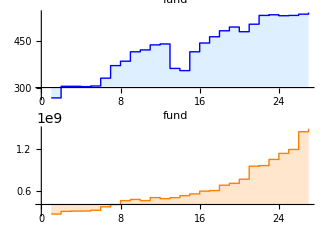
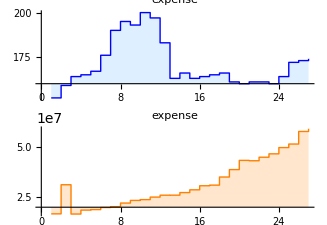
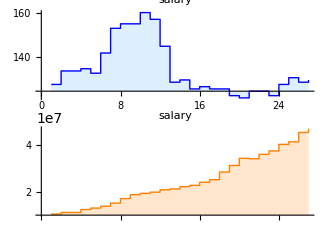
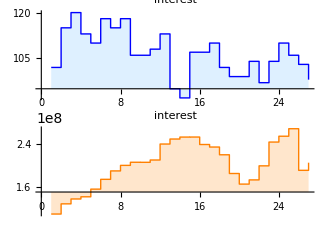
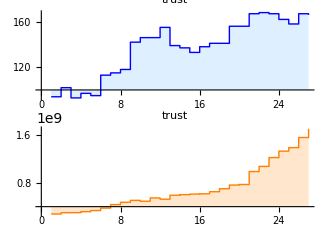
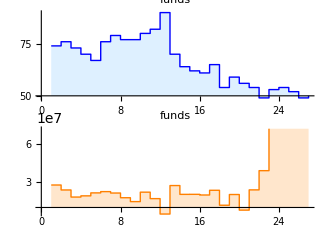
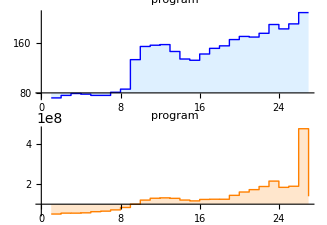
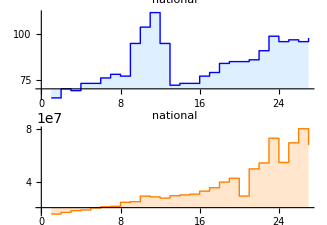

```mathematica
TrendPlot3/@trends[[1;;80]]
```

```mathematica
(* form pdfs and PCA sort the plots
to show similar trends.
(x-min)/(max-min)
*)
```

```mathematica
TrendVec1[trend_]:=Block[{vs,min,max,mean},vs=trend[[2,All,1]];
min=Min[vs]; max=Max[vs];mean=Mean[vs];
If[min==max,ConstantArray[0,Length[vs]],
N[Normalize[(vs-mean)/Max[max-mean,mean-min]]]]
];
TrendVec2[trend_]:=Block[{vs,min,max,mean},vs=trend[[2,All,2]];
min=Min[vs]; max=Max[vs];mean=Mean[vs];
If[min==max,ConstantArray[0,Length[vs]],
N[Normalize[(vs-mean)/Max[max-mean,mean-min]]]]
];
TrendVec3[trend_]:=Join[TrendVec1[trend],TrendVec2[trend]];
```

```mathematica
Needs["MultivariateStatistics`"]
strends=SortBy[Partition[Riffle[trends,PrincipalComponents[TrendVec2/@trends][[All,1]]],2],#[[2]]&][[All,1]];
```

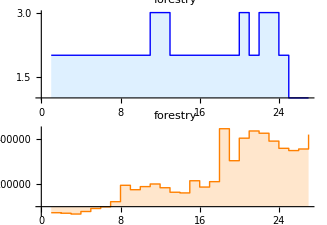
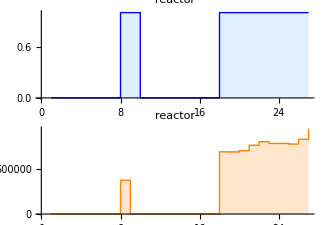
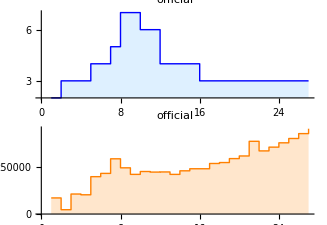
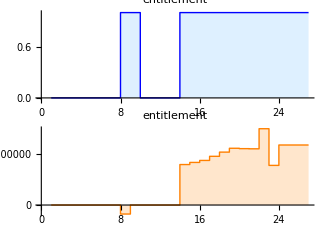
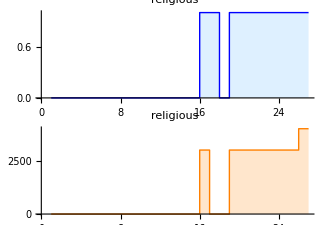
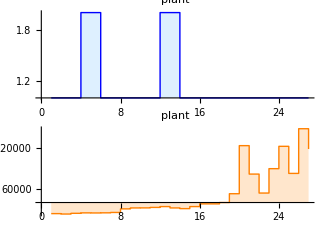
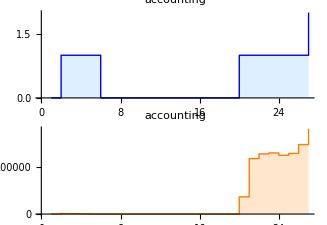
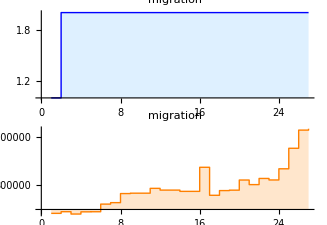
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TrendPlot3/@strends[[200;;250]]
```